# Data analysis for the Fractal Dimension of the b-LRW on 2d square Lattice. After validation. Optimization with Gemini for big data sets

```mathematica
Quit[]
```

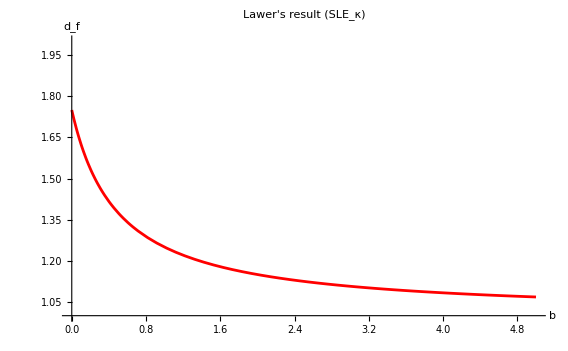

D:\Offline_Documents\University\PhD_Paris\PhD_work\Simulations\MathematicaFiles-LRW-DLA-bLRW\bLRW\bLRW-MicroscopicAction-RG-FractalDim-etc\bLRW-FractalDimFromData\2d-FractalDim

```mathematica
SetOptions[EvaluationNotebook[],NotebookEventActions->{"Open":>(Print["Notebook opened at ",DateString[]];
<<"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\MathematicaFiles-LRW-DLA-bLRW\\bLRW\\bLRW-MicroscopicAction-RG-FractalDim-etc\\bLRW-FractalDimFromData\\2d-FractalDim\\2d-bLRW-FractalDimension.m")}]
<<"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\MathematicaFiles-LRW-DLA-bLRW\\bLRW\\bLRW-MicroscopicAction-RG-FractalDim-etc\\bLRW-FractalDimFromData\\2d-FractalDim\\2d-bLRW-FractalDimension.m"
Directory[]
```

## b4-clean_merged_data-AfterValidation.csv (+extra analysis) SEE BELOW FOR ESTIMATE USING KAY’S TRICK

```mathematica
b=4;

rawData=Import["data4Sqaure-AfterValidation.mx"];

Length[rawData]
```

10827464

Import set-up, run once every time b4-clean_merged_data-AfterValidation.csv gets updated

```mathematica
rawData=Import["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d-FromCluster\\b4-clean_merged_data-AfterValidation.csv","CSV"];
(*Immediately lock it into a Packed Array*)
rawData=data4Square=Developer`ToPackedArray[rawData];
 (* MODIFY FILE NAME *)
Length[rawData]
```

10827464

```mathematica
Export["data4Sqaure-AfterValidation.mx",rawData,"MX"]
```

data4Sqaure-AfterValidation.mx

### RawData analysis: too slow with all these data points

```mathematica
(*Instantly grab 200,000 completely random rows from your matrix*)
randomLinearSample=RandomSample[rawData,200000];
randomLogSample=Log[randomLinearSample];

ListPlot[randomLinearSample,PlotStyle->{PointSize[0.004],Directive[Opacity[0.3]]},FrameLabel->{"L","N"},PlotLabel->"Linear Scale Distribution (200k random points)",PlotRange->All];

ListPlot[randomLinearSample,PlotStyle->{PointSize[0.004],Directive[Opacity[0.3]]},FrameLabel->{"Log[L]","Log[N]"},PlotLabel->"Log-Log Scale Distribution (200k random points)",PlotRange->All];
```

```mathematica
fitFuncs=Table[x^(-i),{i,-1,3}];
(*fitFuncs=Append[Table[x^(-i),{i,-1,0}],Exp[-x]];*)
(*
fitFuncs={x,1,Exp[-x],Exp[-2 x]};(*Exp[-1.3 x]*)*)
fitFuncs={x,1,Exp[-2x]};

logData=Log[rawData];
```

```mathematica
lmp=LinearModelFit[logData,fitFuncs,x];
```

```mathematica
lmp//Normal
```

-0.770538-25.9488 ⅇ^(-2 x)+1.10312 x

```mathematica
lm=LinearModelFit[logData,x,x];
%//Normal
```

$Aborted

$Aborted

```mathematica
fitFunc=a+c Exp[-ω x]+df x;
```

$Aborted

$Aborted

```mathematica
fitSol=FindFit[logData,{fitFunc,{-2<a<1.1,ω<4}},{a,c,ω,df},x]
```

{a→-0.683592,c→-15.9071,ω→1.67825,df→1.08566}

```mathematica
Show[{ListPlot[randomLogSample,PlotStyle->{PointSize[0.003],Directive[Opacity[0.3]]},AxesLabel->{"Log[L]","Log[N]"},DataRange->{0,50}],
Plot[lm[x],{x,0,1000},PlotStyle->{RGBColor[1, 0, 0],Thickness->0.004}]

,Plot[lmp[x],{x,0,1000},PlotStyle->{RGBColor[0, Rational[2, 3], 0],Thickness->0.004}]
,Plot[fitFunc/.fitSol,{x,0,1000},PlotStyle->{RGBColor[1, Rational[2, 3], 1],Thickness->0.004}]

,Plot[x (dfSLE/.bb->b)-1,{x,1,10000},PlotStyle->{RGBColor[0, 0, 1],Dashed}]}
,PlotLabel->Row[{" b = ",b}](*,PlotRange->{{1,Log[200]},{0,Log[100]}}*)
]

Print[ "Linear fit RGBColor[1, 0, 0]: d_f=",Around[Quiet@lm["ParameterTable"][[1]][[1,3,2]],π*lm["ParameterErrors"][[2]]],"
",Total@fitFuncs," fit RGBColor[0, Rational[2, 3], 0]: d_f=",Around[Quiet@lmp["ParameterTable"][[1]][[1,2,2]],π*lmp["ParameterErrors"][[1]]],"
",fitFunc," fit RGBColor[1, Rational[2, 3], 1]: d_f=",Around[df/.fitSol,Null],", Parameters:",fitSol,"
Result from the litterature (exact with SLE) RGBColor[0, 0, 1]: ",(dfSLE/.bb->b)," = ",(dfSLE/.bb->b/1.)]
```

```mathematica
Quiet@lm["ParameterTable"][[1]]
Quiet@lmp["ParameterTable"][[1]]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -1.23069 | 0.00174609 | -704.828 | 0.
x | 1.2019 | 0.000397845 | 3021.03 | 0.

| Estimate | Standard Error | t-Statistic | P-Value
x | 1.10355 | 0.000392247 | 2813.4 | 0.
1 | -0.772297 | 0.00176651 | -437.187 | 0.
ⅇ^(-2 x) | -25.9494 | 0.0666507 | -389.333 | 0.

### RawData analysis: Random Sampling

#### Test

```mathematica
(*Instantly grab 100,000 random rows from your matrix*)
randomLinearSample=RandomSample[rawData,100000];
randomLogSample=Log[randomLinearSample];

(*ListPlot[randomLinearSample,PlotStyle->{PointSize[0.004],Directive[Opacity[0.3]]},FrameLabel->{"L","N"},PlotLabel->"Linear Scale Distribution (100k random points)",PlotRange->All];

ListPlot[randomLogSample,PlotStyle->{PointSize[0.004],Directive[Opacity[0.3]]},FrameLabel->{"Log[L]","Log[N]"},PlotLabel->"Log-Log Scale Distribution (100k random points)",PlotRange->All];*)
```

```mathematica
fitFuncs=Table[x^(-i),{i,-1,3}];
(*fitFuncs=Append[Table[x^(-i),{i,-1,0}],Exp[-x]];*)
(*
fitFuncs={x,1,Exp[-x],Exp[-2 x]};(*Exp[-1.3 x]*)*)
fitFuncs={x,1,Exp[-2x]};

logData=Log[rawData];
```

```mathematica
lmp=LinearModelFit[randomLogSample,fitFuncs,x];
%//Normal
```

-0.771324-25.9498 ⅇ^(-2 x)+1.1032 x

```mathematica
lm=LinearModelFit[randomLogSample,x,x];
%//Normal
```

-1.2299+1.20166 x

```mathematica
fitFunc=a+c Exp[-ω x]+df x;
(*fitSol=FindFit[randomLogSample,{fitFunc,{-2<a<1.1,ω<4}},{a,c,ω,df},x]*)
nlm=NonlinearModelFit[randomLogSample,{fitFunc,{-2<a<1.1,ω<1.65}},{a,c,ω,df},x];
%//Normal
```

-0.675277-15.2524 ⅇ^(-1.64999 x)+1.08401 x

```mathematica
randomSamplePlot=ListPlot[randomLogSample,PlotStyle->{PointSize[0.003],Directive[Opacity[0.3]]},AxesLabel->{"Log[L]","Log[N]"},DataRange->{0,50}];
```

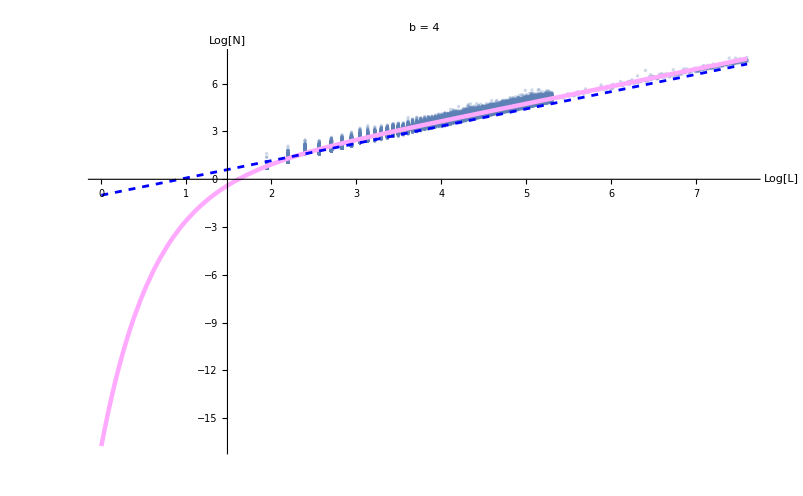

Part::partw: Part 2 of lm[ParameterErrors] does not exist.

Linear fit with random sample RGBColor[1, 0, 0]: d_f =ParameterTable⟦1,3,2⟧π lm[ParameterErrors]⟦2⟧

Random sample fit with 1+ⅇ^(-2 x)+x RGBColor[0, Rational[2, 3], 0]: d_f =ParameterTable⟦1,2,2⟧ParameterErrors π

Random sample fit with a+c ⅇ^(-x ω)+df x RGBColor[1, Rational[2, 3], 1]: d_f =1.08470.0034
	Parameters:{a=-0.6790.005,c=-16.060.33,ω=1.6810.014,df=1.08470.0011}

Result from the litterature (exact with SLE) : 13/12 = 1.08333

```mathematica
maxx=Max[rawData[[All,1]]];
maxy=Max[rawData[[All,2]]];

thresholdBelow=0;
thresholdAbove=maxx-0;

Show[{randomSamplePlot,
Plot[lm[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[1, 0, 0],Thickness->0.004}]

,Plot[lmp[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, Rational[2, 3], 0],Thickness->0.004}]
,Plot[nlm[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[1, Rational[2, 3], 1],Thickness->0.004}]
,Plot[x (dfSLE/.bb->b)-1,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, 0, 1],Dashed}]}
,PlotRange->{{1,All},{0,8}},PlotLabel->Row[{" b = ",b}]
]

Print["Linear fit with random sample RGBColor[1, 0, 0]: d_f =",Around[Quiet@lm["ParameterTable"][[1]][[1,3,2]],π*lm["ParameterErrors"][[2]]],"

Random sample fit with ",Total@fitFuncs," RGBColor[0, Rational[2, 3], 0]: d_f =",Around[Quiet@lmp["ParameterTable"][[1]][[1,2,2]],π*lmp["ParameterErrors"][[1]]],"

Random sample fit with ",fitFunc," RGBColor[1, Rational[2, 3], 1]: d_f =",Around[Quiet@nlm["ParameterTable"][[1,1,5,2]],π*Quiet@nlm["ParameterTable"][[1,1,5,3]]],"
	Parameters:",Map[Row[{#[[1]],"=",Around[#[[2]],#[[3]]]}]&,Quiet@nlm["ParameterTable"][[1,1,2;;-1,1;;3]]],"

Result from the litterature (exact with SLE) : ",(dfSLE/.bb->b)," = ",(dfSLE/.bb->b/1.)]
```

```mathematica
Quiet@lm["ParameterTable"][[1]]
Quiet@lmp["ParameterTable"][[1]]
Quiet@nlm["ParameterTable"][[1]]

Quiet@nlm["BestFitParameters"][[-1,2]]
Quiet@nlm["ParameterErrors"][[-1]]
```

ParameterTable

ParameterTable

| Estimate | Standard Error | t-Statistic | P-Value
a | -0.679281 | 0.00530872 | -127.956 | 0.
c | -16.0648 | 0.332036 | -48.3828 | 0.
ω | 1.6813 | 0.0135989 | 123.635 | 0.
df | 1.08473 | 0.00108137 | 1003.11 | 0.

1.08473

0.00108137

#### Repeated Random Sampling

```mathematica
Global`logData=Log[rawData];

fitFunc=a+c Exp[-ω x]+df x;
```

```mathematica
Quiet@LaunchKernels[];
DistributeDefinitions[rawData];
```

My preliminary implementation

```mathematica
Check[nlm=NonlinearModelFit[randomLogSample,{fitFunc,{-2<a<1.1,ω<2.4}},{a,c,ω,df},x,MaxIterations->100],Nothing]
```

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {a,c,ω,df} = {0.79,1.,1.,1.}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[«1»] failed at {0.79,1.,1.,1.}.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {a,c,ω,df} = {0.79,1.,1.,1.}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[«1»] failed at {0.79,1.,1.,1.}.

Nothing

```mathematica
{nlm=Check[NonlinearModelFit[randomLogSample,{fitFunc,{-2<a<1.1,ω<2.4}},{a,c,ω,df},x,MaxIterations->100],
(*If ANY warning/error occurs (like max iterations hit),return Nothing*)
$Failed];

If[FailureQ[nlm],Nothing,Around[nlm["BestFitParameters"][[1,2]],nlm["ParameterErrors"][[1]]]]}
```

$Aborted

```mathematica
someDf2=ParallelTable[Block[{randomSample,randomLogSample,fitFunc,nlm,value,error},

(*randomSample=RandomSample[rawData,100000];
randomLogSample=Log[randomSample];*)
randomLogSample=RandomSample[Log[rawData],100000];

fitFunc=a+c Exp[-ω x]+df x;

(*nlm=NonlinearModelFit[randomLogSample,{fitFunc,{-2<a<1.1,ω<2.4}},{a,c,ω,df},x,ConfidenceLevel->0.9,MaxIterations->500];*)
nlm=Check[NonlinearModelFit[randomLogSample,{fitFunc,{-2<a<1.1,ω<2.4}},{a,c,ω,df},x,MaxIterations->500],
(*If ANY warning/error occurs (like max iterations hit),return $Failed*)
$Failed];

If[FailureQ[nlm],Nothing,
(*Rule[#[[1]],Around[#[[2]],#[[3]]]]&@(Quiet@nlm["ParameterTable"][[1,1,-1,1;;3]]);*)
(*fractalDim=Around@@@(Quiet@nlm["ParameterTable"][[1,1,-1,2;;3]]);*)
value=Quiet@nlm["BestFitParameters"][[-1,2]];
error=Quiet@nlm["ParameterErrors"][[-1]];

Around[value,error]]
]

,50]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{1.08640.0011,1.08800.0011,1.08710.0011,1.08680.0011,1.08910.0010,1.08640.0011,1.08590.0011,1.08970.0010,1.08740.0011,1.08730.0011,1.08560.0011,1.08570.0011,1.08720.0011,1.08750.0011,1.08710.0011,1.08590.0011,1.08710.0011,1.08700.0011,1.08560.0011,1.08790.0011,1.08580.0011,1.08680.0011,1.08740.0011,1.08890.0011,1.08510.0011,1.08610.0011,1.08750.0011,1.08660.0011,1.50899,1.08530.0011,1.08670.0011,1.08780.0011,1.08660.0010,1.08560.0011,1.08700.0011,1.08330.0011,1.08590.0011,1.08680.0011,1.08870.0010,1.08770.0011,1.08730.0011,1.08810.0010,1.08550.0011,1.08860.0010,1.08630.0011,1.08530.0011,1.08720.0011,1.08640.0011,1.10950.0008,1.08600.0011}

Old Gemini’s code

```mathematica
(*Mixing parallel with batching (implemented with Gemini)*)
```

```mathematica
totalIterations=100;
batchSize=$ProcessorCount; (*Set this to the number of your parallel kernels*)
numBatches=Ceiling[totalIterations/batchSize];

(*Pre-allocate or prepare a file to save data*)
partialResults={};

Do[Print["Processing Batch ",b," of ",numBatches,"..."];

(*1. Fire up a small,controlled parallel batch*)
batchResults=ParallelTable[Block[{randomSample,randomLogSample,fitFunc,nlm,value,error},

(*randomSample=RandomSample[rawData,100000];
randomLogSample=Log[randomSample];*)
randomLogSample=RandomSample[Log[rawData],100000];

fitFunc=a+c Exp[-ω x]+df x;

(*nlm=NonlinearModelFit[randomLogSample,{fitFunc,{-2<a<1.1,ω<2.4}},{a,c,ω,df},x,ConfidenceLevel->0.9,MaxIterations->500];*)
nlm=Check[NonlinearModelFit[randomLogSample,{fitFunc,{-2<a<1.1,ω<2.4}},{a,c,ω,df},x,MaxIterations->500],
(*If ANY warning/error occurs (like max iterations hit),return $Failed*)
$Failed];

If[FailureQ[nlm],Nothing,
(*Rule[#[[1]],Around[#[[2]],#[[3]]]]&@(Quiet@nlm["ParameterTable"][[1,1,-1,1;;3]]);*)
(*fractalDim=Around@@@(Quiet@nlm["ParameterTable"][[1,1,-1,2;;3]]);*)
value=Quiet@nlm["BestFitParameters"][[-1,2]];
error=Quiet@nlm["ParameterErrors"][[-1]];

Around[value,error]]
]

,batchSize];

(*2. Append results to master list*)
partialResults=Join[partialResults,batchResults];
(*3. Save to disk immediately so you never lose progress*)
DumpSave["partial_fit_results.mx",partialResults];
(*4. Force memory cleanup for the master kernel*)
Clear[batchResults];
ClearSystemCache[];
,{b,1,numBatches}];
```

Processing Batch 1 of 10...

Processing Batch 2 of 10...

Processing Batch 3 of 10...

Processing Batch 4 of 10...

Processing Batch 5 of 10...

$Aborted

```mathematica
Clear[partialResults]
Get[$InitialDirectory<>"\partial_fit_results.mx"]
partialResults
```

{1.08600.0011,1.08880.0010,1.08510.0011,1.08540.0011,1.08550.0011,1.08790.0010,1.08630.0011,1.08550.0011,1.08500.0011,1.08550.0011,1.08680.0011,1.08720.0010,1.08780.0011,1.08610.0011,1.08580.0011,1.08380.0011,1.08630.0011,1.08610.0011,1.08650.0011,1.08650.0011,1.08550.0011,1.08640.0011,1.08560.0011,1.08590.0011,1.08620.0011,1.08720.0011,1.08750.0011,1.08460.0011,1.08490.0011,1.08610.0011,1.08820.0011,1.08650.0011,1.08740.0011,1.08640.0011,1.08470.0011,1.08670.0011,1.08860.0011,1.08580.0011,1.08600.0011,1.08560.0011}

#### New Gemini’s code: optimized parallelization

```mathematica
Block[{sample,nlm,value,error,sampleSize},

sampleSize=200000;
sample=Log[RandomSample[rawData,sampleSize]];

nlm=Check[NonlinearModelFit[sample,{fitFunc,{-2<a<1.1,ω<2.3}},{a,c,ω,df},x,MaxIterations->500],
(*If ANY warning/error occurs (like max iterations hit),return $Failed*)
$Failed];


If[FailureQ[nlm],Nothing,
value=Quiet@nlm["BestFitParameters"][[-1,2]];
error=Quiet@nlm["ParameterErrors"][[-1]];

Check[Around[value,error],Nothing]]
]
```

1.08540.0007

```mathematica
taskToSubmit[]
WaitNext[{%}]
```

Block[{sampleSize,sample,fitFunc,nlm,value,error},«1»]

{1.08590.0007,Block[{sampleSize,sample,fitFunc,nlm,value,error},«1»]
,{}}

```mathematica
fitFunc=a+c Exp[-ω x]+df x;
(*DistributeDefinitions[fitFunc];*)

totalTasks=1000;
resultsFile="live_fit_results.mx";
batchSize=$ProcessorCount;
numBatches=Ceiling[totalIterations/batchSize];

(*Initialize an empty list on disk if it doesn't exist*)
If[!FileExistsQ[resultsFile],
savedResults={};
DumpSave[resultsFile,savedResults]];

taskToSubmit[]:=ParallelSubmit[
Block[{sampleSize,sample,fitFunc,nlm,value,error},

sampleSize=200000;
sample=Log[RandomSample[rawData,sampleSize]];

fitFunc=a+c Exp[-ω x]+df x;
nlm=Check[NonlinearModelFit[sample,{fitFunc,{-2<a<1.1,ω<2.4}},{a,c,ω,df},x,MaxIterations->500],
(*If ANY warning/error occurs (like max iterations hit),return $Failed*)
$Failed];


If[FailureQ[nlm],Nothing,
value=Quiet@nlm["BestFitParameters"][[-1,2]];
error=Quiet@nlm["ParameterErrors"][[-1]];

Check[Around[value,error],Nothing]]
]
];

(*1. Initialize status monitoring variable*)
statusString="Initializing tasks...";
Print[Dynamic[statusString]]; (*Displays a single,auto-refreshing line*)
(*Print the live-updating progress panel*)(*Print[Panel[Column[{Row[{Style["Task Progress: ",Bold],Dynamic[completedCount]," / ",totalTasks}],Dynamic[ProgressIndicator[completedCount,{0,totalTasks},ImageSize->Large]],Row[{Style["Active Worker Queue: ",Gray],Dynamic[Length[activeTasks]]}]},Spacings->1],Background->GrayLevel[0.95],FrameMargins->15]]*)
activeTasks={};
completedCount=0;
startTime=AbsoluteTime[]; (*Capture exact start time*)

(*Print the live-updating progress panel with a timer*)
FormatTime[sec_]:=With[{s=Round[sec]},StringRiffle[IntegerString[#,10,2]&/@{Quotient[s,3600],Mod[Quotient[s,60],60],Mod[s,60]},":"]];
Print[Panel[Column[{Row[{Style["Task Progress: ",Bold],Dynamic[completedCount]," / ",totalTasks}],Dynamic[ProgressIndicator[completedCount,{0,totalTasks},ImageSize->Large]],
(*Dynamic Timer Row*)Dynamic[With[{elapsed=Round[AbsoluteTime[]-startTime]//N},Row[{Style["Elapsed: ",Gray],FormatTime[elapsed],"   |   ",Style["ETA: ",Gray],If[completedCount>0,With[{remaining=Round[(elapsed/completedCount)*(totalTasks-completedCount)]//N},FormatTime[remaining]],"Calculating..."]}]]],Row[{Style["Active Worker Queue: ",Gray],Dynamic[Length[activeTasks]]}]},Spacings->1],Background->GrayLevel[0.95],FrameMargins->15]]


(* Run the extraction *)
Block[{},

(*1. Prime the queue: launch 1 task per CPU core*)
activeTasks=Table[
taskToSubmit[]
,batchSize];


(*2. Dynamic loop:Process results as they finish live*)
While[Length[activeTasks]>0,

(*2. Update the dynamic variable instead of calling Print*)statusString=StringForm["Completed `` out of `` tasks. Active queue: ``",completedCount,totalTasks,Length[activeTasks]];

(*WaitNext pauses until ANY single core finishes,returning its data*)
{finishedValue,finishedTask,activeTasks}=WaitNext[activeTasks];
completedCount++;
(*If it yielded a valid fit (not Nothing),append and save instantly*)
If[finishedValue=!=Nothing,
Get[resultsFile];
(*Load current list*)
AppendTo[savedResults,finishedValue];
DumpSave[resultsFile,savedResults];
(*Flush directly to disk*)
Clear[savedResults];];

(*3. Feed the queue:If tasks remain,deploy a replacement core immediately*)

If[completedCount+Length[activeTasks]<totalTasks,
AppendTo[activeTasks,
taskToSubmit[]];
];
ClearSystemCache[];
];
(*3. Mark execution complete*)
statusString=Style["All tasks finished!",RGBColor[0, Rational[2, 3], 0]];
];


Get[resultsFile];
Mean[savedResults]
```

Task Progress:  / 1000


Active Worker Queue:

$Aborted

1.086670.00006

```mathematica
resultsFile="live_fit_results.mx";
FileNameJoin[{Directory[],resultsFile}]
Get[resultsFile]
savedResults
Mean[%]
```

D:\Offline_Documents\University\PhD_Paris\PhD_work\Simulations\MathematicaFiles-LRW-DLA-bLRW\bLRW\bLRW-MicroscopicAction-RG-FractalDim-etc\bLRW-FractalDimFromData\2d-FractalDim\live_fit_results.mx

{1.08790.0007,1.08670.0007,1.08660.0008,1.08570.0008,1.08620.0008,1.08450.0008,1.08570.0008,1.08580.0008,1.08650.0008,1.08580.0008,1.08590.0008,1.08590.0008,1.08740.0008,1.08560.0008,1.08650.0008,1.08650.0007,1.08660.0008,1.08690.0007,1.08720.0008,1.08740.0007,1.08580.0008,1.08630.0008,1.08780.0007,1.08680.0007,1.08790.0007,1.08690.0007,1.08720.0007,1.08660.0008,1.08620.0008,1.08550.0008,1.08700.0008,1.08660.0008,1.08660.0008,1.08740.0008,1.08660.0008,1.08730.0007,1.08850.0007,1.08690.0008,1.08610.0008,1.08710.0008,1.08650.0008,1.08640.0008,1.08530.0008,1.08690.0007,1.08710.0008,1.08670.0008,1.08720.0008,1.08650.0008,1.08650.0008,1.08740.0007,1.08670.0007,1.08600.0007,1.08670.0007,1.08780.0007,1.08700.0007,1.08620.0007,1.08600.0007,1.08580.0007,1.08730.0007,1.08780.0007,1.08650.0007,1.08600.0007,1.08630.0007,1.08710.0007,1.08710.0007,1.08840.0007,1.08740.0007,1.08690.0007,1.08700.0007,1.08640.0007,1.08750.0007,1.08730.0007,1.08690.0007,1.08680.0007,1.08760.0007,1.08720.0007,1.08620.0007,1.08570.0007,1.08820.0007,1.08570.0007,1.08700.0007,1.08690.0007,1.08590.0007,1.08660.0007,1.08650.0007,1.08730.0007,1.08530.0007,1.08670.0007,1.08680.0007,1.08690.0007,1.08740.0007,1.08540.0007,1.08630.0007,1.08700.0007,1.08680.0007,1.08630.0007,1.08540.0007,1.08640.0007,1.08690.0007,1.08720.0007,1.08600.0007,1.08750.0007,1.08610.0007,1.08720.0007,1.08600.0007,1.08640.0007,1.08810.0007,1.08810.0007,1.08660.0007,1.08740.0007,1.08550.0007,1.08670.0007,1.08740.0007,1.08730.0007,1.08710.0007,1.08610.0007,1.08590.0007,1.08920.0007,1.08490.0007,1.08560.0007,1.08680.0007,1.08810.0007,1.08640.0007,1.08640.0007,1.08660.0007,1.08830.0007,1.08670.0007,1.08640.0007,1.08570.0007,1.08610.0007,1.08530.0007,1.08710.0007,1.08660.0007,1.08600.0007,1.08720.0007,1.08610.0007,1.08650.0007,1.08580.0007,1.08450.0007,1.08670.0007,1.08630.0007,1.08530.0007,1.08640.0007,1.08710.0007,1.08640.0007,1.08750.0007,1.08700.0007,1.08600.0007,1.08650.0007,1.08630.0007,1.08680.0007,1.08690.0007,1.08680.0007,1.08630.0007,1.08630.0007,1.08820.0007,1.08720.0007,1.08690.0007,1.08800.0007,1.08610.0007,1.08670.0007,1.08630.0007,1.08560.0007,1.08710.0007,1.08710.0007,1.08830.0007,1.08630.0007,1.08640.0007,1.08640.0007,1.08660.0007}

1.086670.00006

This  was  just  a  test to check if table works

```mathematica
Table[Block[{randomLogSample,fitFunc,nlm,value,error},

randomLogSample=RandomSample[logData,100000];

fitFunc=a+c Exp[-ω x]+df x;

nlm=NonlinearModelFit[randomLogSample,{fitFunc,{-2<a<1.1,ω<2.4}},{a,c,ω,df},x];

(*Rule[#[[1]],Around[#[[2]],#[[3]]]]&@(Quiet@nlm["ParameterTable"][[1,1,-1,1;;3]]);*)
(*fractalDim=Around@@@(Quiet@nlm["ParameterTable"][[1,1,-1,2;;3]]);*)
value=Quiet@nlm["BestFitParameters"][[-1,2]];
error=Quiet@nlm["ParameterErrors"][[-1]];

Around[value,error]
]

,5]
```

{1.08560.0011,1.08570.0011,1.08600.0011,1.08620.0011,1.08750.0011}

Mean

```mathematica
Join[someDf,partialResults,savedResults,someDf3,{1.08560.0011,1.08570.0011,1.08600.0011,1.08620.0011,1.08750.0011}];
Select[%,(Head[#]==Around)&]
Mean[%]
```

{1.08640.0011,1.08800.0011,1.08710.0011,1.08680.0011,1.08910.0010,1.08640.0011,1.08590.0011,1.08970.0010,1.08740.0011,1.08730.0011,1.08560.0011,1.08570.0011,1.08720.0011,1.08750.0011,1.08710.0011,1.08590.0011,1.08710.0011,1.08700.0011,1.08560.0011,1.08790.0011,1.08580.0011,1.08680.0011,1.08740.0011,1.08890.0011,1.08510.0011,1.08610.0011,1.08750.0011,1.08660.0011,1.08530.0011,1.08670.0011,1.08780.0011,1.08660.0010,1.08560.0011,1.08700.0011,1.08330.0011,1.08590.0011,1.08680.0011,1.08870.0010,1.08770.0011,1.08730.0011,1.08810.0010,1.08550.0011,1.08860.0010,1.08630.0011,1.08530.0011,1.08720.0011,1.08640.0011,1.10950.0008,1.08600.0011,1.08600.0011,1.08880.0010,1.08510.0011,1.08540.0011,1.08550.0011,1.08790.0010,1.08630.0011,1.08550.0011,1.08500.0011,1.08550.0011,1.08680.0011,1.08720.0010,1.08780.0011,1.08610.0011,1.08580.0011,1.08380.0011,1.08630.0011,1.08610.0011,1.08650.0011,1.08650.0011,1.08550.0011,1.08640.0011,1.08560.0011,1.08590.0011,1.08620.0011,1.08720.0011,1.08750.0011,1.08460.0011,1.08490.0011,1.08610.0011,1.08820.0011,1.08650.0011,1.08740.0011,1.08640.0011,1.08470.0011,1.08670.0011,1.08860.0011,1.08580.0011,1.08600.0011,1.08560.0011,1.08810.0010,1.08700.0011,1.08780.0011,1.08550.0011,1.08830.0011,1.08580.0011,1.08460.0011,1.08550.0011,1.08650.0011,1.08770.0011,1.08560.0011,1.08570.0011,1.08600.0011,1.08620.0011,1.08750.0011}

1.086770.00010

```mathematica
Mean[someDf]
```

{1.10669,0.000626622}

### Test with mean over same L BEFORE LOG: Log[<y>] VERY GOOD AGREEMENT?

```mathematica
(*1. Gather rows by their first element (x) at C-speed*)
gathered=GatherBy[rawData,First];

(*2. Extract the unique X values directly from the gathered groups*)
xValues=gathered[[All,1,1]];

(*3. Extract the Y values for each group*)
yGroups=gathered[[All,All,2]];

(*4. Map Mean and StandardDeviation across the groups in bulk*)
means=Mean/@yGroups/. 0.->1.0*^-8;

(*Standard deviation throws an error/indeterminacy if length is 1,so we replace Indeterminate with 0 globally at the end*)
stdDevs=StandardDeviation/@yGroups/. Indeterminate->1.0*^-8;
stdDevs=stdDevs/. 0.->1.0*^-8;

(* Maximum deviation*)
maxDevs=MapThread[Max[Abs[#1-#2]]&,{means//N,yGroups}];


(*5. Combine them using the Threaded Around wrapper*)

averaged=Transpose[{xValues,means}];
averagedWithErrors=Transpose[{xValues,MapThread[Around,{means,stdDevs}]}];
averagedWithMaxDev=Transpose[{xValues,MapThread[Around,{means,maxDevs}]}];
```

```mathematica
Averagedb4AfterValidation=averaged;
```

Gemini says this is slow

```mathematica
maxx=Max[rawData[[All,1]]];
maxy=Max[rawData[[All,2]]];

thresholdBelow=44;
thresholdAbove=maxx-0;

grouped=GroupBy[rawData,First->Last];

(*Map over the groups to create {x,Around[mean,stdDev]} pairs*)
Averagedb4AfterValidation=KeyValueMap[
Function[{x,yValues},
{x,If[Length[yValues]>1,
Around[Mean[yValues],StandardDeviation[yValues]],
Around[Mean[yValues],1] (*Error is 0 if there is only 1 data point*)]}],grouped];

Averaged=KeyValueMap[{#1,Mean[#2]}&,GroupBy[rawData,First->Last]];
```

Continues here

```mathematica
logAveraged=Log[averaged];
logAveragedWithErrors=Log[averagedWithErrors]/. 0->Around[1.0*^-6,1.0*^-6];
logAveragedWithMaxDev=Log[averagedWithMaxDev]/. 0->Around[1.0*^-6,1.0*^-6];
```

```mathematica
logAveragedWithErrors//Length
weights=Map[#[[2]]["Uncertainty"]&,logAveragedWithErrors];
%//Length
Position[weights,_?(Element[#,Reals]=!=True&)]


weights=Map[#[[2]]["Uncertainty"]&,logAveragedWithMaxDev];
%//Length
Position[weights,_?(Element[#,Reals]=!=True&)]
```

999

999

{{0}}

999

{{0}}

```mathematica
fitFuncs=Table[x^(-i),{i,-1,3}];
(*fitFuncs=Append[Table[x^(-i),{i,-1,0}],Exp[-x]];*)
(*fitFuncs={x,1,Exp[-x],Exp[-2 x]};(*Exp[-1.3 x]*)*)
fitFuncs={x,1,Exp[-2 x],Exp[-x]};
fitFunc=a+c Exp[-ω x]+df x;

lmAveraged=LinearModelFit[logAveragedWithErrors,x,x(*,Weights->Automatic*)];
Print[Row[{"lmAveraged: ",#//Normal}]]&@%
lmMaxDev=LinearModelFit[logAveragedWithMaxDev,x,x(*,Weights->Automatic*)];
Print[Row[{"lmMaxDev: ",#//Normal}]]&@%

lmpAveraged=LinearModelFit[logAveragedWithErrors,fitFuncs,x];
Print[Row[{"lmpAveraged: ",#//Normal}]]&@%

lmpMaxDev=LinearModelFit[logAveragedWithMaxDev,fitFuncs,x];
Print[Row[{"lmpMaxDev: ",#//Normal}]]&@%

fitFunc=a+c Exp[-ω x]+df x;
fitSol=FindFit[logAveraged,{fitFunc,{-2<a<2,0<ω<28}},{a,c,ω,df},x]

nlmAveraged=NonlinearModelFit[logAveragedWithErrors,{fitFunc,{-2<a<2,1.9<ω<=22.1}},{{a,-0.5},{c,-30.},{ω,2.},{df,1.083}},x];
Print[Row[{"nlmAveraged: ",#//Normal}]]&@%

fitFunc=a+c Exp[-ω x]+c2 Exp[-ω2 x]+df x;

nlmAveraged2=NonlinearModelFit[logAveragedWithErrors,{fitFunc,{-2<a<2,2.<=ω<=3.,0.1<=ω2<=1.}},{{a,-0.5},{c,-30.},ω,c2,ω2,df(*{df,1.083}*)},x,MaxIterations->1000]//Quiet;
Print[Row[{"nlmAveraged2: ",#//Normal}]]&@%
nlmMaxDev=NonlinearModelFit[logAveragedWithMaxDev,{fitFunc,{-2<a<2,2.<=ω<=3.,0.1<=ω2<=1.}},{{a,-0.5},{c,-30.},ω,c2,ω2,df(*{df,1.083}*)},x,MaxIterations->1000]//Quiet;
Print[Row[{"nlmMaxDev: ",#//Normal}]]&@%
```

lmAveraged: -2.04802+1.27251 x

lmMaxDev: -2.04065+1.26793 x

lmpAveraged: -0.395455-7.35802 ⅇ^(-2 x)-4.89975 ⅇ^-x+1.03746 x

lmpMaxDev: -0.353342-4.12927 ⅇ^(-2 x)-5.70918 ⅇ^-x+1.03163 x

{a→-0.671129,c→-15.1774,ω→18.8073,df→1.07701}

nlmAveraged: -0.507991-30.0973 ⅇ^(-2.00918 x)+1.05269 x

nlmAveraged2: -0.558516-30.1212 ⅇ^(-2.0015 x)+0.261664 ⅇ^(-0.972476 x)+1.05985 x

nlmMaxDev: -0.792991-30.0494 ⅇ^(-2.00528 x)+0.739834 ⅇ^(-0.733701 x)+1.0921 x

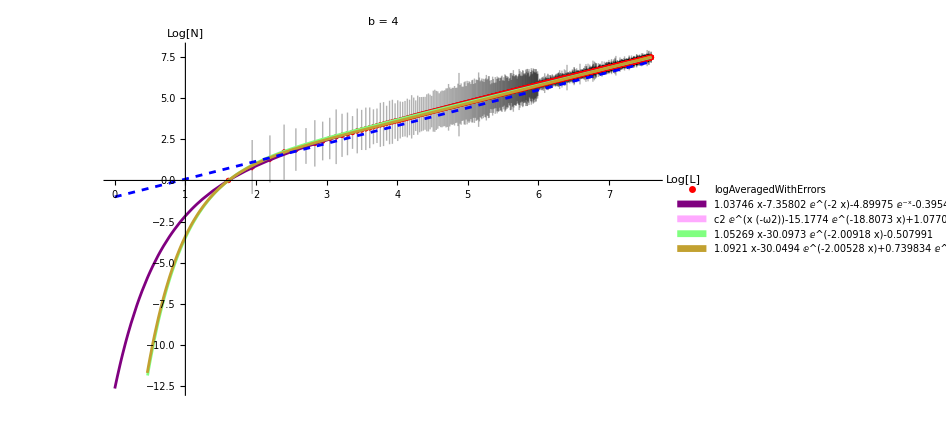

Averaged data fit with errors and 1+ⅇ^(-2 x)+ⅇ^-x+x RGBColor[0.5, 0, 0.5]: d_f=1.03750.0024

a+c ⅇ^(-x ω)+c2 ⅇ^(-x ω2)+df x  fit  RGBColor[1, Rational[2, 3], 1]: d_f=1.07701Null, Parameters:{a→-0.671129,c→-15.1774,ω→18.8073,df→1.07701}
Averaged data fit with errors and a+c ⅇ^(-x ω)+c2 ⅇ^(-x ω2)+df xnonlinearModel RGBColor[0.5, 1, 0.5]: d_f=1.05270.0023

Averaged data fit with MaxDevs and a+c ⅇ^(-x ω)+c2 ⅇ^(-x ω2)+df xnonlinearModel RGBColor[0.76, 0.63, 0.19]: d_f=1.0920.024, Parameters: | Estimate | Standard Error | t-Statistic | P-Value
a | -0.792991 | 0.218395 | -3.63099 | 0.000296761
c | -30.0494 | 46.2152 | -0.650207 | 0.515709
ω | 2.00528 | 1.75435 | 1.14303 | 0.2533
c2 | 0.739834 | 8.65611 | 0.0854696 | 0.931905
ω2 | 0.733701 | 3.31088 | 0.221603 | 0.824669
df | 1.0921 | 0.0238812 | 45.7304 | 1.28389×10^-246

Result from the litterature (exact with SLE) RGBColor[0, 0, 1]: 13/12 = 1.08333

```mathematica
maxx=Max[rawData[[All,1]]];
maxy=Max[rawData[[All,2]]];

thresholdBelow=0;
thresholdAbove=maxx-0;

Show[{ListPlot[logAveragedWithMaxDev,PlotStyle->{GrayLevel[0],Directive[Opacity[0.3]]},AxesLabel->{"Log[L]","Log[N]"}]
,ListPlot[logAveragedWithErrors,PlotStyle->RGBColor[1, 0, 0],PlotLegends->{"logAveragedWithErrors"}(*Placed[SwatchLegend[Automatic],Right]*)]
(*,Plot[lmp[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, Rational[2, 3], 0],Thickness->0.004}]*)
,(*Plot[lmAveraged[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[1, 0, 0],Thickness->0.004}]
,*)Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 0, 0.5],Thickness->0.004},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],Right]]&@lmpAveraged[x]
,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[1, Rational[2, 3], 1],Thickness->0.004},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],Right]]&@(fitFunc/. fitSol)
,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 1, 0.5],Thickness->0.004},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],Right]]&@nlmAveraged[x]

,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.76, 0.63, 0.19],Thickness->0.004},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],Right]]&@nlmMaxDev[x]

,Plot[x (dfSLE/.bb->b)-1,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, 0, 1],Dashed}]}
,(*PlotRange->All,*)PlotLabel->Row[{" b = ",b}]
(*,Epilog->{Directive[Dashed,GrayLevel[0.5]],
Line[{{Log[thresholdBelow],0},{Log[thresholdBelow],Log[maxy]//N}}]
,Line[{{Log[thresholdAbove],0},{Log[thresholdAbove],Log[maxy]//N}}]}*)
,PlotRange->{All,{0,All}},AxesOrigin->{1,0},ImageSize->700]

Print[ (*"Full data - Linear fit : d_f=",Around[Quiet@lm["ParameterTable"][[1]][[1,3,2]],π*lm["ParameterErrors"][[2]]],*)(*"
Averaged data fit with errors RGBColor[1, 0, 0]: d_f=",Around[Quiet@lmAveraged["ParameterTable"][[1]][[1,3,2]],π*lmAveraged["ParameterErrors"][[2]]],*)"
Averaged data fit with errors and " ,Total@fitFuncs," RGBColor[0.5, 0, 0.5]: d_f=",Around[Quiet@lmpAveraged["ParameterTable"][[1]][[1,2,2]],π*lmpAveraged["ParameterErrors"][[1]]],"

",fitFunc,"  fit  RGBColor[1, Rational[2, 3], 1]: d_f=",Around[df/.fitSol,Null],", Parameters:",fitSol,"
Averaged data fit with errors and " ,fitFunc,"nonlinearModel RGBColor[0.5, 1, 0.5]: d_f=",Around[Quiet@nlmAveraged["ParameterTable"][[1,1,-1,2]],π*Quiet@nlmAveraged["ParameterTable"][[1,1,-1,3]]],"

Averaged data fit with MaxDevs and " ,fitFunc,"nonlinearModel RGBColor[0.76, 0.63, 0.19]: d_f=",Around[Quiet@nlmMaxDev["ParameterTable"][[1,1,-1,2]],(*π**)Quiet@nlmMaxDev["ParameterTable"][[1,1,-1,3]]],", Parameters:",Quiet@nlmMaxDev["ParameterTable"],(*,"

Full data - ",Total@fitFuncs," fit: d_f=",Around[Quiet@lmp["ParameterTable"][[1]][[1,2,2]],π*lmp["ParameterErrors"][[1]]]*)"

Result from the litterature (exact with SLE) RGBColor[0, 0, 1]: ",(dfSLE/.bb->b)," = ",(dfSLE/.bb->b/1.)]
```

```mathematica
Quiet@lmpAveraged["ParameterTable"][[1]]
Quiet@nlmAveraged["ParameterTable"][[1]]
```

| Estimate | Standard Error | t-Statistic | P-Value
x | 1.05291 | 0.000680.00007 | 1558.168. | BetaRegularized[0.000410.00009,498,1/2]
1 | -0.509589 | 0.00470.0005 | -109.12. | BetaRegularized[0.0780.016,498,1/2]
ⅇ^(-2 x) | -29.6251 | 0.0900.010 | -328.36. | BetaRegularized[0.00910.0020,498,1/2]

| Estimate | Standard Error | t-Statistic | P-Value
a | -0.653659 | 1.36687 | -0.478216 | 0.632601
c | -3.4484 | 95.7668 | -0.0360083 | 0.971283
ω | 1.32346 | 18.4345 | 0.0717928 | 0.942781
df | 0.660756 | 0.190947 | 3.46042 | 0.000562223

```mathematica
Quiet@nlmMaxDev["ParameterTable"][[1,All,1;;3]]//Normal
```

Part::take: Cannot take positions 1 through 3 in Alignment→{Left,Automatic}.

{{,Estimate,Standard Error},{a,-0.719338,0.114184},{c,-30.0531,45.6826},{ω,2.00371,2.09366},{c2,0.718269,15.1915},{ω2,0.887409,5.07186},{df,1.08243,0.0132121}}

### Test with mean over same L After LOG: <Log[y]>, what we want??? NO WE WANT THE OPPOSITE SINCE <N>~L^d_f!!!!

```mathematica
(*1. Take the Log of all 4,000,000 raw points instantly using vectorization*)
logPackedData=Log[rawData];

(*2. Group by the log(x) column*)
gatheredLog=GatherBy[logPackedData,First];

(*3. Pull out the exact x-values on the log scale*)
logXVals=N[gatheredLog[[All,1,1]]];
logYGroups=N[gatheredLog[[All,All,2]]];
```

```mathematica
(*4. Compute the Means and Standard Deviations directly in log space*)
logMeans=Mean/@logYGroups/. 0.->1.0*^-10;
logStdDevs=StandardDeviation/@logYGroups/. Indeterminate->1.0*^-10;
logStdDevs=logStdDevs/. 0.->1.0*^-10;
(*logStdDevs=Sqrt[(logStdDevs/logMeans^2)];*)
logStdDevs=Sqrt[logStdDevs];
```

```mathematica
(*5. Create your clean,mathematically sound Around matrix*)
Averagedb4AfterValidation=LogData=Transpose[{logXVals,MapThread[Around,{logMeans,logStdDevs}]}];
```

```mathematica
LogData[[1]]
Position[%,_?(Element[#,Reals]=!=True&)]
```

{6.90875,6.760.24}

{{0},{2,0},{2},{}}

```mathematica
(*6. Run the weighted fit*)
lmAveraged=LinearModelFit[LogData,x,x,Weights->Automatic];
lmAveraged//Normal
lmAveraged["ParameterTable"]
```

-2.05458+1.27658 x

| Estimate | Standard Error | t-Statistic | P-Value
1 | -2.05458 | 0.001770.00006 | -1160.39. | BetaRegularized[0.000740.00005,997/2,1/2]
x | 1.27658 | 0.001100.00004 | 1160.39. | BetaRegularized[0.000740.00005,997/2,1/2]

```mathematica
fitFuncs=Table[x^(-i),{i,-1,3}];
(*fitFuncs=Append[Table[x^(-i),{i,-1,0}],Exp[-x]];*)
(*fitFuncs={x,1,Exp[-x],Exp[-2 x]};(*Exp[-1.3 x]*)*)
fitFuncs={x,1,Exp[-2 x]};
fitFunc=a+c Exp[-ω x]+df x;

lmAveraged=LinearModelFit[LogData,x,x(*,Weights->Automatic*)];
%//Normal

lmpAveraged=LinearModelFit[LogData,fitFuncs,x];
%//Normal

(*fitFunc=a+c Exp[-ω x]+df x;
fitSol=FindFit[LogData[[All]][],{fitFunc,{-2<a<2,0<ω<28}},{a,c,ω,df},x]*)

nlmAveraged=NonlinearModelFit[LogData,{fitFunc(*,{-2<a<2,0<ω<3}*)},{a,c,ω,df},x];
%//Normal
```

-2.05458+1.27658 x

-0.542494-28.9883 ⅇ^(-2 x)+1.05753 x

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

-0.181327-4.7442 ⅇ^(-0.73886 x)+1.01019 x

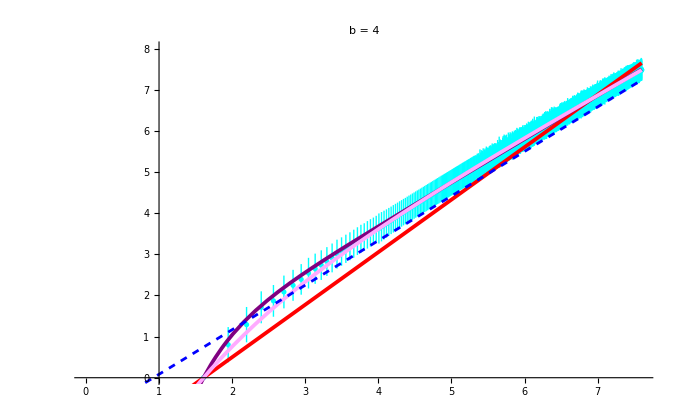

Averaged data fit with errors RGBColor[1, 0, 0]: d_f=1.27660.0035
Averaged data fit with errors and a+c ⅇ^(-x ω)+df x RGBColor[1, Rational[2, 3], 1]: d_f=1.0100.007
	Parameters:{a=-0.1810.019,c=-4.740.07,ω=0.7390.015,df=1.01020.0024}
Averaged data fit with errors and 1+ⅇ^(-2 x)+x RGBColor[0.5, 0, 0.5]: d_f=1.05750.0021

Result from the litterature (exact with SLE) RGBColor[0, 0, 1]: 13/12 = 1.08333

```mathematica
maxx=Max[rawData[[All,1]]];
maxy=Max[rawData[[All,2]]];

thresholdBelow=0;
thresholdAbove=maxx-0;

Show[{(*ListPlot[randomLogSample,PlotStyle->GrayLevel[0],AxesLabel->{Log[L],Log[N]}]
,*)ListPlot[LogData,PlotStyle->RGBColor[0, 1, 1]]
(*,Plot[lmp[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, Rational[2, 3], 0],Thickness->0.004}]*)
,Plot[lmAveraged[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[1, 0, 0],Thickness->0.004}]
,Plot[lmpAveraged[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 0, 0.5],Thickness->0.004}]
,Plot[nlmAveraged[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[1, Rational[2, 3], 1],Thickness->0.004}]

,Plot[x (dfSLE/.bb->b)-1,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, 0, 1],Dashed}]}

,PlotLabel->Row[{" b = ",b}]
,PlotRange->{All,{0,8}},AxesOrigin->{1,0}]

Print[ "Averaged data fit with errors RGBColor[1, 0, 0]: d_f=",Around[Quiet@lmAveraged["ParameterTable"][[1]][[1,3,2]],π*lmAveraged["ParameterErrors"][[2]]],"
Averaged data fit with errors and " ,fitFunc," RGBColor[1, Rational[2, 3], 1]: d_f=",Around[Quiet@nlmAveraged["ParameterTable"][[1,1,5,2]],π*Quiet@nlmAveraged["ParameterTable"][[1,1,5,3]]],"
	Parameters:",Map[Row[{#[[1]],"=",Around[#[[2]],#[[3]]]}]&,Quiet@nlmAveraged["ParameterTable"][[1,1,2;;-1,1;;3]]],"
Averaged data fit with errors and " ,Total@fitFuncs," RGBColor[0.5, 0, 0.5]: d_f=",Around[Quiet@lmpAveraged["ParameterTable"][[1]][[1,2,2]],π*lmpAveraged["ParameterErrors"][[1]]],"

Result from the litterature (exact with SLE) RGBColor[0, 0, 1]: ",(dfSLE/.bb->b)," = ",(dfSLE/.bb->b/1.)]
```

```mathematica
Quiet@lmpAveraged["ParameterTable"][[1]]
Quiet@nlmAveraged["ParameterTable"][[1]]
```

{{,Estimate,Standard Error,t-Statistic,P-Value},{x,1.05426,0.000660.00007,1587.168.,BetaRegularized[0.000400.00008,498,1/2]},{1,-0.521323,0.00460.0005,-113.12.,BetaRegularized[0.0720.014,498,1/2]},{ⅇ^(-2 x),-29.3862,0.0880.009,-332.35.,BetaRegularized[0.00900.0019,498,1/2]}}

{{a,-0.414491,0.00729814},{c,-7.44508,0.205558},{ω,1.10437,0.0194891},{df,1.03966,0.000992428}}

### Drop both first and/or last few

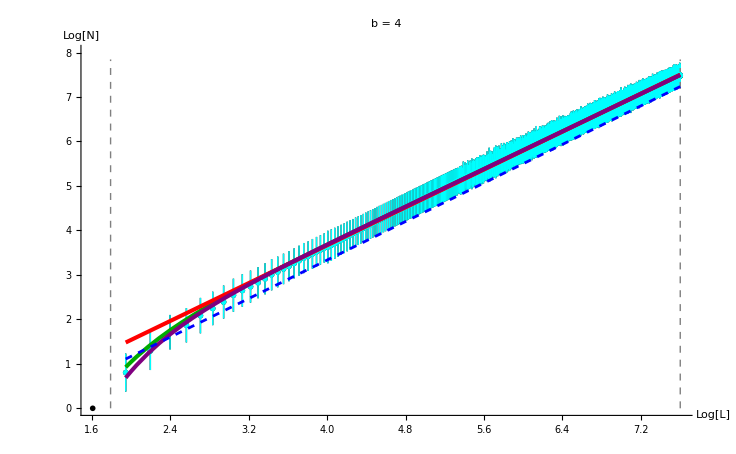

Full averaged data - Linear fit : d_f=1.27660.0035
Dropped data - Linear fit RGBColor[1, 0, 0]: d_f=1.06470.0032

Full averaged data - 1+ⅇ^(-2 x)+x fit RGBColor[0, Rational[2, 3], 0]: d_f=1.05750.0021
Dropped data with 1+ⅇ^(-2 x)+x fit RGBColor[0.5, 0, 0.5]: d_f=1.05550.0020

Result from the litterature (exact with SLE) RGBColor[0, 0, 1]: 13/12 = 1.08333

```mathematica
maxx=Max[rawData[[All,1]]];
maxy=Max[rawData[[All,2]]];

thresholdBelow=6;
thresholdAbove=maxx-0;

dropped=droppedb4AfterValidation=Select[LogData,Log[thresholdBelow]<#[[1]]<Log[thresholdAbove]&];

lmdropped=LinearModelFit[dropped,x,x,Weights->Automatic];

lmpdropped=LinearModelFit[dropped,fitFuncs,x];

Show[{ListPlot[LogData,PlotStyle->GrayLevel[0],AxesLabel->{"Log[L]","Log[N]"}]
,ListPlot[dropped,PlotStyle->RGBColor[0, 1, 1]]

,Plot[lmpAveraged[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, Rational[2, 3], 0],Thickness->0.004}]
(*,Plot[fitFunc/.fitSol,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[1, Rational[2, 3], 1],Thickness->0.004}]*)

,Plot[lmdropped[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[1, 0, 0],Thickness->0.004}]
,Plot[lmpdropped[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 0, 0.5],Thickness->0.004}]


,Plot[x (dfSLE/.bb->b)-1,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, 0, 1],Dashed}]
}

,(*PlotRange->All,*)PlotLabel->Row[{" b = ",b}]
,Epilog->{Directive[Dashed,GrayLevel[0.5]],
Line[{{Log[thresholdBelow],0},{Log[thresholdBelow],Log[maxy]//N}}]
,Line[{{Log[thresholdAbove],0},{Log[thresholdAbove],Log[maxy]//N}}]}
,PlotRange->{All,{0,8}},AxesOrigin->{1,0}]

Print[ "Full averaged data - Linear fit : d_f=",Around[Quiet@lmAveraged["ParameterTable"][[1]][[1,3,2]],π*lmAveraged["ParameterErrors"][[2]]],"
Dropped data - Linear fit RGBColor[1, 0, 0]: d_f=",Around[Quiet@lmdropped["ParameterTable"][[1]][[1,3,2]],π*lmdropped["ParameterErrors"][[2]]],"

Full averaged data - ",Total@fitFuncs," fit RGBColor[0, Rational[2, 3], 0]: d_f=",Around[Quiet@lmpAveraged["ParameterTable"][[1]][[1,2,2]],π*lmpAveraged["ParameterErrors"][[1]]],"
Dropped data with " ,Total@fitFuncs," fit RGBColor[0.5, 0, 0.5]: d_f=",Around[Quiet@lmpdropped["ParameterTable"][[1]][[1,2,2]],π*lmpdropped["ParameterErrors"][[1]]],"

Result from the litterature (exact with SLE) RGBColor[0, 0, 1]: ",(dfSLE/.bb->b)," = ",(dfSLE/.bb->b/1.)]
```

### Extra analysis

#### Plot with different drops below

```mathematica
dfDropped=ParallelTable[With[{
lmdropped=LinearModelFit[Log[DeleteCases[rawData,{a_,_}/;(a<i )]],x,x]},
{i,Quiet@lmdropped["ParameterTable"][[1]][[1,3,2]]}],{i,5,100}];
```

```mathematica
dfDroppedMore=ParallelTable[With[{
lmdropped=LinearModelFit[Log[DeleteCases[rawData,{a_,_}/;(a<i )]],x,x]},
{i,Quiet@lmdropped["ParameterTable"][[1]][[1,3,2]]}],{i,101,200}];
```

```mathematica
dfDroppedMore2=ParallelTable[With[{
lmdropped=LinearModelFit[Log[DeleteCases[rawData,{a_,_}/;(a<i )]],x,x]},
{i,Quiet@lmdropped["ParameterTable"][[1]][[1,3,2]]}],{i,201,400}];
```

```mathematica
dfDroppedMore3=ParallelTable[With[{
lmdropped=LinearModelFit[Log[DeleteCases[rawData,{a_,_}/;(a<i )]],x,x]},
{i,Quiet@lmdropped["ParameterTable"][[1]][[1,3,2]]}],{i,401,800}];
```

```mathematica
dfDroppedMore4=ParallelTable[With[{
lmdropped=LinearModelFit[Log[DeleteCases[rawData,{a_,_}/;(a<i )]],x,x]},
{i,Quiet@lmdropped["ParameterTable"][[1]][[1,3,2]]}],{i,801,1000}];
```

FittedModel[…]

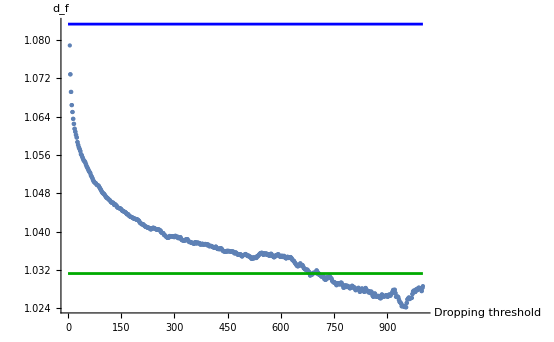

```mathematica
dfTogether=Join[dfDropped,dfDroppedMore,dfDroppedMore2,dfDroppedMore3,dfDroppedMore4];
(*fit=LinearModelFit[dfTogether,{1/Log[x],1},x];
Quiet@fit["ParameterTable"][[1]]*)

lmDrops=LinearModelFit[DeleteCases[dfTogether,{x_,_}/;(x<400)],{1},x]

Show[
{ListPlot[dfTogether,PlotRange->{All,All}]
(*,Plot[fit[x],{x,0,1000},PlotStyle->Red]*)
,Plot[dfSLE/.bb->b/1.,{x,0,1000},PlotStyle->RGBColor[0, 0, 1]]
,Plot[lmDrops[x],{x,0,1000},PlotStyle->RGBColor[0, Rational[2, 3], 0]]
}
,AxesLabel->{"Dropping threshold",Subscript[d, f]},PlotRange->All]
```

#### Plot with different drops Above BAD

```mathematica
thresholdBelow=200;(*Fix this*)

dfDroppedAbove=Table[With[{
lmdropped=LinearModelFit[Log[DeleteCases[rawData,{a_,_}/;(a<thresholdBelow ||  a>(maxx-i))]],x,x]},
{i,Quiet@lmdropped["ParameterTable"][[1]][[1,3,2]]}],{i,0,1500}];
```

```mathematica
fitFunc=a+d Exp[c x];
fit=FindFit[dfDroppedAbove,fitFunc,{a,c,d},x]

Show[
{ListPlot[dfDroppedAbove,PlotRange->{All,All}]
,Plot[fitFunc/.fit,{x,2,1500},PlotStyle->Red]
,Plot[dfSLE/.bb->b/1.,{x,0,1000},PlotStyle->Blue]
},PlotRange->{All,All}]
```

{a→8.0864733946827×10^618,c→1.,d→-1.98793×10^-28}

-Graphics-

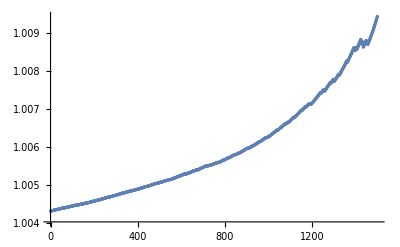

```mathematica
ListPlot[dfDroppedAbove,PlotRange->{All,All}]
```

#### Plot with different POSITIONS of the same WINDOW: (i)< a < (i + 500)

```mathematica
window=500;(*Set this*)

dfDroppedWindow=Table[With[{
lmdropped=LinearModelFit[Log[DeleteCases[rawData,{a_,_}/;(a<(i) ||  a>(i+window))]],x,x]},
{i,Quiet@lmdropped["ParameterTable"][[1]][[1,3,2]]}],{i,0,1500}];
```

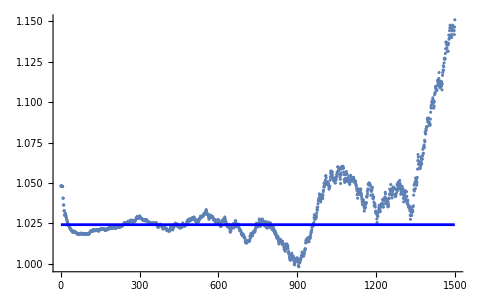

```mathematica
Show[
{ListPlot[dfDroppedWindow,PlotRange->{All,All}]
,Plot[dfSLE/.bb->b/1.,{x,0,1500},PlotStyle->Blue]
},PlotRange->{All,All}]
```

#### Plot with different POSITIONS of the same WINDOW: Changing window

```mathematica
window=500;(*Set this*)
```

```mathematica
windowPlots=Table[
dfDroppedWindow={window,Table[With[{
lmdropped=LinearModelFit[Log[DeleteCases[rawData,{a_,_}/;(a<(i) ||  a>(i+window))]],x,x]},
{i,Around[Quiet@lmdropped["ParameterTable"][[1]][[1,3,2]],π*lmdropped["ParameterErrors"][[2]]]}],{i,0,2000-window,20}]}
,{window,100,1000,50}];
```

```mathematica
windowPlots[[1]]
```

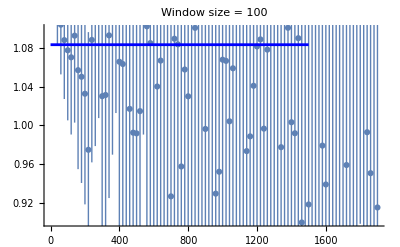
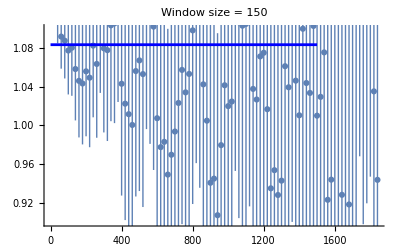
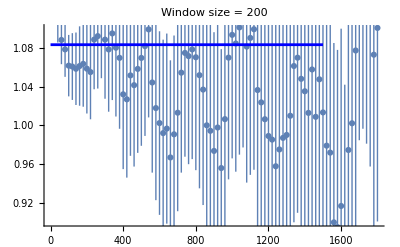
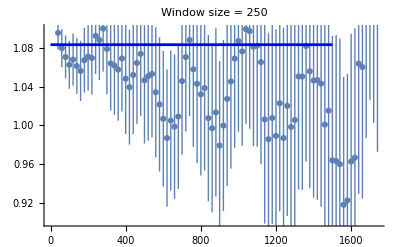
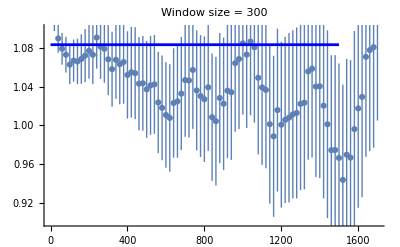
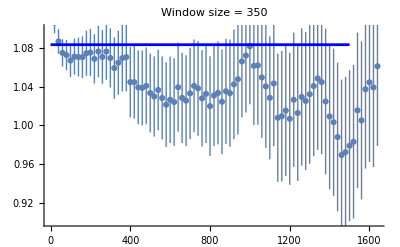
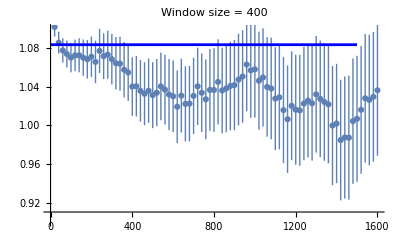
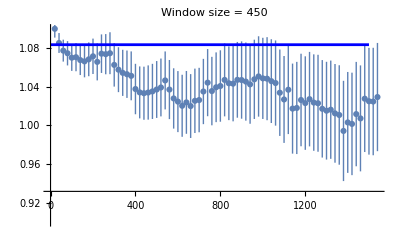

```mathematica
showWindowPlots=Show[
{ListPlot[#[[2]],PlotRange->{All,All}]
,Plot[dfSLE/.bb->b/1.,{x,0,2000-window},PlotStyle->RGBColor[0, 0, 1]]
},PlotRange->{All,{0.9,1.1}},PlotLabel->Row[{"Window size = ",#[[1]]}]]&/@windowPlots
```

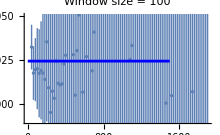
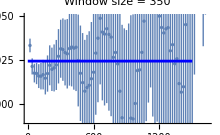
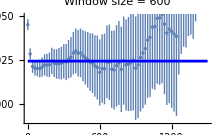
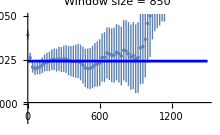
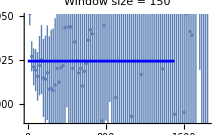
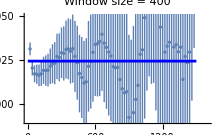
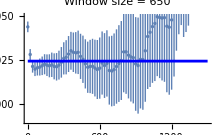
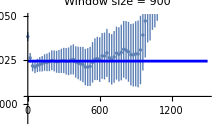
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
synchronizedPlots=Map[Show[#,PlotRange->{All,{0.99,1.05}},ImageSize->220]&,showWindowPlots];

Multicolumn[synchronizedPlots,4,Appearance->"Framed"]
```

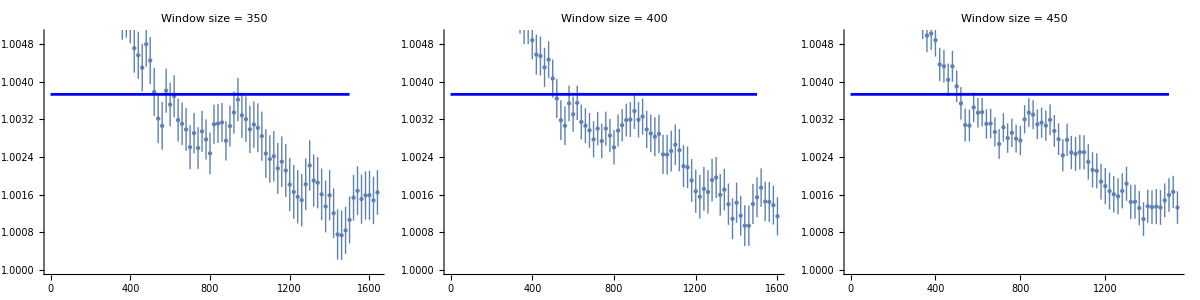

```mathematica
Map[Show[#,PlotRange->{All,{1,1.005}},ImageSize->280]&,showWindowPlots[[6;;8]]];
Multicolumn[%,3,Appearance->"Framed"]
```

## b=15 With points from the CLUSTER with Square BC with Log (+extra analysis)

```mathematica
b=15;

rawData=Import["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d-FromCluster\\b15-clean_merged_data-Square.csv","CSV"];
(*Immediately lock it into a Packed Array*)
rawData=data15square=Developer`ToPackedArray[rawData];
 (* MODIFY FILE NAME *)

Length[rawData]
```

16545

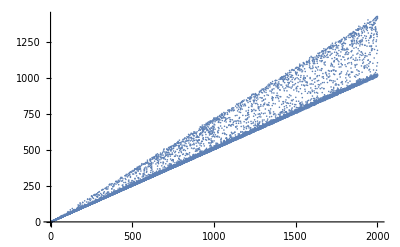

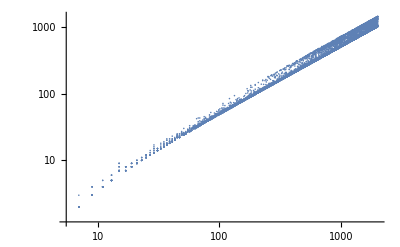

```mathematica
ListPlot[rawData]
ListLogLogPlot[rawData]
```

### Test with mean over same L BEFORE LOG: Log[<y>] VERY GOOD AGREEMENT?

```mathematica
(*1. Gather rows by their first element (x) at C-speed*)
gathered=GatherBy[rawData,First];

(*2. Extract the unique X values directly from the gathered groups*)
xValues=gathered[[All,1,1]];

(*3. Extract the Y values for each group*)
yGroups=gathered[[All,All,2]];

(*4. Map Mean and StandardDeviation across the groups in bulk*)
means=Mean/@yGroups/. 0.->1.0*^-8;

(*Standard deviation throws an error/indeterminacy if length is 1,so we replace Indeterminate with 0 globally at the end*)
stdDevs=StandardDeviation/@yGroups/. Indeterminate->1.0*^-8;
stdDevs=stdDevs/. 0.->1.0*^-8;

(* Maximum deviation*)
maxDevs=MapThread[Max[Abs[#1-#2]]&,{means//N,yGroups}];


(*5. Combine them using the Threaded Around wrapper*)

averaged=Transpose[{xValues,means}];
averagedWithErrors=Transpose[{xValues,MapThread[Around,{means,stdDevs}]}];
averagedWithMaxDev=Transpose[{xValues,MapThread[Around,{means,maxDevs}]}];
```

```mathematica
Averagedb15square=averaged;
```

```mathematica
logAveraged=Log[averaged];
logAveragedWithErrors=Log[averagedWithErrors]/. 0->Around[1.0*^-6,1.0*^-6];
logAveragedWithMaxDev=Log[averagedWithMaxDev]/. 0->Around[1.0*^-6,1.0*^-6];
```

```mathematica
logAveragedWithErrors//Length
weights=Map[#[[2]]["Uncertainty"]&,logAveragedWithErrors];
%//Length
Position[weights,_?(Element[#,Reals]=!=True&)]


weights=Map[#[[2]]["Uncertainty"]&,logAveragedWithMaxDev];
%//Length
Position[weights,_?(Element[#,Reals]=!=True&)]
```

998

998

{{0}}

998

{{0}}

```mathematica
fitFuncs=Table[x^(-i),{i,-1,3}];
(*fitFuncs=Append[Table[x^(-i),{i,-1,0}],Exp[-x]];*)
(*fitFuncs={x,1,Exp[-x],Exp[-2 x]};(*Exp[-1.3 x]*)*)
fitFuncs={x,1,Exp[-2 x],Exp[-x]};
fitFunc=a+c Exp[-ω x]+df x;

lmAveraged=LinearModelFit[logAveragedWithErrors,x,x(*,Weights->Automatic*)];
Print[Row[{"lmAveraged: ",#//Normal}]]&@%
lmMaxDev=LinearModelFit[logAveragedWithMaxDev,x,x(*,Weights->Automatic*)];
Print[Row[{"lmMaxDev: ",#//Normal}]]&@%

lmpAveraged=LinearModelFit[logAveragedWithErrors,fitFuncs,x];
Print[Row[{"lmpAveraged: ",#//Normal}]]&@%

lmpMaxDev=LinearModelFit[logAveragedWithMaxDev,fitFuncs,x];
Print[Row[{"lmpMaxDev: ",#//Normal}]]&@%

fitFunc=a+c Exp[-ω x]+df x;
fitSol=FindFit[logAveraged,{fitFunc,{-2<a<2,0<ω<28}},{a,c,ω,df},x]

nlmAveraged=NonlinearModelFit[logAveragedWithErrors,{fitFunc,{-2<a<2,1.9<ω<=22.1}},{{a,-0.5},{c,-30.},{ω,2.},{df,1.083}},x];
Print[Row[{"nlmAveraged: ",#//Normal}]]&@%

fitFunc=a+c Exp[-ω x]+c2 Exp[-ω2 x]+df x;

nlmAveraged=NonlinearModelFit[logAveragedWithErrors,{fitFunc,{-2<a<2,2.<=ω<=3.,0.1<=ω2<=1.}},{{a,-0.5},{c,-30.},ω,c2,ω2,df(*{df,1.083}*)},x,MaxIterations->1000]//Quiet;
Print[Row[{"nlmAveraged2: ",#//Normal}]]&@%
nlmMaxDev=NonlinearModelFit[logAveragedWithMaxDev,{fitFunc,{(*-2<a<2,*)2.<=ω<=15.,0.1<=ω2<2.}},{a(*{a,-0.5}*),c(*{c,-30.}*),ω,c2,ω2,df(*{df,1.083}*)},x,MaxIterations->1000]//Quiet;
Print[Row[{"nlmMaxDev: ",#//Normal}]]&@%
nlmMaxDev["ParameterTable"]
```

lmAveraged: -0.73739+1.00894 x

lmMaxDev: -0.738997+1.00897 x

lmpAveraged: -0.682562-12.7546 ⅇ^(-2 x)-2.07357 ⅇ^-x+1.00137 x

lmpMaxDev: -0.68388-10.6835 ⅇ^(-2 x)-2.1481 ⅇ^-x+1.00145 x

{a→-0.888619,c→-16.2396,ω→21.3576,df→1.03698}

nlmAveraged: -0.735351-105542. ⅇ^(-6.20755 x)+1.00864 x

nlmAveraged2: -0.682559-12.7572 ⅇ^(-2.00009 x)-2.07341 ⅇ^(-0.999965 x)+1.00137 x

nlmMaxDev: -0.694112-0.266566 ⅇ^(-3.18125 x)-5.56604 ⅇ^(-1.25335 x)+1.00274 x

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-2897.99] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -0.694112 | 0.0132543 | -52.3688 | 8.19328×10^-288
c | -0.266566 | 719.825 | -0.000370321 | 0.999705
ω | 3.18125 | 1635.25 | 0.00194542 | 0.998448
c2 | -5.56604 | 7.82599 | -0.711225 | 0.477112
ω2 | 1.25335 | 0.376079 | 3.33269 | 0.000891894
df | 1.00274 | 0.00172363 | 581.758 | 0.

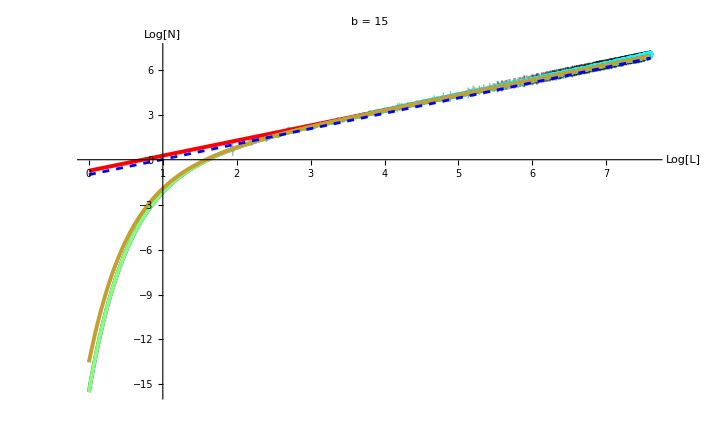

Averaged data fit with errors RGBColor[1, 0, 0]: d_f=1.00890.0016
Averaged data fit with errors and 1+ⅇ^(-2 x)+ⅇ^-x+x RGBColor[0.5, 0, 0.5]: d_f=1.00140.0024

a+c ⅇ^(-x ω)+c2 ⅇ^(-x ω2)+df x  fit  RGBColor[1, Rational[2, 3], 1]: d_f=1.03698Null, Parameters:{a→-0.888619,c→-16.2396,ω→21.3576,df→1.03698}
Averaged data fit with errors and a+c ⅇ^(-x ω)+c2 ⅇ^(-x ω2)+df xnonlinearModel RGBColor[0.5, 1, 0.5]: d_f=-2.10.

Averaged data fit with MaxDevs and a+c ⅇ^(-x ω)+c2 ⅇ^(-x ω2)+df xnonlinearModel RGBColor[0.76, 0.63, 0.19]: d_f=1.0010.005, 
	Parameters: | Estimate | Standard Error | t-Statistic | P-Value
a | -0.683873 | 0.0378191 | -18.0827 | 2.1669×10^-63
c | -10.6915 | 40.1908 | -0.266019 | 0.79028
ω | 2.00031 | 4.07341 | 0.491065 | 0.623489
c2 | -2.14772 | 11.8832 | -0.180737 | 0.856611
ω2 | 0.999919 | 1.20861 | 0.82733 | 0.408249
df | 1.00145 | 0.00451172 | 221.967 | 0.

Result from the litterature (exact with SLE) RGBColor[0, 0, 1]: 127/124 = 1.02419

```mathematica
maxx=Max[rawData[[All,1]]];
maxy=Max[rawData[[All,2]]];

thresholdBelow=0;
thresholdAbove=maxx-0;

Show[{ListPlot[logAveragedWithMaxDev,PlotStyle->{GrayLevel[0],Directive[Opacity[0.3]]},AxesLabel->{"Log[L]","Log[N]"}]
,ListPlot[logAveragedWithErrors,PlotStyle->RGBColor[0, 1, 1]]
(*,Plot[lmp[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, Rational[2, 3], 0],Thickness->0.004}]*)
,Plot[lmAveraged[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[1, 0, 0],Thickness->0.004}]
,Plot[lmpAveraged[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 0, 0.5],Thickness->0.004}]
,Plot[fitFunc/. fitSol,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[1, Rational[2, 3], 1],Thickness->0.004}]
,Plot[nlmAveraged[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 1, 0.5],Thickness->0.004}]

,Plot[nlmMaxDev[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.76, 0.63, 0.19],Thickness->0.004}]

,Plot[x (dfSLE/.bb->b)-1,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, 0, 1],Dashed}]}
,(*PlotRange->All,*)PlotLabel->Row[{" b = ",b}]
(*,Epilog->{Directive[Dashed,GrayLevel[0.5]],
Line[{{Log[thresholdBelow],0},{Log[thresholdBelow],Log[maxy]//N}}]
,Line[{{Log[thresholdAbove],0},{Log[thresholdAbove],Log[maxy]//N}}]}*)
,PlotRange->{All,{0,All}},AxesOrigin->{1,0}]

Print[ (*"Full data - Linear fit : d_f=",Around[Quiet@lm["ParameterTable"][[1]][[1,3,2]],π*lm["ParameterErrors"][[2]]],*)"
Averaged data fit with errors RGBColor[1, 0, 0]: d_f=",Around[Quiet@lmAveraged["ParameterTable"][[1]][[1,3,2]],π*lmAveraged["ParameterErrors"][[2]]],"
Averaged data fit with errors and " ,Total@fitFuncs," RGBColor[0.5, 0, 0.5]: d_f=",Around[Quiet@lmpAveraged["ParameterTable"][[1]][[1,2,2]],π*lmpAveraged["ParameterErrors"][[1]]],"

",fitFunc,"  fit  RGBColor[1, Rational[2, 3], 1]: d_f=",Around[df/.fitSol,Null],", Parameters:",fitSol,"
Averaged data fit with errors and " ,fitFunc,"nonlinearModel RGBColor[0.5, 1, 0.5]: d_f=",Around[Quiet@nlmAveraged["ParameterTable"][[1,1,5,2]],(*π**)Quiet@nlmAveraged["ParameterTable"][[1,1,5,3]]],"

Averaged data fit with MaxDevs and " ,fitFunc,"nonlinearModel RGBColor[0.76, 0.63, 0.19]: d_f=",Around[Quiet@nlmMaxDev["ParameterTable"][[1,1,-1,2]],(*π**)Quiet@nlmMaxDev["ParameterTable"][[1,1,-1,3]]],", 
	",Row[{"Parameters:",Quiet@nlmMaxDev["ParameterTable"]}],(*,"

Full data - ",Total@fitFuncs," fit: d_f=",Around[Quiet@lmp["ParameterTable"][[1]][[1,2,2]],π*lmp["ParameterErrors"][[1]]]*)"

Result from the litterature (exact with SLE) RGBColor[0, 0, 1]: ",(dfSLE/.bb->b)," = ",(dfSLE/.bb->b/1.)]
```

```mathematica
Quiet@lmpAveraged["ParameterTable"][[1]]
Quiet@nlmAveraged["ParameterTable"][[1]]
```

| Estimate | Standard Error | t-Statistic | P-Value
x | 1.05291 | 0.000680.00007 | 1558.168. | BetaRegularized[0.000410.00009,498,1/2]
1 | -0.509589 | 0.00470.0005 | -109.12. | BetaRegularized[0.0780.016,498,1/2]
ⅇ^(-2 x) | -29.6251 | 0.0900.010 | -328.36. | BetaRegularized[0.00910.0020,498,1/2]

| Estimate | Standard Error | t-Statistic | P-Value
a | -0.653659 | 1.36687 | -0.478216 | 0.632601
c | -3.4484 | 95.7668 | -0.0360083 | 0.971283
ω | 1.32346 | 18.4345 | 0.0717928 | 0.942781
df | 0.660756 | 0.190947 | 3.46042 | 0.000562223

```mathematica
Quiet@nlmMaxDev["ParameterTable"][[1,All,1;;3]]//Normal
```

Part::take: Cannot take positions 1 through 3 in Alignment→{Left,Automatic}.

{{,Estimate,Standard Error},{a,-0.719338,0.114184},{c,-30.0531,45.6826},{ω,2.00371,2.09366},{c2,0.718269,15.1915},{ω2,0.887409,5.07186},{df,1.08243,0.0132121}}

# Implementation of Kay’s method to extract a variance from noisy data: mean of batches and variance estimate from there, then mean over estimates

## StdDevEstimate[] definition and tests

```mathematica
(*Check if one can localize the progress variables activeTasks etc
SEE VERSION BELOW WITH MONITOR[]*)
```

```mathematica
ClearAll[StdDevEstimate];

Options[StdDevEstimate]={"print"->False};

StdDevEstimate[data_,binSize_,options:OptionsPattern[]]:=StdDevEstimate[data,binSize,options,0];

StdDevEstimate[data_,binSize_,OptionsPattern[],repeat_:0]:=
Module[{size,locBinSize,repeatNumber,binNumber,scramble,means,stdDevs},

size=Length[data];
locBinSize=binSize;
repeatNumber=repeat;

If[locBinSize>size/2,
Print[Style["### WARNING: binSize too large, defaulting to half the data length ###",RGBColor[1, 0, 0]]];
locBinSize=Floor[size/2]];

binNumber=Floor[size/locBinSize];

If[OptionValue["print"],
Print[Style[" binNumber= ",{RGBColor[0, 0, 1],Bold}],binNumber];];

If[repeatNumber==0,
repeatNumber=Ceiling[size/binNumber];];

If[OptionValue["print"],
Print[Style[" repeatNumber= ",{RGBColor[0, 0, 1],Bold}],repeatNumber];];


(*totalTasks=repeatNumber;
activeTasks={1};
completedCount=0;
startTime=AbsoluteTime[];(*Capture exact start time*)

(*Print the live-updating progress panel with a timer*)FormatTime[sec_]:=With[{s=Round[sec]},StringRiffle[IntegerString[#,10,2]&/@{Quotient[s,3600],Mod[Quotient[s,60],60],Mod[s,60]},":"]];
Print[Panel[Column[{Row[{Style["Task Progress: ",Bold],Dynamic[completedCount]," / ",totalTasks}],Dynamic[ProgressIndicator[completedCount,{0,totalTasks},ImageSize->Large]],(*Dynamic Timer Row*)Dynamic[With[{elapsed=Round[AbsoluteTime[]-startTime]},Row[{Style["Elapsed: ",Gray],FormatTime[elapsed],"   |   ",Style["ETA: ",Gray],If[completedCount>0,With[{remaining=Round[(elapsed/completedCount)*(totalTasks-completedCount)]},FormatTime[remaining]],"Calculating..."]}]]],Row[{Style["Active Worker Queue: ",Gray],Dynamic[Length[activeTasks]]}]},Spacings->1],Background->GrayLevel[0.95],FrameMargins->15]];

(*Actual computation*)
stdDevs=Table[

scramble=RandomSample[data];
scramble=Partition[scramble,UpTo[locBinSize]];
means=Mean/@scramble;
completedCount++;
{N[StandardDeviation[means]/Sqrt[Length[means]]](*,Mean[means]*)}
,repeatNumber
];*)
(*Initialize DynamicModule WITH explicit starting values*)DynamicModule[{totalTasks=repeatNumber,activeTasks={1},completedCount=0,startTime=AbsoluteTime[]},(*Define localized formatting helper*)With[{formatTime=Function[sec,With[{s=Round[sec]},StringRiffle[IntegerString[#,10,2]&/@{Quotient[s,3600],Mod[Quotient[s,60],60],Mod[s,60]},":"]]]},(*Print the progress panel*)Print[Panel[Column[{Row[{Style["Task Progress: ",Bold],Dynamic[completedCount]," / ",totalTasks}],Dynamic[ProgressIndicator[completedCount,{0,totalTasks},ImageSize->Large]],(*Dynamic Timer Row*)Dynamic[With[{elapsed=Round[AbsoluteTime[]-startTime]},Row[{Style["Elapsed: ",Gray],formatTime[elapsed],"   |   ",Style["ETA: ",Gray],If[completedCount>0,With[{remaining=Round[(elapsed/completedCount)*(totalTasks-completedCount)]},formatTime[remaining]],"00:00:00"]}]]],Row[{Style["Active Worker Queue: ",Gray],Dynamic[Length[activeTasks]]}]},Spacings->1],Background->GrayLevel[0.95],FrameMargins->15]];


(*Actual computation*)
stdDevs=Table[scramble=RandomSample[data];
scramble=Partition[scramble,UpTo[locBinSize]];
means=Mean/@scramble;
(*Increment counter:updates dynamic display instantly*)completedCount++;
{N[StandardDeviation[means]/Sqrt[Length[means]]]}
,repeatNumber];

activeTasks={}; (*Clear queue readout when finished*)
]
];



stdDevs={Mean[stdDevs[[All,1]]](*,Mean[stdDevs[[All,2]]]*)};

If[OptionValue["print"],
(*Print[Style[" Mean from batching= ",{RGBColor[0, 0, 1],Bold}],stdDevs[[2]]//N];*)
Print[Style[" Std deviation/√N estimate= ",{RGBColor[0, 0, 1],Bold}],stdDevs[[1]]//N];];
stdDevs[[1]]*√size
]
```

```mathematica
ClearAll[StdDevEstimate];

Options[StdDevEstimate]={"print"->False};

StdDevEstimate[data_,binSize_,options:OptionsPattern[]]:=StdDevEstimate[data,binSize,options,0];

StdDevEstimate[data_,binSize_,OptionsPattern[],repeat_:0]:=Module[{size,locBinSize,repeatNumber,binNumber,scramble,means,stdDevs,completedCount=0,startTime=AbsoluteTime[],formatTime},

size=Length[data];
locBinSize=binSize;
repeatNumber=repeat;

If[locBinSize>size/2,Print[Style["### WARNING: binSize too large, defaulting to half the data length ###",RGBColor[1,0,0]]];
locBinSize=Floor[size/2]];

binNumber=Floor[size/locBinSize];

If[OptionValue["print"],Print[Style[" binNumber= ",{RGBColor[0,0,1],Bold}],binNumber]];
If[repeatNumber==0,repeatNumber=Ceiling[size/binNumber]];

If[OptionValue["print"],Print[Style[" repeatNumber= ",{RGBColor[0,0,1],Bold}],repeatNumber]];

formatTime[sec_]:=With[{s=Round[sec]},StringRiffle[IntegerString[#,10,2]&/@{Quotient[s,3600],Mod[Quotient[s,60],60],Mod[s,60]},":"]];

(*Monitor tracks the calculation and shows a live panel*)
Monitor[stdDevs=Table[scramble=RandomSample[data];
scramble=Partition[scramble,UpTo[locBinSize]];
means=Mean/@scramble;
completedCount++;
{N[StandardDeviation[means]/Sqrt[Length[means]]]},repeatNumber],
(*Progress panel layout inside Monitor*)
Panel[Column[{Row[{Style["Task Progress: ",Bold],completedCount," / ",repeatNumber}],ProgressIndicator[completedCount,{0,repeatNumber},ImageSize->Large],With[{elapsed=Round[AbsoluteTime[]-startTime]},Row[{Style["Elapsed: ",Gray],formatTime[elapsed],"   |   ",Style["ETA: ",Gray],If[completedCount>0,With[{remaining=Round[(elapsed/completedCount)*(repeatNumber-completedCount)]},formatTime[remaining]],"00:00:00"]}]]},Spacings->1],Background->GrayLevel[0.95],FrameMargins->15]
];

stdDevs={Mean[stdDevs[[All,1]]]};

If[OptionValue["print"],Print[Style[" Std deviation/\!\(\*SqrtBox[\(N\)]\) estimate= ",{RGBColor[0,0,1],Bold}],stdDevs[[1]]//N]];

stdDevs[[1]]*Sqrt[size]]
```

examples

```mathematica
Partition[test,UpTo[4]]
```

{{1,2,3,4},{5,6,7,8},{9}}

```mathematica
test={1,2,3,4,5,6,7,8,9};
StdDevEstimate[test,3,"print"->True]//N
Mean[test]//N
StandardDeviation[test]/Sqrt[Length[test]]//N
```

binNumber= 3

repeatNumber= 3

Std deviation/√N estimate= 0.669833

2.0095

5.

0.912871

### Primary test: idd gaussian variables: checked!

```mathematica
normData=Table[RandomReal[NormalDistribution[]],10000000];
normData=Developer`ToPackedArray[normData];
```

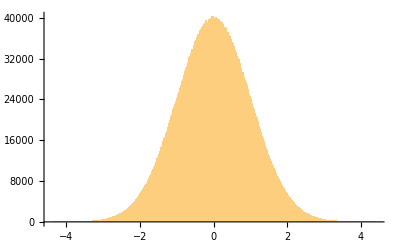

```mathematica
Histogram[normData,1000]
```

```mathematica
Mean[normData]
StandardDeviation[normData]
%/Sqrt[Length[normData]]

Sqrt[Mean[normData^2]-Mean[normData]^2]
```

0.000296043

1.00017

0.000316281

1.00017

```mathematica
StdDevEstimate[normData,10,"print"->True]//N
```

binNumber= 1000000

repeatNumber= 10

Std deviation/√N estimate= 0.000316407

1.00057

## Application to b=4

```mathematica
b=4;

rawData=Import["data4Sqaure-AfterValidation.mx"];

Length[rawData]
```

10827464

```mathematica
(*1. Gather rows by their first element (x) at C-speed*)
gathered=GatherBy[rawData,First];

(*2. Extract the unique X values directly from the gathered groups*)
xValues=gathered[[All,1,1]];

(*3. Extract the Y values for each group*)
yGroups=gathered[[All,All,2]];

(*4. Map Mean and StandardDeviation across the groups in bulk*)
means=Mean/@yGroups/. 0.->1.0*^-8;

(*Standard deviation throws an error/indeterminacy if length is 1,so we replace Indeterminate with 0 globally at the end*)
stdDevs=StandardDeviation/@yGroups/. Indeterminate->1.0*^-8;
stdDevs=stdDevs/. 0.->1.0*^-8;

(* Maximum deviation*)
maxDevs=MapThread[Max[Abs[#1-#2]]&,{means//N,yGroups}];


(*5. Combine them using the Threaded Around wrapper*)

averaged=Transpose[{xValues,means}];
averagedWithErrors=Transpose[{xValues,MapThread[Around,{means,stdDevs}]}];
averagedWithMaxDev=Transpose[{xValues,MapThread[Around,{means,maxDevs}]}];
```

```mathematica
(*NOT USING IT

 Remove the √N factor from the StdDev estimates*)
(*MapThread[Times[#1,√#2]&,{stdDevs,yGroups}]

averagedWithErrors=Transpose[{xValues,MapThread[Around,{means,%}]}];*)
```

```mathematica
(*Standard deviation with my code (Kay's trick for better estimate)*)
stdDevsEstimated=StdDevEstimate[#,280,"print"->tTrue]&/@yGroups/. Indeterminate->1.0*^-8;
stdDevsEstimated=stdDevsEstimated/. 0.->1.0*^-8;

averagedWithEstimatedStdDevs=Transpose[{xValues,MapThread[Around,{means,stdDevsEstimated}]}];
```

### WARNING: binSize too large, defaulting to half the data length ###

### WARNING: binSize too large, defaulting to half the data length ###

### WARNING: binSize too large, defaulting to half the data length ###

«797 more identical outputs»

Fixed size analysis to try and get the best parameters (e.g. bin size) -> Around 280-290 (with the estimate it’s a bit bigger)

```mathematica
(* Take the 11th element which contains many points. As it can be seen in the Histogram below, the distribution is far from being symmetric *)
```

```mathematica
gathered[[1]]
```

{{1001,836},{1001,889},{1001,843},{1001,818},{1001,880},{1001,844},{1001,874},{1001,852},{1001,851},{1001,833},{1001,881},{1001,767},{1001,797},{1001,818},{1001,780},{1001,928},{1001,925},{1001,865},{1001,822},{1001,794},{1001,838},{1001,846},{1001,846},{1001,945},{1001,951},{1001,990},{1001,849},{1001,849},{1001,988},{1001,870},{1001,875},{1001,829},{1001,855},{1001,873},{1001,945},{1001,855},{1001,828},{1001,886},{1001,861},{1001,896}}

```mathematica
Ordering[gathered][[-1]]
gathered[[%]]
```

557

{40,40,100040}

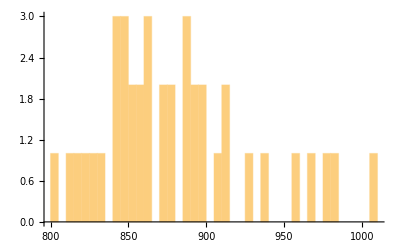
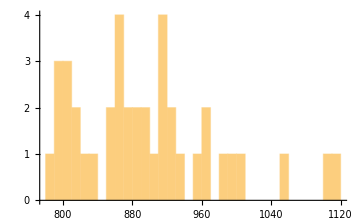
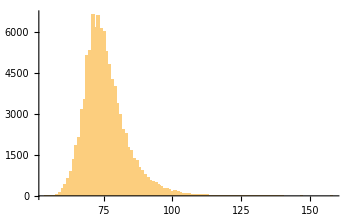

```mathematica
gathered[[9;;11]];
Length/@%
histoData=%%[[All,All,2]];
Histogram[#,Length[#],PlotRange->All]&/@%
```

```mathematica
Skewness[histoData]//N
```

1.34674

identification of best binSize -> best of both skewness ans kurtosis:  289

2001

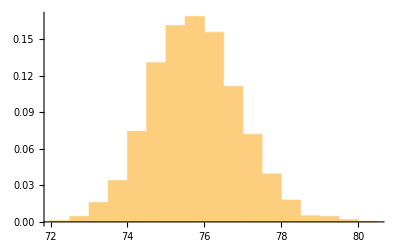

0.206154

3.1355

```mathematica
Partition[histoData,UpTo[50]];
Length@%
partData=Mean/@%%;
Histogram[partData,Automatic,"Probability",PlotRange->All]
Skewness[partData]//N
Kurtosis[partData]//N
```

```mathematica
{x,y}=Transpose
Clear[x,y]
```

```mathematica
listOfBinSizes={listOfBinSizesSkewness,listOfBinSizesKurtosis}=Transpose[Table[
part=Partition[histoData,UpTo[binSize]];
part=Mean/@part;
{{Abs[Skewness[part]//N],binSize},{Abs[Kurtosis[part]//N],binSize}}
,{binSize,1,300,2}]];
```

```mathematica
(Ordering/@{listOfBinSizesSkewness,listOfBinSizesKurtosis})[[All,1;;10]]
Part[listOfBinSizesSkewness,#]&/@%[[1]]
Part[listOfBinSizesKurtosis,#]&/@%%[[2]]
```

{{143,76,45,149,83,145,91,80,125,127},{128,117,142,109,145,126,89,92,150,97}}

{{0.000760007,285},{0.00123015,151},{0.00177641,89},{0.00179429,297},{0.00200697,165},{0.00322281,289},{0.00380895,181},{0.00433727,159},{0.00479889,249},{0.00709833,253}}

{{2.60344,255},{2.63465,233},{2.63987,283},{2.64391,217},{2.6664,289},{2.67801,251},{2.73075,177},{2.73544,183},{2.74031,299},{2.76536,193}}

{0.000760007,285}

{2.60344,255}

{0.000760007,285}

352

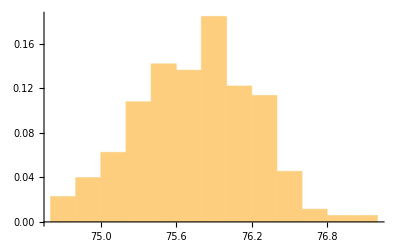

0.000760007

2.76697

{2.60344,255}

393

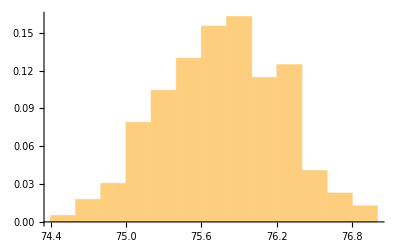

-0.051841

2.60344

```mathematica
listOfBinSizesSkewness[[143]]

Partition[histoData,UpTo[%[[2]]]];
Length@%
partData=Mean/@%%;
Histogram[partData,Automatic,"Probability",PlotRange->All]
Skewness[partData]//N
Kurtosis[partData]//N


listOfBinSizesKurtosis[[128]]

Partition[histoData,UpTo[%[[2]]]];
Length@%
partData=Mean/@%%;
Histogram[partData,Automatic,"Probability",PlotRange->All]
Skewness[partData]//N
Kurtosis[partData]//N
```

```mathematica
(*Best of both worlds*)
```

{0.00322281,289}

347

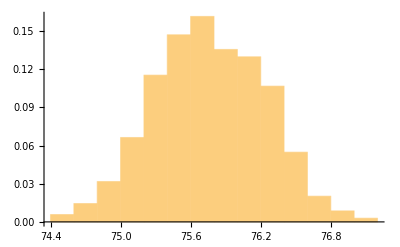

-0.00322281

2.6664

```mathematica
listOfBinSizesSkewness[[145]]

Partition[histoData,UpTo[%[[2]]]];
Length@%
partData=Mean/@%%;
Histogram[partData,Automatic,"Probability",PlotRange->All]
Skewness[partData]//N
Kurtosis[partData]//N
```

StdDev Difference: with the estimate it’s a bit bigger

```mathematica
StandardDeviation[histoData]//N
```

8.08364

```mathematica
StdDevEstimate[histoData,289,"print"->True]
```

4 √(5109125662/1250987695)

binNumber= 346

repeatNumber= 290

Std deviation/√N estimate= 0.0257372

8.14044

Take the Log

```mathematica
logAveraged=Log[averaged];
logAveragedWithErrors=Log[averagedWithErrors]/. 0->Around[1.0*^-6,1.0*^-6];
logAveragedWithEstimatedStdDevs=Log[averagedWithEstimatedStdDevs]/. 0->Around[1.0*^-6,1.0*^-6];
logAveragedWithMaxDev=Log[averagedWithMaxDev]/. 0->Around[1.0*^-6,1.0*^-6];
```

```mathematica
logAveragedWithEstimatedStdDevs[[1]]
```

{Log[1001],6.760.04}

```mathematica
(*Check which error is bigger*)
(Part[#,All,2,2]&/@{logAveragedWithEstimatedStdDevs,-logAveragedWithErrors});
Mean[(#[[1]]-#[[2]]&@%)]
```

-0.0114609

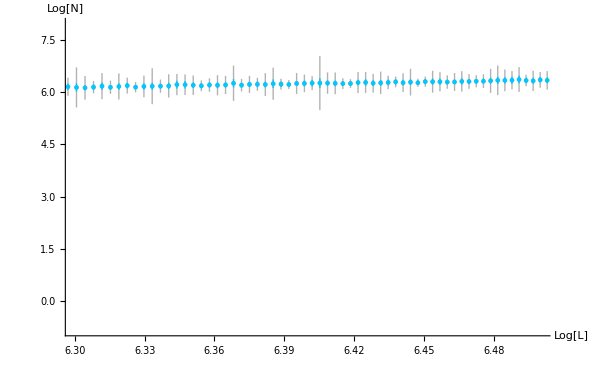

```mathematica
Show[{ListPlot[logAveragedWithMaxDev,PlotStyle->{GrayLevel[0],Directive[Opacity[0.3]]},AxesLabel->{"Log[L]","Log[N]"}]
,ListPlot[logAveragedWithErrors,PlotStyle->RGBColor[0, 0.78, 1]]
(*,ListPlot[logAveragedWithEstimatedStdDevs,PlotStyle->{RGBColor[1, 0.55, 1],Directive[Opacity[0.6]]}]*)
}
,PlotRange->{{6.3,6.5},All},AxesOrigin->{4,0}]

(*Show[{ListPlot[logAveragedWithMaxDev,PlotStyle->{GrayLevel[0],Directive[Opacity[0.3]]},AxesLabel->{"Log[L]","Log[N]"}]
,ListPlot[logAveragedWithErrors,PlotStyle->RGBColor[0, 0.78, 1]]
(*,ListPlot[logAveragedWithEstimatedStdDevs,PlotStyle->{RGBColor[1, 0.55, 1],Directive[Opacity[0.6]]}]*)
}
,PlotRange->{All,{0,All}},AxesOrigin->{1,0}]
*)
```

```mathematica
logAveragedWithErrors//Length
weights=Map[#[[2]]["Uncertainty"]&,logAveragedWithErrors];
%//Length
Position[weights,_?(Element[#,Reals]=!=True&)]


weights=Map[#[[2]]["Uncertainty"]&,logAveragedWithMaxDev];
%//Length
Position[weights,_?(Element[#,Reals]=!=True&)]


weights=Map[#[[2]]["Uncertainty"]&,logAveragedWithEstimatedStdDevs];
%//Length
Position[weights,_?(Element[#,Reals]=!=True&)]
```

999

999

{{0}}

999

{{0}}

999

{{0}}

### Scan through different shifts to find the best linear fit, i.e. that maximizes AdjustedRSquared It seems to always be shift=4 (also 4.1 if the first point is included)

#### With errors from StandardDeviation[]

```mathematica
listOfFits=Table[
shift:=Plus[{-i,0},#]&;

logAveragedWithErrorsShifted=Log[shift/@averagedWithErrors]/. {a_,0}->{a,Around[1.0*^-6,1.0*^-6]};
fitFunc=a+df  x;lmAveragedWithErrorsShifted=NonlinearModelFit[Select[logAveragedWithErrorsShifted,#[[1]]>=0&],{fitFunc(*,{-2<a<2,0<ω<28}*)},{a,(*c,ω,*)df},x]
,
{i,-5,5,0.1}];
```

```mathematica
Length[listOfFits]
```

101

```mathematica
#["AdjustedRSquared"]&/@listOfFits
best=Ordering[%,-1]
listOfFits[[%]]
```

{0.998298,0.998321,0.998344,0.998367,0.99839,0.998413,0.998436,0.998459,0.998482,0.998505,0.998529,0.998552,0.998575,0.998598,0.998621,0.998644,0.998667,0.99869,0.998713,0.998737,0.99876,0.998783,0.998806,0.998829,0.998852,0.998875,0.998898,0.998921,0.998944,0.998967,0.99899,0.999013,0.999036,0.999059,0.999082,0.999105,0.999127,0.99915,0.999173,0.999196,0.999218,0.999241,0.999263,0.999286,0.999308,0.99933,0.999353,0.999375,0.999397,0.999419,0.99944,0.999462,0.999484,0.999505,0.999527,0.999548,0.999569,0.99959,0.99961,0.999631,0.999651,0.999671,0.999691,0.999711,0.99973,0.999749,0.999768,0.999786,0.999804,0.999821,0.999838,0.999855,0.999871,0.999887,0.999901,0.999916,0.999929,0.999941,0.999953,0.999964,0.999973,0.999981,0.999988,0.999993,0.999996,0.999997,0.999995,0.999991,0.999983,0.999971,0.999954,0.999997,0.999997,0.999997,0.999997,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996}

{92}

{FittedModel[…]}

Best position is with shift 4.1

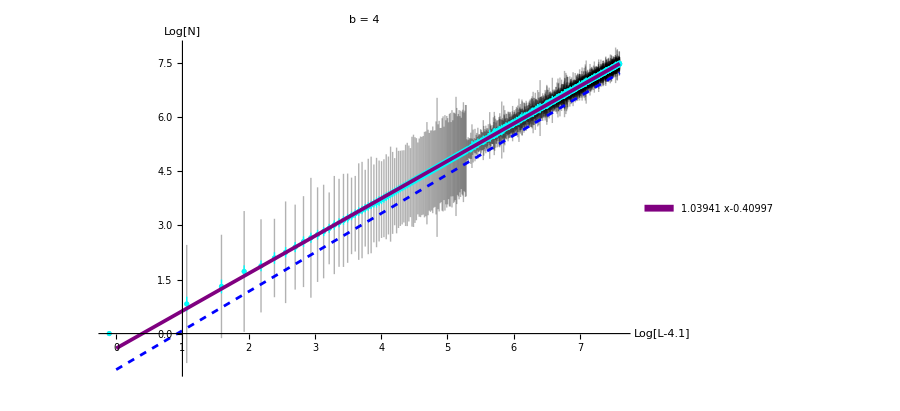

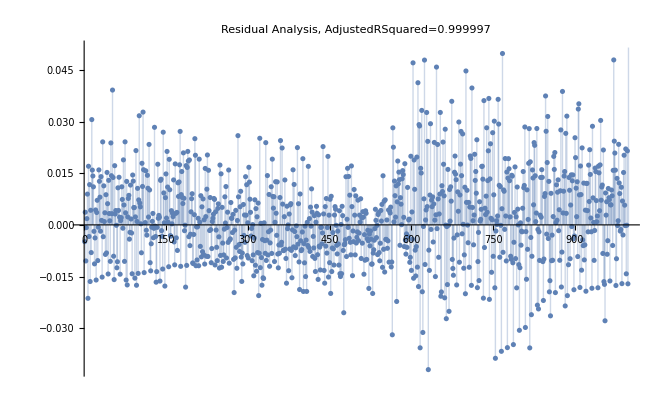

```mathematica
(best[[1]]-51)/10//N;
Print["Best position is with shift ",%]
shift:=Plus[{-(best[[1]]-51)/10//N,0},#]&

logAveragedWithMaxDevShifted=Log[shift/@averagedWithMaxDev]/.{a_,0}->{a,Around[1.0*^-6,1.0*^-6]};
logAveragedWithErrorsShifted=Log[shift/@averagedWithErrors]/. {a_,0}->{a,Around[1.0*^-6,1.0*^-6]};


Show[{ListPlot[logAveragedWithMaxDevShifted,PlotStyle->{GrayLevel[0],Directive[Opacity[0.3]]},AxesLabel->{Row[{"Log[L-",(best[[1]]-51)/10//N,"]"}],"Log[N]"}]
,ListPlot[logAveragedWithErrorsShifted,PlotStyle->RGBColor[0, 1, 1]]
(*,ListPlot[logAveragedWithEstimatedStdDevsShifted,PlotStyle->{RGBColor[1, 0.55, 1],Directive[Opacity[0.3]]}]*)

(*,Plot[lmp[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, Rational[2, 3], 0],Thickness->0.004}]*)

,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 0, 0.5],Thickness->0.004},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],{Right,Top}]]&@(listOfFits[[best[[1]]]][x])

,Plot[x (dfSLE/.bb->b)-1,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, 0, 1],Dashed}]}
,(*PlotRange->All,*)PlotLabel->Row[{" b = ",b}]
(*,Epilog->{Directive[Dashed,GrayLevel[0.5]],
Line[{{Log[thresholdBelow],0},{Log[thresholdBelow],Log[maxy]//N}}]
,Line[{{Log[thresholdAbove],0},{Log[thresholdAbove],Log[maxy]//N}}]}*)
,PlotRange->{All,{0,All}},AxesOrigin->{1,0}]

ListPlot[listOfFits[[best[[1]]]]["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis, AdjustedRSquared=",listOfFits[[best[[1]]]]["AdjustedRSquared"]}]]
```

#### With errors from MaxDev[]

```mathematica
listOfFits=Table[
shift:=Plus[{-i,0},#]&;

logAveragedWithMaxDevShifted=Log[shift/@averagedWithErrors]/. {a_,0}->{a,Around[1.0*^-6,1.0*^-6]};
fitFunc=a+df  x;lmAveragedWithMaxDevShifted=NonlinearModelFit[Select[logAveragedWithMaxDevShifted,#[[1]]>0&],{fitFunc(*,{-2<a<2,0<ω<28}*)},{a,(*c,ω,*)df},x]
,
{i,-5,5,0.1}];
```

```mathematica
Length[listOfFits]
```

101

```mathematica
#["AdjustedRSquared"]&/@listOfFits
best=Ordering[%,-1]
listOfFits[[%]]
```

{0.998298,0.998321,0.998344,0.998367,0.99839,0.998413,0.998436,0.998459,0.998482,0.998505,0.998529,0.998552,0.998575,0.998598,0.998621,0.998644,0.998667,0.99869,0.998713,0.998737,0.99876,0.998783,0.998806,0.998829,0.998852,0.998875,0.998898,0.998921,0.998944,0.998967,0.99899,0.999013,0.999036,0.999059,0.999082,0.999105,0.999127,0.99915,0.999173,0.999196,0.999218,0.999241,0.999263,0.999286,0.999308,0.99933,0.999353,0.999375,0.999397,0.999419,0.99944,0.999462,0.999484,0.999505,0.999527,0.999548,0.999569,0.99959,0.99961,0.999631,0.999651,0.999671,0.999691,0.999711,0.99973,0.999749,0.999768,0.999786,0.999804,0.999821,0.999838,0.999855,0.999871,0.999887,0.999901,0.999916,0.999929,0.999941,0.999953,0.999964,0.999973,0.999981,0.999988,0.999993,0.999996,0.999997,0.999995,0.999991,0.999983,0.999971,0.999997,0.999997,0.999997,0.999997,0.999997,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996}

{91}

{FittedModel[…]}

Best position is with shift 4.

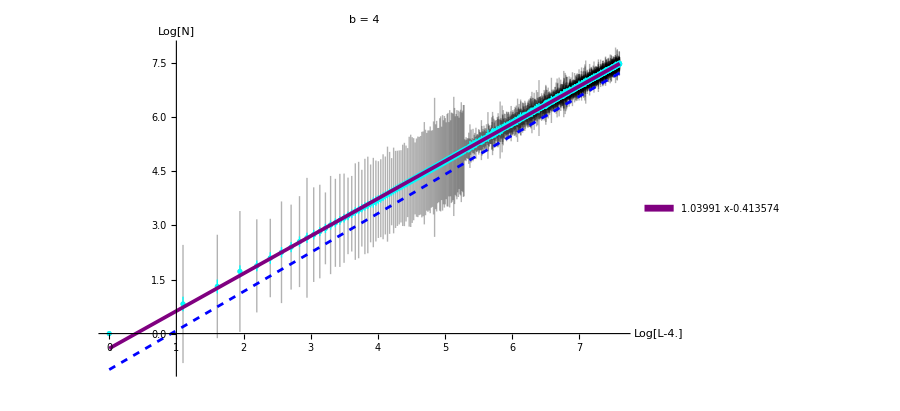

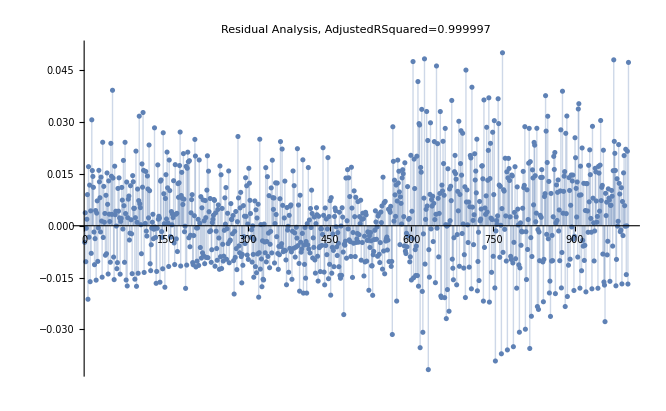

```mathematica
(best[[1]]-51)/10//N;
Print["Best position is with shift ",%]
shift:=Plus[{-(best[[1]]-51)/10//N,0},#]&

logAveragedWithMaxDevShifted=Log[shift/@averagedWithMaxDev]/.{a_,0}->{a,Around[1.0*^-6,1.0*^-6]};
logAveragedWithErrorsShifted=Log[shift/@averagedWithErrors]/. {a_,0}->{a,Around[1.0*^-6,1.0*^-6]};


Show[{ListPlot[logAveragedWithMaxDevShifted,PlotStyle->{GrayLevel[0],Directive[Opacity[0.3]]},AxesLabel->{Row[{"Log[L-",(best[[1]]-51)/10//N,"]"}],"Log[N]"}]
,ListPlot[logAveragedWithErrorsShifted,PlotStyle->RGBColor[0, 1, 1]]
(*,ListPlot[logAveragedWithEstimatedStdDevsShifted,PlotStyle->{RGBColor[1, 0.55, 1],Directive[Opacity[0.3]]}]*)

(*,Plot[lmp[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, Rational[2, 3], 0],Thickness->0.004}]*)

,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 0, 0.5],Thickness->0.004},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],{Right,Top}]]&@(listOfFits[[best[[1]]]][x])

,Plot[x (dfSLE/.bb->b)-1,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, 0, 1],Dashed}]}
,(*PlotRange->All,*)PlotLabel->Row[{" b = ",b}]
(*,Epilog->{Directive[Dashed,GrayLevel[0.5]],
Line[{{Log[thresholdBelow],0},{Log[thresholdBelow],Log[maxy]//N}}]
,Line[{{Log[thresholdAbove],0},{Log[thresholdAbove],Log[maxy]//N}}]}*)
,PlotRange->{All,{0,All}},AxesOrigin->{1,0}]

ListPlot[listOfFits[[best[[1]]]]["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis, AdjustedRSquared=",listOfFits[[best[[1]]]]["AdjustedRSquared"]}]]
```

### Take the Log WITH A SHIFT

```mathematica
shift:=Plus[{-4,0},#]&;

logAveragedShifted=Log[shift/@averaged];
logAveragedWithErrorsShifted=Log[shift/@averagedWithErrors]/. {a_,0}->{a,Around[1.0*^-6,1.0*^-6]};
logAveragedWithEstimatedStdDevsShifted=Log[shift/@averagedWithEstimatedStdDevs]/. {a_,0}->{a,Around[1.0*^-6,1.0*^-6]};
logAveragedWithMaxDevShifted=Log[shift/@averagedWithMaxDev]/.{a_,0}->{a,Around[1.0*^-6,1.0*^-6]};
```

```mathematica
fitFunc=a+df x;
lmAveragedShifted=NonlinearModelFit[logAveragedShifted,{fitFunc(*,{-2<a<2,0<ω<28}*)},{a,(*c,ω,*)df},x];
lmAveragedWithErrorsShifted=NonlinearModelFit[Select[logAveragedWithErrorsShifted,#[[1]]>0&],{fitFunc(*,{-2<a<2,0<ω<28}*)},{a,(*c,ω,*)df},x];
lmAveragedWithEstimatedStdDevsShifted=NonlinearModelFit[Select[logAveragedWithEstimatedStdDevsShifted,#[[1]]>0&],{fitFunc(*,{-2<a<2,0<ω<28}*)},{a,(*c,ω,*)df},x];
lmAveragedWithMaxDevShifted=NonlinearModelFit[Select[logAveragedWithMaxDevShifted,#[[1]]>0&],{fitFunc(*,{-2<a<2,0<ω<28}*)},{a,(*c,ω,*)df},x];


Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@lmAveragedShifted
Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@lmAveragedWithErrorsShifted 
Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@lmAveragedWithEstimatedStdDevsShifted 
Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@lmAveragedWithMaxDevShifted
```

lmAveragedShifted with a+df x: -0.397653+1.03792 x

lmAveragedWithErrorsShifted with a+df x: -0.413574+1.03991 x

lmAveragedShifted with a+df x: -0.399773+1.0382 x

lmAveragedWithErrorsShifted with a+df x: -0.412214+1.03972 x

lmAveragedWithEstimatedStdDevsShifted with a+df x: -0.407184+1.03903 x

lmAveragedWithMaxDevShifted with a+df x: -0.372707+1.03416 x

lmAveragedWithEstimatedStdDevsShifted with a+df x: -0.412908+1.03982 x

lmAveragedWithMaxDevShifted with a+df x: -0.390918+1.03668 x

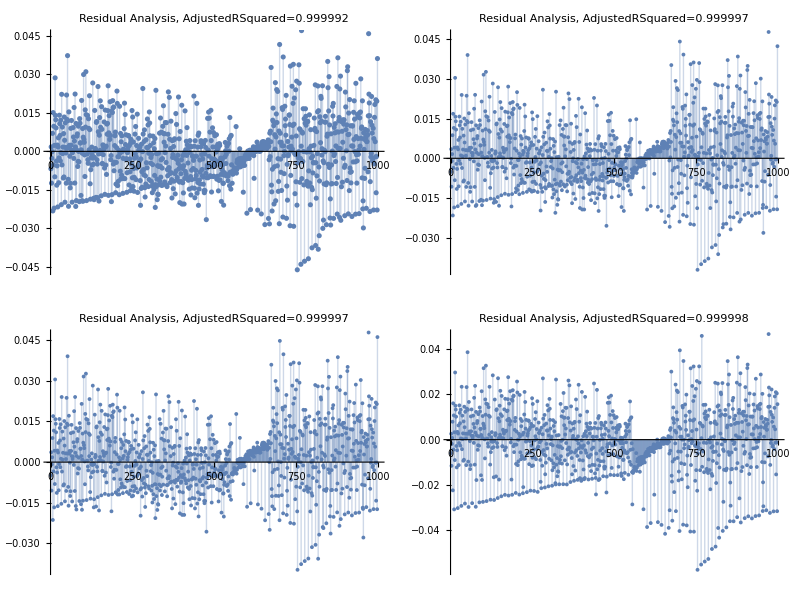

```mathematica
synchronizedPlots=Map[Show[#,ImageSize->500]&,{ListPlot[lmAveragedShifted["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis, AdjustedRSquared=",lmAveragedShifted["AdjustedRSquared"]}]]
,ListPlot[lmAveragedWithErrorsShifted["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis, AdjustedRSquared=",lmAveragedWithErrorsShifted["AdjustedRSquared"]}]]
,ListPlot[lmAveragedWithEstimatedStdDevsShifted["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis, AdjustedRSquared=",lmAveragedWithEstimatedStdDevsShifted["AdjustedRSquared"]}]]
,ListPlot[lmAveragedWithMaxDevShifted["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis, AdjustedRSquared=",lmAveragedWithMaxDevShifted["AdjustedRSquared"]}]]}];

Multicolumn[synchronizedPlots,2,Appearance->"Framed"]
```

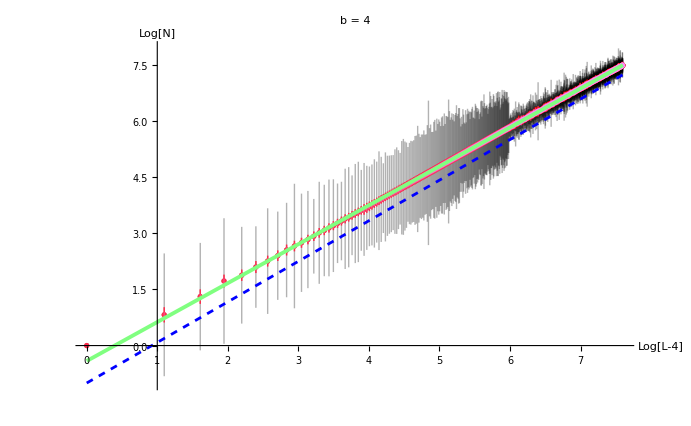

```mathematica
Show[{ListPlot[logAveragedWithMaxDevShifted,PlotStyle->{GrayLevel[0],Directive[Opacity[0.3]]},AxesLabel->{"Log[L-4]","Log[N]"}]
,ListPlot[logAveragedWithErrorsShifted,PlotStyle->RGBColor[1, 0, 0]]
,ListPlot[logAveragedWithEstimatedStdDevsShifted,PlotStyle->{RGBColor[1, 0.55, 1],Directive[Opacity[0.3]]}]

(*,Plot[lmp[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, Rational[2, 3], 0],Thickness->0.004}]*)

,Plot[lmAveragedWithErrorsShifted[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 1, 0.5],Thickness->0.004}]

,Plot[x (dfSLE/.bb->b)-1,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, 0, 1],Dashed}]}
,(*PlotRange->All,*)PlotLabel->Row[{" b = ",b}]
(*,Epilog->{Directive[Dashed,GrayLevel[0.5]],
Line[{{Log[thresholdBelow],0},{Log[thresholdBelow],Log[maxy]//N}}]
,Line[{{Log[thresholdAbove],0},{Log[thresholdAbove],Log[maxy]//N}}]}*)
,PlotRange->{{5,8},{0,All}},AxesOrigin->{1,0}]
```

#### Check with enforced Minimum

```mathematica
fitFunc=a+df x;
lmAveragedShiftedGlobal=NonlinearModelFit[logAveragedShifted,{fitFunc(*,{-2<a<2,0<ω<28}*)},{a,(*c,ω,*)df},x,Method->"NMinimize"];
lmAveragedWithErrorsShiftedGlobal=NonlinearModelFit[Select[logAveragedWithErrorsShifted,#[[1]]>0&],{fitFunc(*,{-2<a<2,0<ω<28}*)},{a,(*c,ω,*)df},x,Method->"NMinimize"];
lmAveragedWithEstimatedStdDevsShiftedGlobal=NonlinearModelFit[Select[logAveragedWithEstimatedStdDevsShifted,#[[1]]>0&],{fitFunc(*,{-2<a<2,0<ω<28}*)},{a,(*c,ω,*)df},x,Method->"NMinimize"];
lmAveragedWithMaxDevShiftedGlobal=NonlinearModelFit[Select[logAveragedWithMaxDevShifted,#[[1]]>0&],{fitFunc(*,{-2<a<2,0<ω<28}*)},{a,(*c,ω,*)df},x,Method->"NMinimize"];


Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@lmAveragedShiftedGlobal
Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@lmAveragedWithErrorsShiftedGlobal 
Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@lmAveragedWithEstimatedStdDevsShiftedGlobal 
Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@lmAveragedWithMaxDevShiftedGlobal

Print[]
Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@lmAveragedShifted
Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@lmAveragedWithErrorsShifted 
Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@lmAveragedWithEstimatedStdDevsShifted 
Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@lmAveragedWithMaxDevShifted
```

lmAveragedShiftedGlobal with a+df x: -0.397651+1.03792 x

lmAveragedWithErrorsShiftedGlobal with a+df x: -0.41357+1.0399 x

NonlinearModelFit::lmnl: The model a+df x is linear in the parameters {a,df}, but a nonlinear method or non-Euclidean norm was specified, so nonlinear methods will be used.

lmAveragedShiftedGlobal with a+df x: -0.399771+1.0382 x

lmAveragedWithErrorsShiftedGlobal with a+df x: -0.41221+1.03972 x

lmAveragedWithEstimatedStdDevsShiftedGlobal with a+df x: -0.407178+1.03902 x

lmAveragedWithMaxDevShiftedGlobal with a+df x: -0.372695+1.03415 x

lmAveragedShifted with a+df x: -0.399773+1.0382 x

lmAveragedWithErrorsShifted with a+df x: -0.412214+1.03972 x

lmAveragedWithEstimatedStdDevsShifted with a+df x: -0.407184+1.03903 x

lmAveragedWithMaxDevShifted with a+df x: -0.372707+1.03416 x

lmAveragedWithEstimatedStdDevsShiftedGlobal with a+df x: -0.412897+1.03982 x

lmAveragedWithMaxDevShiftedGlobal with a+df x: -0.39091+1.03667 x

lmAveragedShifted with a+df x: -0.397653+1.03792 x

lmAveragedWithErrorsShifted with a+df x: -0.413574+1.03991 x

lmAveragedWithEstimatedStdDevsShifted with a+df x: -0.412908+1.03982 x

lmAveragedWithMaxDevShifted with a+df x: -0.390918+1.03668 x

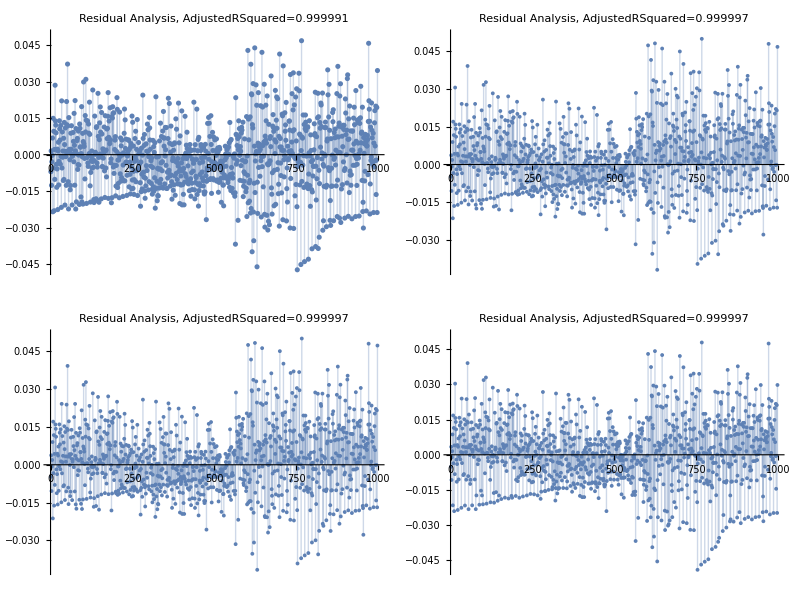

```mathematica
synchronizedPlots=Map[Show[#,ImageSize->500]&,{ListPlot[lmAveragedShifted["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis, AdjustedRSquared=",lmAveragedShifted["AdjustedRSquared"]}]]
,ListPlot[lmAveragedWithErrorsShifted["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis, AdjustedRSquared=",lmAveragedWithErrorsShifted["AdjustedRSquared"]}]]
,ListPlot[lmAveragedWithEstimatedStdDevsShifted["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis, AdjustedRSquared=",lmAveragedWithEstimatedStdDevsShifted["AdjustedRSquared"]}]]
,ListPlot[lmAveragedWithMaxDevShifted["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis, AdjustedRSquared=",lmAveragedWithMaxDevShifted["AdjustedRSquared"]}]]}];

Multicolumn[synchronizedPlots,2,Appearance->"Framed"]
```

#### χ^2 with analytical b (from SLE)

```mathematica
dfSLE/.bb->b
```

```mathematica
fitFunc=a+(dfSLE/.bb->b) x;
lmAveragedShiftedSLE=NonlinearModelFit[logAveragedShifted,{fitFunc(*,{-2<a<2,0<ω<28}*)},{a,(*c,ω,*)df},x,Method->"NMinimize"];
lmAveragedWithErrorsShiftedSLE=NonlinearModelFit[Select[logAveragedWithErrorsShifted,#[[1]]>0&],{fitFunc(*,{-2<a<2,0<ω<28}*)},{a,(*c,ω,*)df},x,Method->"NMinimize"];
lmAveragedWithEstimatedStdDevsShiftedSLE=NonlinearModelFit[Select[logAveragedWithEstimatedStdDevsShifted,#[[1]]>0&],{fitFunc(*,{-2<a<2,0<ω<28}*)},{a,(*c,ω,*)df},x,Method->"NMinimize"];
lmAveragedWithMaxDevShiftedSLE=NonlinearModelFit[Select[logAveragedWithMaxDevShifted,#[[1]]>0&],{fitFunc(*,{-2<a<2,0<ω<28}*)},{a,(*c,ω,*)df},x,Method->"NMinimize"];


Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@lmAveragedShiftedSLE
Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@lmAveragedWithErrorsShiftedSLE 
Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@lmAveragedWithEstimatedStdDevsShiftedSLE 
Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@lmAveragedWithMaxDevShiftedSLE
```

NonlinearModelFit::lmnl: The model a+(13 x)/12 is linear in the parameters {a,df}, but a nonlinear method or non-Euclidean norm was specified, so nonlinear methods will be used.

lmAveragedShiftedSLE with a+(13 x)/12: -0.69741+(13 x)/12

lmAveragedWithErrorsShiftedSLE with a+(13 x)/12: -0.712643+(13 x)/12

lmAveragedWithEstimatedStdDevsShiftedSLE with a+(13 x)/12: -0.713206+(13 x)/12

lmAveragedWithMaxDevShiftedSLE with a+(13 x)/12: -0.717284+(13 x)/12

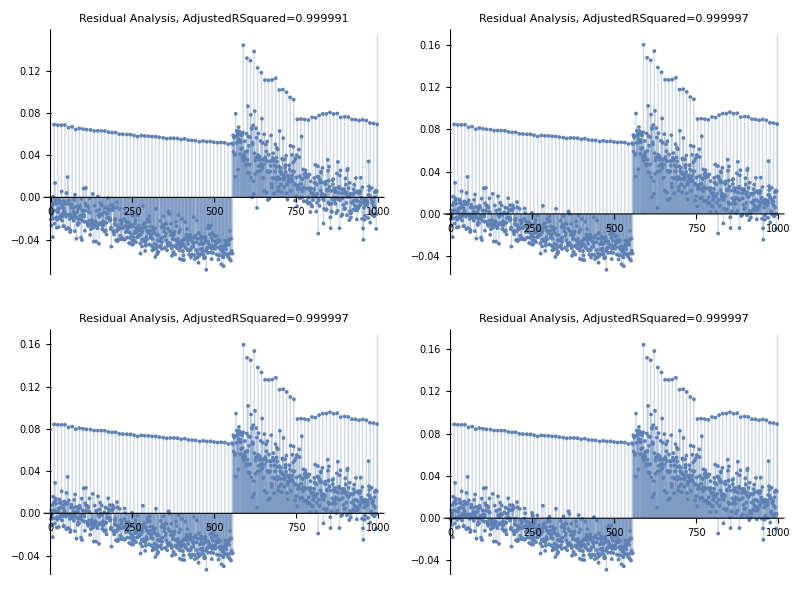

```mathematica
synchronizedPlots=Map[Show[#,ImageSize->500]&,{ListPlot[lmAveragedShiftedSLE["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis, AdjustedRSquared=",lmAveragedShifted["AdjustedRSquared"]}]]
,ListPlot[lmAveragedWithErrorsShiftedSLE["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis, AdjustedRSquared=",lmAveragedWithErrorsShifted["AdjustedRSquared"]}]]
,ListPlot[lmAveragedWithEstimatedStdDevsShiftedSLE["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis, AdjustedRSquared=",lmAveragedWithEstimatedStdDevsShifted["AdjustedRSquared"]}]]
,ListPlot[lmAveragedWithMaxDevShiftedSLE["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis, AdjustedRSquared=",lmAveragedWithMaxDevShifted["AdjustedRSquared"]}]]}];

Multicolumn[synchronizedPlots,2,Appearance->"Framed"]
```

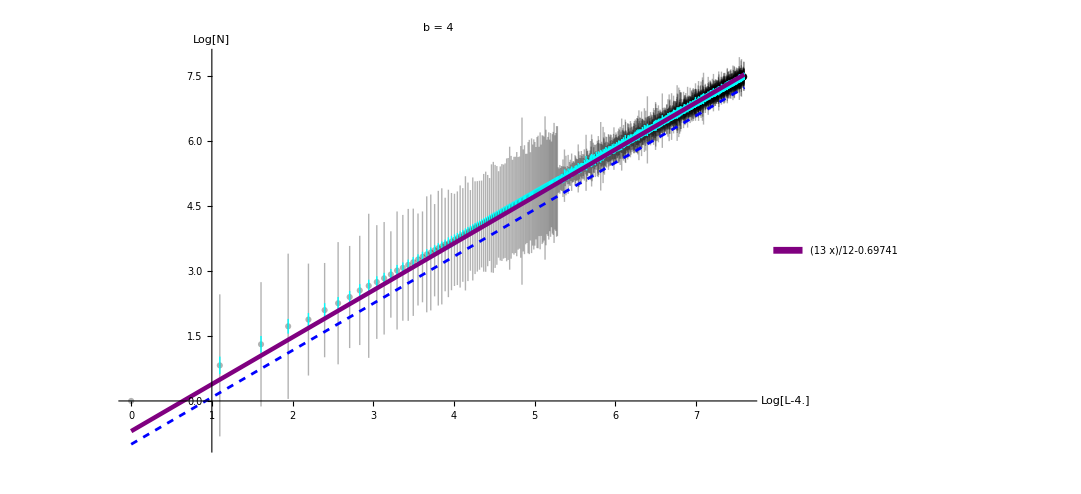

```mathematica
Show[{ListPlot[logAveragedWithMaxDevShifted,PlotStyle->{GrayLevel[0],Directive[Opacity[0.3]]},AxesLabel->{Row[{"Log[L-",(best[[1]]-51)/10//N,"]"}],"Log[N]"}]
,ListPlot[logAveragedWithErrorsShifted,PlotStyle->{RGBColor[0, 1, 1],PointSize->0.0003}]
(*,ListPlot[logAveragedWithEstimatedStdDevsShifted,PlotStyle->{RGBColor[1, 0.55, 1],Directive[Opacity[0.3]]}]*)

(*,Plot[lmp[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, Rational[2, 3], 0],Thickness->0.004}]*)

,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 0, 0.5],Thickness->0.004},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],{Right,Top}]]&@(lmAveragedShiftedSLE[x])

,Plot[x (dfSLE/.bb->b)-1,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, 0, 1],Dashed}]}
,(*PlotRange->All,*)PlotLabel->Row[{" b = ",b}]
(*,Epilog->{Directive[Dashed,GrayLevel[0.5]],
Line[{{Log[thresholdBelow],0},{Log[thresholdBelow],Log[maxy]//N}}]
,Line[{{Log[thresholdAbove],0},{Log[thresholdAbove],Log[maxy]//N}}]}*)
,PlotRange->{All,{0,All}},AxesOrigin->{1,0}]
```

### Average over big L closed to one another NO SHIFT -> Does not seem to help

```mathematica
logAveraged=Log[averaged];
logAveragedWithErrors=Log[averagedWithErrors]/. 0->Around[1.0*^-6,1.0*^-6];
logAveragedWithEstimatedStdDevs=Log[averagedWithEstimatedStdDevs]/. 0->Around[1.0*^-6,1.0*^-6];
logAveragedWithMaxDev=Log[averagedWithMaxDev]/. 0->Around[1.0*^-6,1.0*^-6];
```

Quick check on error propagation with Around

```mathematica
Log[864.51.]
Around[Log[864.],51./864.]
```

6.760.06

6.760.06

Continues

```mathematica
binSize=0.05;
logAveraged//N;

GroupBy[%,Floor[First[#],binSize]&];
binnedPoints=Values@%;
bigLlumpedTogether=Mean/@%;

Length[logAveraged]
Length[bigLlumpedTogether]
```

999

97

```mathematica
binSize=0.05;
logAveragedWithEstimatedStdDevs//N;

GroupBy[%,Floor[First[#],binSize]&];
binnedPoints=Values@%;
bigLlumpedTogetherEstimatedStdDevs=Mean/@%;

Length[logAveragedWithEstimatedStdDevs]
Length[bigLlumpedTogetherEstimatedStdDevs]
```

999

97

```mathematica
binSize=0.05;
logAveragedWithMaxDev//N;

GroupBy[%,Floor[First[#],binSize]&];
binnedPoints=Values@%;
bigLlumpedTogetherWithMaxDev=Mean/@%;

Length[logAveragedWithMaxDev]
Length[bigLlumpedTogetherWithMaxDev]
```

999

97

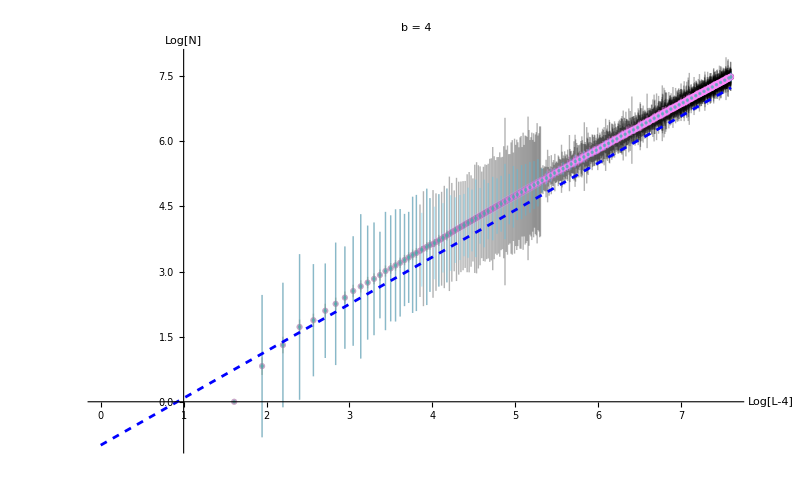

```mathematica
Show[{ListPlot[logAveragedWithMaxDev,PlotStyle->{GrayLevel[0],Directive[Opacity[0.3]]},AxesLabel->{"Log[L-4]","Log[N]"}]
(*,ListPlot[logAveragedWithErrorsShifted,PlotStyle->RGBColor[0, 1, 1]]*)
,ListPlot[logAveragedWithEstimatedStdDevs,PlotStyle->{RGBColor[1, 0.55, 1],Directive[Opacity[0.3]]}]
,ListPlot[bigLlumpedTogetherEstimatedStdDevs,PlotStyle->{RGBColor[0.17, 0.54, 0],Directive[Opacity[0.3]],PointSize->0.003}]
,ListPlot[bigLlumpedTogetherWithMaxDev,PlotStyle->{RGBColor[0.17, 0.8, 1],Directive[Opacity[0.3]],PointSize->0.003}]
(*,Plot[lmp[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, Rational[2, 3], 0],Thickness->0.004}]*)

(*,Plot[lmAveragedWithErrorsShifted[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 1, 0.5],Thickness->0.004}]*)

,Plot[x (dfSLE/.bb->b)-1,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, 0, 1],Dashed}]}
,(*PlotRange->All,*)PlotLabel->Row[{" b = ",b}]
(*,Epilog->{Directive[Dashed,GrayLevel[0.5]],
Line[{{Log[thresholdBelow],0},{Log[thresholdBelow],Log[maxy]//N}}]
,Line[{{Log[thresholdAbove],0},{Log[thresholdAbove],Log[maxy]//N}}]}*)
,PlotRange->{All,{0,All}},AxesOrigin->{1,0}]
```

```mathematica
fitFunc=a-df  Exp[-x]+df x;
par={a,(*c,ω,*)df};
lmAveragedLumpedTogether=NonlinearModelFit[Select[bigLlumpedTogether,#[[1]]>0&],{fitFunc(*,{-2<a<2,0<ω<28}*)},par,x];
lmAveragedWithErrorsLumpedTogether=NonlinearModelFit[Select[bigLlumpedTogetherEstimatedStdDevs,#[[1]]>0&],{fitFunc(*,{-2<a<2,0<ω<28}*)},par,x];
(*lmAveragedWithEstimatedStdDevsShifted=NonlinearModelFit[Select[logAveragedWithEstimatedStdDevsShifted,#[[1]]>0&],{fitFunc(*,{-2<a<2,0<ω<28}*)},{a,(*c,ω,*)df},x];*)
lmAveragedWithMaxDevLumpedTogether=NonlinearModelFit[Select[bigLlumpedTogetherWithMaxDev,#[[1]]>0&],{fitFunc(*,{-2<a<2,0<ω<28}*)},par,x];


Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@lmAveragedLumpedTogether
Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@lmAveragedWithErrorsLumpedTogether 
(*Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@lmAveragedWithEstimatedStdDevsShifted *)
Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@lmAveragedWithMaxDevLumpedTogether
```

lmAveragedLumpedTogether with a-df ⅇ^-x+df x: -0.811873-1.10419 ⅇ^-x+1.10419 x

lmAveragedWithErrorsLumpedTogether with a-df ⅇ^-x+df x: -1.73052-1.22781 ⅇ^-x+1.22781 x

lmAveragedWithMaxDevLumpedTogether with a-df ⅇ^-x+df x: -1.72754-1.22569 ⅇ^-x+1.22569 x

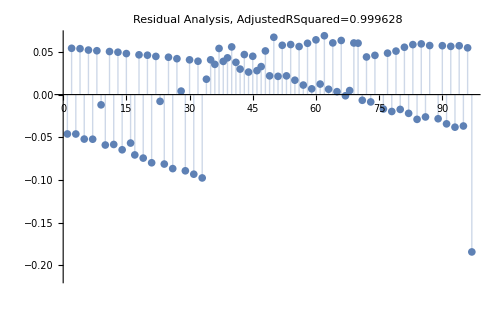
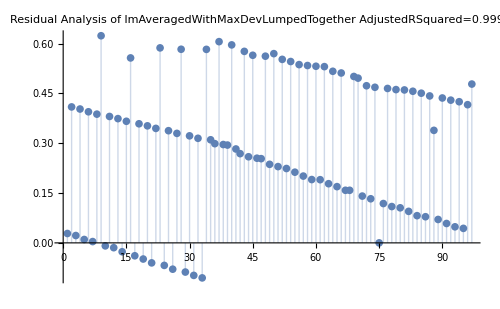
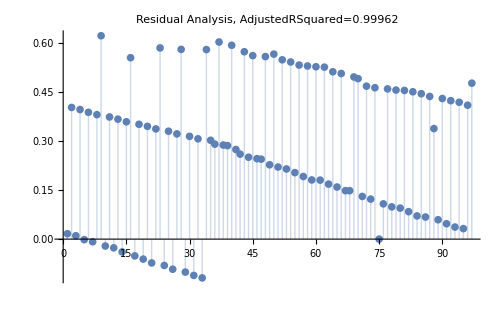
-Graphics- | -Graphics-
-Graphics- |

```mathematica
synchronizedPlots=Map[Show[#,ImageSize->500]&,{ListPlot[lmAveragedLumpedTogether["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis, AdjustedRSquared=",lmAveragedLumpedTogether["AdjustedRSquared"]}]]
,ListPlot[lmAveragedWithErrorsLumpedTogether["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis, AdjustedRSquared=",lmAveragedWithErrorsLumpedTogether["AdjustedRSquared"]}]]
(*,ListPlot[lmAveragedWithEstimatedStdDevsShifted["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis, AdjustedRSquared=",lmAveragedWithEstimatedStdDevsShifted["AdjustedRSquared"]}]]*)
,ListPlot[lmAveragedWithMaxDevLumpedTogether["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis of lmAveragedWithMaxDevLumpedTogether\nAdjustedRSquared=",lmAveragedWithMaxDevLumpedTogether["AdjustedRSquared"]}]]}];

Multicolumn[synchronizedPlots,2,Appearance->"Framed"]
```

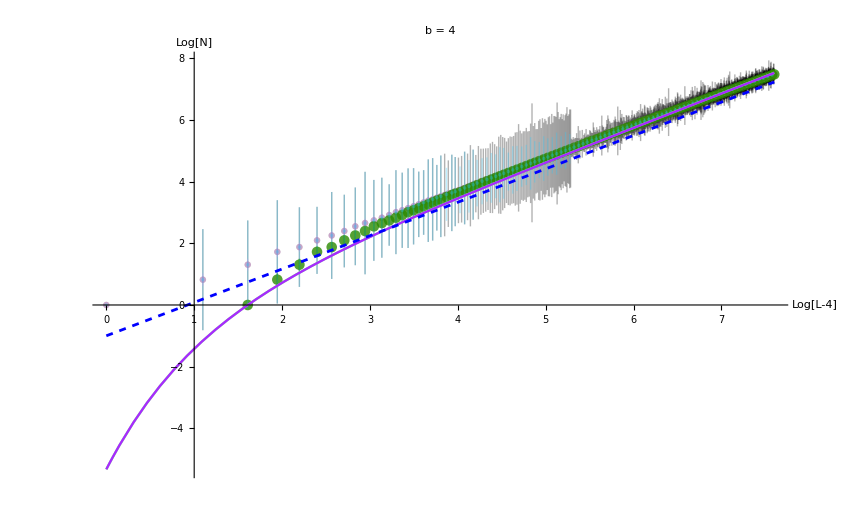

```mathematica
Show[{ListPlot[logAveragedWithMaxDevShifted,PlotStyle->{GrayLevel[0],Directive[Opacity[0.3]]},AxesLabel->{"Log[L-4]","Log[N]"}]
(*,ListPlot[logAveragedWithErrorsShifted,PlotStyle->RGBColor[0, 1, 1]]*)
,ListPlot[logAveragedWithEstimatedStdDevsShifted,PlotStyle->{RGBColor[1, 0.55, 1],Directive[Opacity[0.3]]}]
,ListPlot[bigLlumpedTogetherEstimatedStdDevs,PlotStyle->{RGBColor[0.17, 0.54, 0],Directive[Opacity[0.8]],PointSize->0.009}]
,ListPlot[bigLlumpedTogetherWithMaxDevShifted,PlotStyle->{RGBColor[0.17, 0.8, 1],Directive[Opacity[0.3]],PointSize->0.003}]

(*,Plot[lmp[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, Rational[2, 3], 0],Thickness->0.004}]*)

,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 1, 0.5],Thickness->0.002},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],{Right,Top}]]&@(lmAveragedWithErrorsLumpedTogether[x])
,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.66, 0.16, 1],Thickness->0.002},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],{Right,Top}]]&@(lmAveragedWithMaxDevLumpedTogether[x])

,Plot[x (dfSLE/.bb->b)-1,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, 0, 1],Dashed}]}
,(*PlotRange->All,*)PlotLabel->Row[{" b = ",b}]
(*,Epilog->{Directive[Dashed,GrayLevel[0.5]],
Line[{{Log[thresholdBelow],0},{Log[thresholdBelow],Log[maxy]//N}}]
,Line[{{Log[thresholdAbove],0},{Log[thresholdAbove],Log[maxy]//N}}]}*)
,PlotRange->{All,{0,All}},AxesOrigin->{1,0}]
```

### Average over big L closed to one another AFTER SHIFT -> Does not seem to help

```mathematica
shift:=Plus[{-4,0},#]&;

logAveragedShifted=Log[shift/@averaged];
logAveragedWithErrorsShifted=Log[shift/@averagedWithErrors]/. {a_,0}->{a,Around[1.0*^-6,1.0*^-6]};
logAveragedWithEstimatedStdDevsShifted=Log[shift/@averagedWithEstimatedStdDevs]/. {a_,0}->{a,Around[1.0*^-6,1.0*^-6]};
logAveragedWithMaxDevShifted=Log[shift/@averagedWithMaxDev]/.{a_,0}->{a,Around[1.0*^-6,1.0*^-6]};
```

```mathematica
binSize=0.05;
logAveragedShifted//N;

GroupBy[%,Floor[First[#],binSize]&];
binnedPoints=Values@%;
bigLlumpedTogether=Mean/@%;

Length[logAveragedShifted]
Length[bigLlumpedTogether]
```

999

98

```mathematica
binSize=0.05;
logAveragedWithEstimatedStdDevsShifted//N;

GroupBy[%,Floor[First[#],binSize]&];
binnedPoints=Values@%;
bigLlumpedTogetherEstimatedStdDevs=Mean/@%;

Length[logAveragedWithEstimatedStdDevsShifted]
Length[bigLlumpedTogetherEstimatedStdDevs]
```

999

98

```mathematica
binSize=0.05;
logAveragedWithMaxDevShifted//N;

GroupBy[%,Floor[First[#],binSize]&];
binnedPoints=Values@%;
bigLlumpedTogetherWithMaxDevShifted=Mean/@%;

Length[logAveragedWithMaxDevShifted]
Length[bigLlumpedTogetherWithMaxDevShifted]
```

999

98

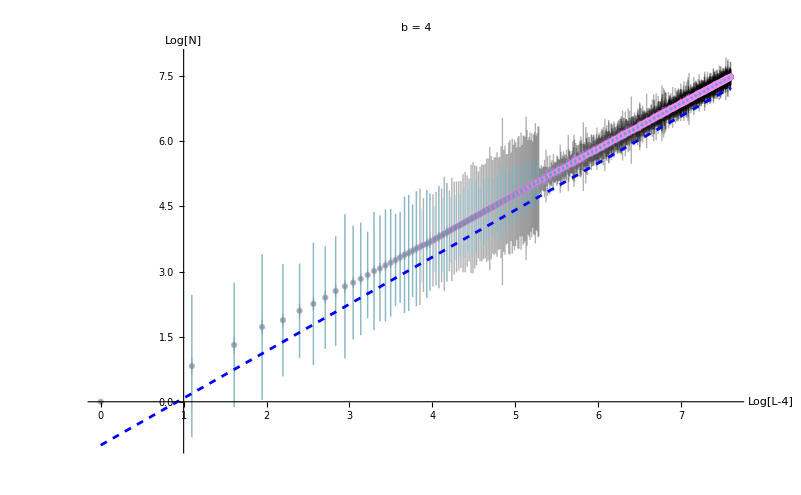

```mathematica
Show[{ListPlot[logAveragedWithMaxDevShifted,PlotStyle->{GrayLevel[0],Directive[Opacity[0.3]]},AxesLabel->{"Log[L-4]","Log[N]"}]
(*,ListPlot[logAveragedWithErrorsShifted,PlotStyle->RGBColor[0, 1, 1]]*)
,ListPlot[logAveragedWithEstimatedStdDevsShifted,PlotStyle->{RGBColor[1, 0.55, 1],Directive[Opacity[0.3]]}]
,ListPlot[bigLlumpedTogetherEstimatedStdDevs,PlotStyle->{RGBColor[0.17, 0.54, 0],Directive[Opacity[0.3]],PointSize->0.003}]
,ListPlot[bigLlumpedTogetherWithMaxDevShifted,PlotStyle->{RGBColor[0.17, 0.8, 1],Directive[Opacity[0.3]],PointSize->0.003}]
(*,Plot[lmp[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, Rational[2, 3], 0],Thickness->0.004}]*)

(*,Plot[lmAveragedWithErrorsShifted[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 1, 0.5],Thickness->0.004}]*)

,Plot[x (dfSLE/.bb->b)-1,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, 0, 1],Dashed}]}
,(*PlotRange->All,*)PlotLabel->Row[{" b = ",b}]
(*,Epilog->{Directive[Dashed,GrayLevel[0.5]],
Line[{{Log[thresholdBelow],0},{Log[thresholdBelow],Log[maxy]//N}}]
,Line[{{Log[thresholdAbove],0},{Log[thresholdAbove],Log[maxy]//N}}]}*)
,PlotRange->{All,{0,All}},AxesOrigin->{1,0}]
```

```mathematica
fitFunc=a+df x;
lmAveragedLumpedTogether=NonlinearModelFit[Select[bigLlumpedTogether,#[[1]]>0&],{fitFunc(*,{-2<a<2,0<ω<28}*)},{a,(*c,ω,*)df},x];
lmAveragedWithErrorsLumpedTogether=NonlinearModelFit[Select[bigLlumpedTogetherEstimatedStdDevs,#[[1]]>0&],{fitFunc(*,{-2<a<2,0<ω<28}*)},{a,(*c,ω,*)df},x];
(*lmAveragedWithEstimatedStdDevsShifted=NonlinearModelFit[Select[logAveragedWithEstimatedStdDevsShifted,#[[1]]>0&],{fitFunc(*,{-2<a<2,0<ω<28}*)},{a,(*c,ω,*)df},x];*)
lmAveragedWithMaxDevLumpedTogether=NonlinearModelFit[Select[bigLlumpedTogetherWithMaxDevShifted,#[[1]]>0&],{fitFunc(*,{-2<a<2,0<ω<28}*)},{a,(*c,ω,*)df},x];


Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@lmAveragedLumpedTogether
Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@lmAveragedWithErrorsLumpedTogether 
(*Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@lmAveragedWithEstimatedStdDevsShifted *)
Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@lmAveragedWithMaxDevLumpedTogether
```

lmAveragedLumpedTogether with a+df x: -0.413539+1.03959 x

lmAveragedWithErrorsLumpedTogether with a+df x: -0.410667+1.03978 x

lmAveragedWithMaxDevLumpedTogether with a+df x: -0.37998+1.03547 x

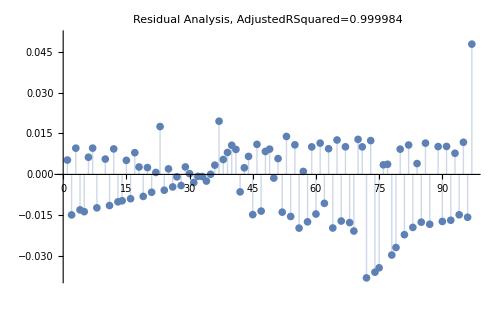
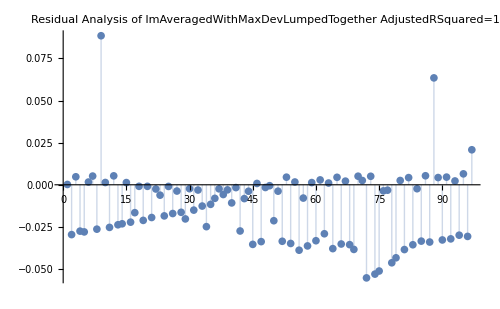
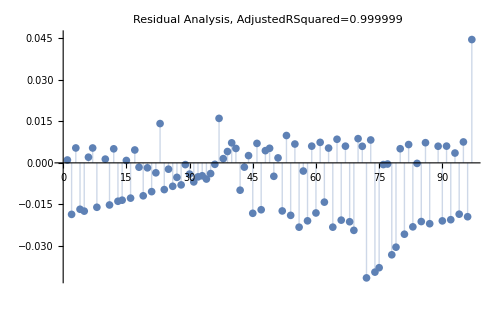
-Graphics- | -Graphics-
-Graphics- |

```mathematica
synchronizedPlots=Map[Show[#,ImageSize->500]&,{ListPlot[lmAveragedLumpedTogether["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis, AdjustedRSquared=",lmAveragedLumpedTogether["AdjustedRSquared"]}]]
,ListPlot[lmAveragedWithErrorsLumpedTogether["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis, AdjustedRSquared=",lmAveragedWithErrorsLumpedTogether["AdjustedRSquared"]}]]
(*,ListPlot[lmAveragedWithEstimatedStdDevsShifted["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis, AdjustedRSquared=",lmAveragedWithEstimatedStdDevsShifted["AdjustedRSquared"]}]]*)
,ListPlot[lmAveragedWithMaxDevLumpedTogether["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis of lmAveragedWithMaxDevLumpedTogether\nAdjustedRSquared=",lmAveragedWithMaxDevLumpedTogether["AdjustedRSquared"]}]]}];

Multicolumn[synchronizedPlots,2,Appearance->"Framed"]
```

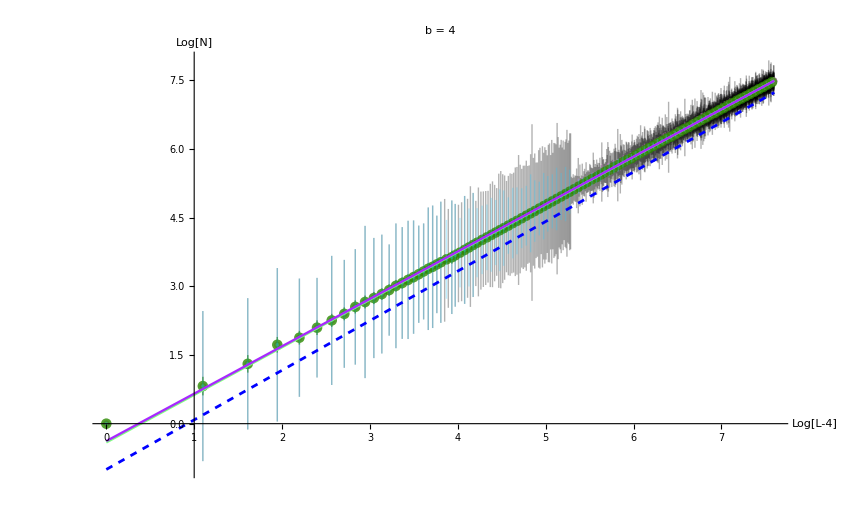

```mathematica
Show[{ListPlot[logAveragedWithMaxDevShifted,PlotStyle->{GrayLevel[0],Directive[Opacity[0.3]]},AxesLabel->{"Log[L-4]","Log[N]"}]
(*,ListPlot[logAveragedWithErrorsShifted,PlotStyle->RGBColor[0, 1, 1]]*)
,ListPlot[logAveragedWithEstimatedStdDevsShifted,PlotStyle->{RGBColor[1, 0.55, 1],Directive[Opacity[0.3]]}]
,ListPlot[bigLlumpedTogetherEstimatedStdDevs,PlotStyle->{RGBColor[0.17, 0.54, 0],Directive[Opacity[0.8]],PointSize->0.009}]
,ListPlot[bigLlumpedTogetherWithMaxDevShifted,PlotStyle->{RGBColor[0.17, 0.8, 1],Directive[Opacity[0.3]],PointSize->0.003}]

(*,Plot[lmp[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, Rational[2, 3], 0],Thickness->0.004}]*)

,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 1, 0.5],Thickness->0.002},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],{Right,Top}]]&@(lmAveragedWithErrorsLumpedTogether[x])
,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.66, 0.16, 1],Thickness->0.002},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],{Right,Top}]]&@(lmAveragedWithMaxDevLumpedTogether[x])

,Plot[x (dfSLE/.bb->b)-1,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, 0, 1],Dashed}]}
,(*PlotRange->All,*)PlotLabel->Row[{" b = ",b}]
(*,Epilog->{Directive[Dashed,GrayLevel[0.5]],
Line[{{Log[thresholdBelow],0},{Log[thresholdBelow],Log[maxy]//N}}]
,Line[{{Log[thresholdAbove],0},{Log[thresholdAbove],Log[maxy]//N}}]}*)
,PlotRange->{All,{0,All}},AxesOrigin->{1,0}]
```

### Looking for the best fitting strategy

#### FindFit VS NonlinearModelFit: FindFit just returns the solution while NonlinearModelFit returns all the fit statistics

```mathematica
fitFunc=a+c Exp[-ω x]+df x;
FindFit[logAveraged,{fitFunc(*,{-2<a<2,0<ω<28}*)},{a,c,ω,df},x]
NonlinearModelFit[logAveraged,{fitFunc(*,{-2<a<2,0<ω<28}*)},{a,c,ω,df},x];
%//Normal
```

{a→-0.434885,c→-7.6569,ω→1.16632,df→1.04311}

-0.434885-7.6569 ⅇ^(-1.16632 x)+1.04311 x

#### With and without Method -> “NMinimize” (which looks for the global minimum, I think it’s always better)

No errors

```mathematica
fitFunc=a+c Exp[-ω x]+df x;
fitFunc=a-c Exp[- x]+df x;
nlmAveraged=NonlinearModelFit[logAveraged,{fitFunc(*,{-2<a<2,0<ω<28}*)},{a,c,(*c,ω,*)df},x];
nlmAveragedGlobal=NonlinearModelFit[logAveraged,{fitFunc(*,{-2<a<2,0<ω<28}*)},{a,c,(*c,ω,*)df},x,Method->"NMinimize"];

Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@nlmAveraged
Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@nlmAveragedGlobal
```

NonlinearModelFit::lmnl: The model a-c ⅇ^-x+df x is linear in the parameters {a,c,df}, but a nonlinear method or non-Euclidean norm was specified, so nonlinear methods will be used.

nlmAveraged with a-c ⅇ^-x+df x: -0.380805-5.73961 ⅇ^-x+1.03585 x

nlmAveragedGlobal with a-c ⅇ^-x+df x: -0.380801-5.73964 ⅇ^-x+1.03585 x

0.999961

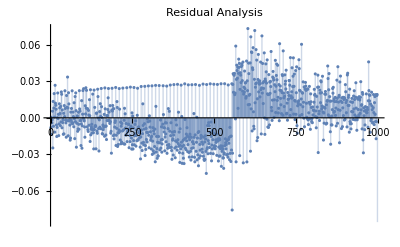

0.999961

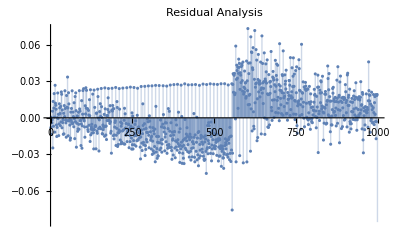

```mathematica
(*Extract and plot residuals*)

nlmAveraged["AdjustedRSquared"]
ListPlot[nlmAveraged["FitResiduals"],Filling->Axis,PlotLabel->"Residual Analysis"]

nlmAveragedGlobal["AdjustedRSquared"]
ListPlot[nlmAveragedGlobal["FitResiduals"],Filling->Axis,PlotLabel->"Residual Analysis"]
```

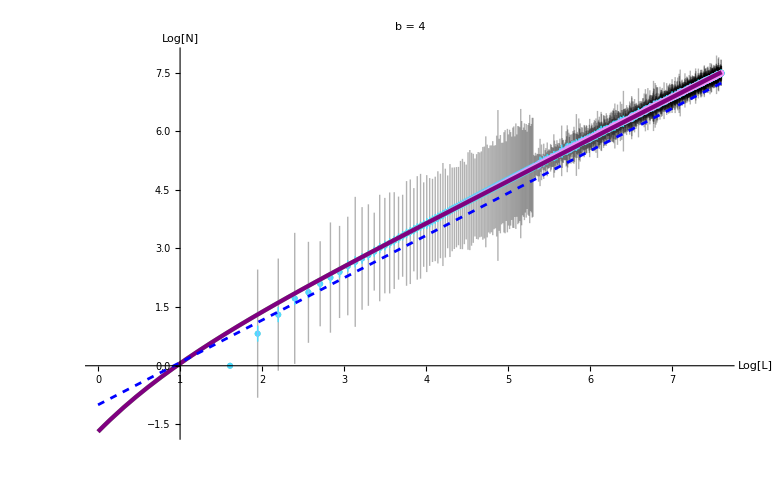

RGBColor[0.5, 1, 0.5] Averaged data fit without errors and a-df ⅇ^-x+df x: d_f=1.0690.004
RGBColor[0.5, 0, 0.5] Averaged data fit without errors, global minimum and a-df ⅇ^-x+df x: d_f=1.0690.004

RGBColor[0, 0, 1] Result from the litterature (exact with SLE): 13/12 = 1.08333

```mathematica
maxx=Max[rawData[[All,1]]];
maxy=Max[rawData[[All,2]]];

thresholdBelow=0;
thresholdAbove=maxx-0;

Show[{ListPlot[logAveragedWithMaxDev,PlotStyle->{GrayLevel[0],Directive[Opacity[0.3]]},AxesLabel->{"Log[L]","Log[N]"}]
,ListPlot[logAveragedWithErrors,PlotStyle->RGBColor[0, 1, 1]]
,ListPlot[logAveragedWithEstimatedStdDevs,PlotStyle->{RGBColor[1, 0.55, 1],Directive[Opacity[0.3]]}]

(*,Plot[lmp[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, Rational[2, 3], 0],Thickness->0.004}]*)

,Plot[nlmAveraged[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 1, 0.5],Thickness->0.004}]
,Plot[nlmAveragedGlobal[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 0, 0.5],Thickness->0.004}]

,Plot[x (dfSLE/.bb->b)-1,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, 0, 1],Dashed}]}
,(*PlotRange->All,*)PlotLabel->Row[{" b = ",b}]
(*,Epilog->{Directive[Dashed,GrayLevel[0.5]],
Line[{{Log[thresholdBelow],0},{Log[thresholdBelow],Log[maxy]//N}}]
,Line[{{Log[thresholdAbove],0},{Log[thresholdAbove],Log[maxy]//N}}]}*)
,PlotRange->{{1,All},{0,All}},AxesOrigin->{1,0}]


Print[ (*"Full data - Linear fit : d_f=",Around[Quiet@lm["ParameterTable"][[1]][[1,3,2]],π*lm["ParameterErrors"][[2]]],*)"
RGBColor[0.5, 1, 0.5] Averaged data fit without errors and " ,fitFunc,": d_f=",Around[Quiet@nlmAveraged["ParameterTable"][[1,1,-1,2]],π*Quiet@nlmAveraged["ParameterTable"][[1,1,-1,3]]],"
RGBColor[0.5, 0, 0.5] Averaged data fit without errors, global minimum and " ,fitFunc,": d_f=",Around[Quiet@nlmAveragedGlobal["ParameterTable"][[1,1,-1,2]],π*Quiet@nlmAveragedGlobal["ParameterTable"][[1,1,-1,3]]],"

RGBColor[0, 0, 1] Result from the litterature (exact with SLE): ",(dfSLE/.bb->b)," = ",(dfSLE/.bb->b/1.)]
```

```mathematica
Series[Log[1+x],{x,0,2}]
```

x-x^2/2+O[x]^3

```mathematica
Quiet@nlmAveragedGlobal["ParameterTable"][[1,1,-1,3]]
```

0.000938213

Errors obtained with StandardDeviation[]

```mathematica
fitFunc=a+c Exp[-ω x]+df x;
fitFunc=a+c Exp[- x]+df x;

nlmAveragedWithStdDevs=NonlinearModelFit[logAveragedWithErrors,{fitFunc,{(*-2<a<2,*)a<0(*,0.5<ω<=3*),c<0(*,1<df<1.1*)}},{a,c,ω(*{a,-0.5},{c,-30.},{ω,2.}*),df(*,{df,1.083}*)},x,MaxIterations->10000];
nlmAveragedWithStdDevsUnconstrained=NonlinearModelFit[logAveragedWithErrors,{fitFunc,{(*-2<a<2,*)(*,0.5<ω<=3*)(*,1<df<1.1*)}},{a,c,ω(*{a,-0.5},{c,-30.},{ω,2.}*),df(*,{df,1.083}*)},x,MaxIterations->10000];

Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@nlmAveragedWithStdDevs
Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@nlmAveragedWithStdDevsUnconstrained

nlmAveragedWithStdDevsGlobal=NonlinearModelFit[logAveragedWithErrors,{fitFunc,{(*-2<a<2,*)a<0(*,0.5<ω<=3*),c<0(*,1<df<1.1*)}},{a,c,ω(*{a,-0.5},{c,-30.},{ω,2.}*),df(*,{df,1.083}*)},x,MaxIterations->1000,Method->"NMinimize"];
nlmAveragedWithStdDevsUnconstrainedGlobal=NonlinearModelFit[logAveragedWithErrors,fitFunc,{a,c,ω(*{a,-0.5},{c,-30.},{ω,2.}*),df(*,{df,1.083}*)},x,MaxIterations->1000,Method->"NMinimize"];

Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@nlmAveragedWithStdDevsGlobal
Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@nlmAveragedWithStdDevsUnconstrainedGlobal
```

nlmAveragedWithStdDevs with a+c ⅇ^-x+df x: -0.337126-6.59842 ⅇ^-x+1.02944 x

nlmAveragedWithStdDevsUnconstrained with a+c ⅇ^-x+df x: -0.360392-6.50861 ⅇ^-x+1.03273 x

NonlinearModelFit::lmnl: The model a+c ⅇ^-x+df x is linear in the parameters {a,c,ω,df}, but a nonlinear method or non-Euclidean norm was specified, so nonlinear methods will be used.

nlmAveragedWithStdDevsGlobal with a+c ⅇ^-x+df x: -0.36041-6.50853 ⅇ^-x+1.03273 x

nlmAveragedWithStdDevsUnconstrainedGlobal with a+c ⅇ^-x+df x: -0.36104-6.50615 ⅇ^-x+1.03283 x

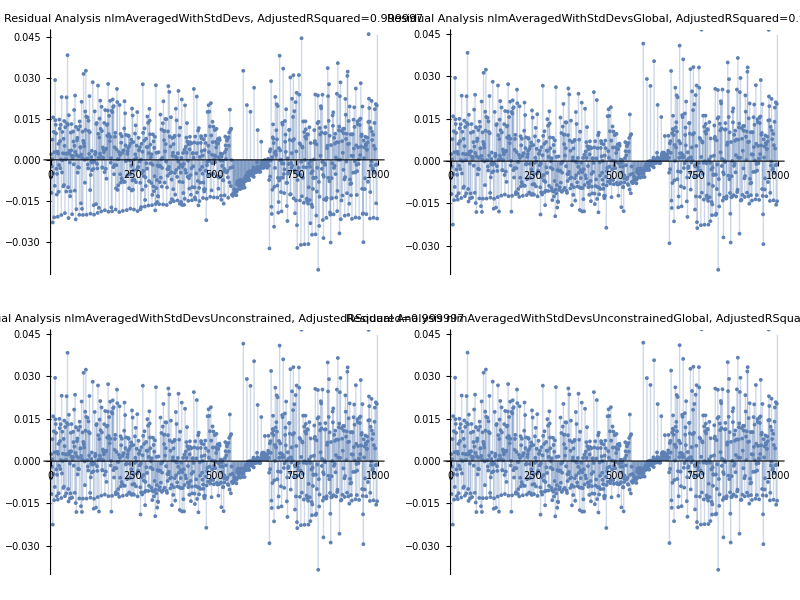

```mathematica
synchronizedPlots=Map[Show[#,ImageSize->500]&,{ListPlot[nlmAveragedWithStdDevs["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis nlmAveragedWithStdDevs,\nAdjustedRSquared=",nlmAveragedWithStdDevs["AdjustedRSquared"]}]]
,ListPlot[nlmAveragedWithStdDevsUnconstrained["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis nlmAveragedWithStdDevsUnconstrained,\nAdjustedRSquared=",nlmAveragedWithStdDevsUnconstrained["AdjustedRSquared"]}]]
,ListPlot[nlmAveragedWithStdDevsGlobal["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis nlmAveragedWithStdDevsGlobal,\nAdjustedRSquared=",nlmAveragedWithStdDevsGlobal["AdjustedRSquared"]}]]
,ListPlot[nlmAveragedWithStdDevsUnconstrainedGlobal["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis nlmAveragedWithStdDevsUnconstrainedGlobal,\nAdjustedRSquared=",nlmAveragedWithStdDevsUnconstrainedGlobal["AdjustedRSquared"]}]]}];

Multicolumn[synchronizedPlots,2,Appearance->"Framed"]
```

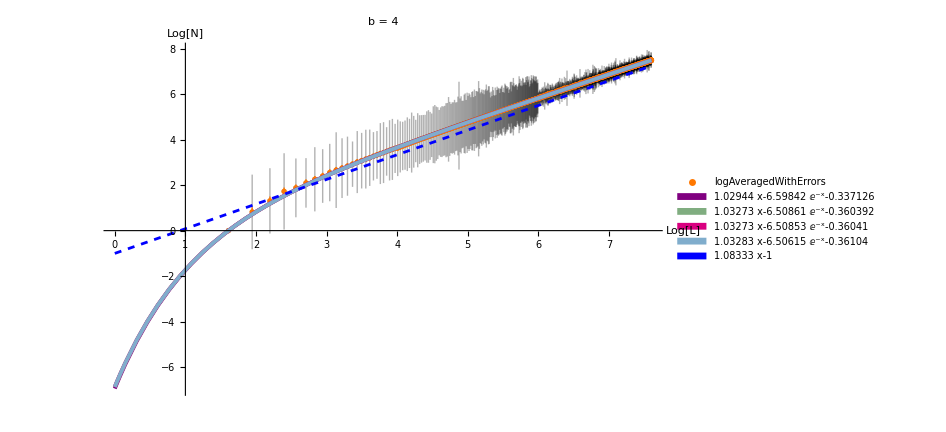

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1031.24] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2583.28] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4009.26] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

Averaged data fit with errors and a+c ⅇ^-x+df x RGBColor[0.5, 0, 0.5]: d_f=1.02940.0018, Parameters: | Estimate | Standard Error | t-Statistic | P-Value
a | -0.337126 | 0.00407167 | -82.7981 | 0.
c | -6.59842 | 0.0156968 | -420.368 | 0.
ω | 0. | 0. | ComplexInfinity | 0.
df | 1.02944 | 0.000582656 | 1766.8 | 0.
Averaged data fit with errors and a+c ⅇ^-x+df x (unconstrained) RGBColor[0.5, 0.68, 0.5]: d_f=1.03270.0018, Parameters: | Estimate | Standard Error | t-Statistic | P-Value
a | -0.360392 | 0.00399675 | -90.1711 | 0.
c | -6.50861 | 0.015408 | -422.418 | 0.
ω | 0. | 0. | ComplexInfinity | 0.
df | 1.03273 | 0.000571936 | 1805.68 | 0.

Result from the litterature (exact with SLE) RGBColor[0, 0, 1]: 13/12 = 1.08333

```mathematica
maxx=Max[rawData[[All,1]]];
maxy=Max[rawData[[All,2]]];

thresholdBelow=0;
thresholdAbove=maxx-0;

Show[{ListPlot[logAveragedWithMaxDev,PlotStyle->{GrayLevel[0],Directive[Opacity[0.3]]},AxesLabel->{"Log[L]","Log[N]"}]
,ListPlot[logAveragedWithErrors,PlotStyle->RGBColor[1, 0.47000000000000003, 0],PlotLegends->{"logAveragedWithErrors"}]
,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 0, 0.5],Thickness->0.004},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],Right]]&@nlmAveragedWithStdDevs[x]
,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 0.68, 0.5],Thickness->0.004},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],Right]]&@nlmAveragedWithStdDevsUnconstrained[x]
,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.85, 0, 0.5],Thickness->0.004},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],Right]]&@nlmAveragedWithStdDevsGlobal[x]
,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 0.68, 0.8],Thickness->0.004},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],Right]]&@nlmAveragedWithStdDevsUnconstrainedGlobal[x]

,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, 0, 1],Dashed},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],Right]]&@(x (dfSLE/.bb->N[b])-1)
}
,PlotLabel->Row[{" b = ",b}]
,PlotRange->{All,{0,All}},AxesOrigin->{1,0},ImageSize->700]

Print[ "Averaged data fit with errors and " ,fitFunc," RGBColor[0.5, 0, 0.5]: d_f=",Around[Quiet@nlmAveragedWithStdDevs["ParameterTable"][[1]][[1,-1,2]],π*nlmAveragedWithStdDevs["ParameterTable"][[1]][[1,-1,3]]],", Parameters:",Quiet@nlmAveragedWithStdDevs["ParameterTable"],"
Averaged data fit with errors and " ,fitFunc," (unconstrained) RGBColor[0.5, 0.68, 0.5]: d_f=",Around[Quiet@nlmAveragedWithStdDevsUnconstrained["ParameterTable"][[1]][[1,-1,2]],π*nlmAveragedWithStdDevsUnconstrained["ParameterTable"][[1]][[1,-1,3]]],", Parameters:",Quiet@nlmAveragedWithStdDevsUnconstrained["ParameterTable"],"

Result from the litterature (exact with SLE) RGBColor[0, 0, 1]: ",(dfSLE/.bb->b)," = ",(dfSLE/.bb->b/1.)]
```

Errors obtained with StdDevEstimate[]

```mathematica
fitFunc=a+c Exp[-ω x]+df x;
(*fitFunc=a+c Exp[- x]+df x;*)

nlmAveragedWithEstimatedStdDevs=NonlinearModelFit[logAveragedWithEstimatedStdDevs,{fitFunc,{(*-2<a<2,*)a<0,0.5<ω<=3,c<0(*,1<df<1.1*)}},{a,c,ω(*{a,-0.5},{c,-30.},{ω,2.}*),df(*,{df,1.083}*)},x,MaxIterations->1000];
nlmAveragedWithEstimatedStdDevsUnconstrained=NonlinearModelFit[logAveragedWithEstimatedStdDevs,{fitFunc,{(*-2<a<2,*)0.5<ω<=30(*,1<df<1.1*)}},{a,c,ω(*{a,-0.5},{c,-30.},{ω,2.}*),df(*,{df,1.083}*)},x,MaxIterations->1000];

Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@nlmAveragedWithEstimatedStdDevs
Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@nlmAveragedWithEstimatedStdDevsUnconstrained

nlmAveragedWithEstimatedStdDevsGlobal=NonlinearModelFit[logAveragedWithEstimatedStdDevs,{fitFunc,{(*-2<a<2,*)a<0,0.5<ω<=30,c<0(*,1<df<1.1*)}},{a,c,ω(*{a,-0.5},{c,-30.},{ω,2.}*),df(*,{df,1.083}*)},x,MaxIterations->1000,Method->"NMinimize"];
nlmAveragedWithEstimatedStdDevsUnconstrainedGlobal=NonlinearModelFit[logAveragedWithEstimatedStdDevs,{fitFunc,ω<=3},{a,c,ω(*{a,-0.5},{c,-30.},{ω,2.}*),df(*,{df,1.083}*)},x,MaxIterations->1000,Method->"NMinimize"];

Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@nlmAveragedWithEstimatedStdDevsGlobal
Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@nlmAveragedWithEstimatedStdDevsUnconstrainedGlobal
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

NonlinearModelFit::steperr: Error in step computation.

nlmAveragedWithEstimatedStdDevs with a+c ⅇ^(-x ω)+df x: -0.0978109-175.502 ⅇ^(-2.9337 x)+1.03138 x

nlmAveragedWithEstimatedStdDevsUnconstrained with a+c ⅇ^(-x ω)+df x: 1.75878×10^19-6.03488×10^15 ⅇ^(-11.2502 x)-1.09279×10^19 x

nlmAveragedWithEstimatedStdDevsGlobal with a+c ⅇ^(-x ω)+df x: -2.04496-2.53962 ⅇ^(-16.1212 x)+1.27061 x

nlmAveragedWithEstimatedStdDevsUnconstrainedGlobal with a+c ⅇ^(-x ω)+df x: -2.00225-3.55918 ⅇ^(-3. x)+1.26176 x

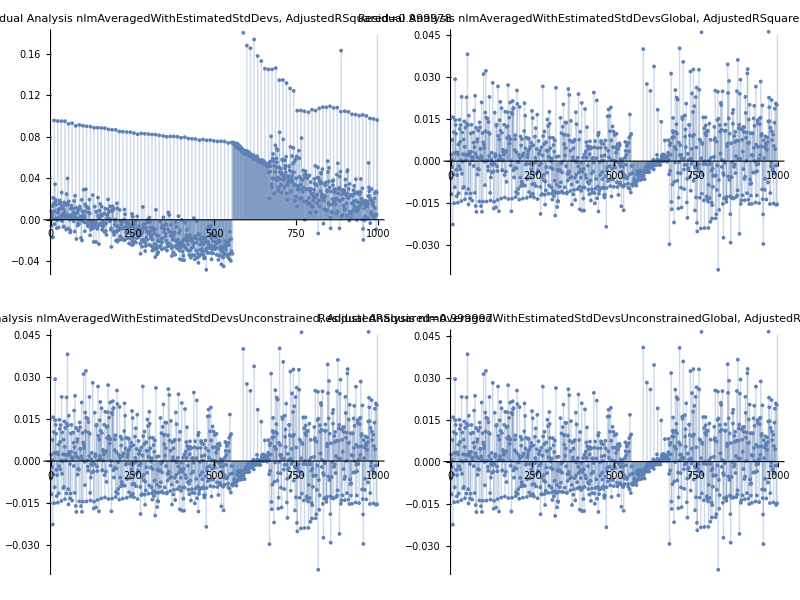

```mathematica
synchronizedPlots=Map[Show[#,ImageSize->500]&,{ListPlot[nlmAveragedWithEstimatedStdDevs["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis nlmAveragedWithEstimatedStdDevs,\nAdjustedRSquared=",nlmAveragedWithEstimatedStdDevs ["AdjustedRSquared"]}]]
,ListPlot[nlmAveragedWithEstimatedStdDevsUnconstrained["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis nlmAveragedWithEstimatedStdDevsUnconstrained,\nAdjustedRSquared=",nlmAveragedWithEstimatedStdDevsUnconstrained["AdjustedRSquared"]}]]
,ListPlot[nlmAveragedWithEstimatedStdDevsGlobal["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis nlmAveragedWithEstimatedStdDevsGlobal,\nAdjustedRSquared=",nlmAveragedWithEstimatedStdDevsGlobal["AdjustedRSquared"]}]]
,ListPlot[nlmAveragedWithEstimatedStdDevsUnconstrainedGlobal["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis nlmAveragedWithEstimatedStdDevsUnconstrainedGlobal,\nAdjustedRSquared=",nlmAveragedWithEstimatedStdDevsUnconstrainedGlobal["AdjustedRSquared"]}]]}];

Multicolumn[synchronizedPlots,2,Appearance->"Framed"]
```

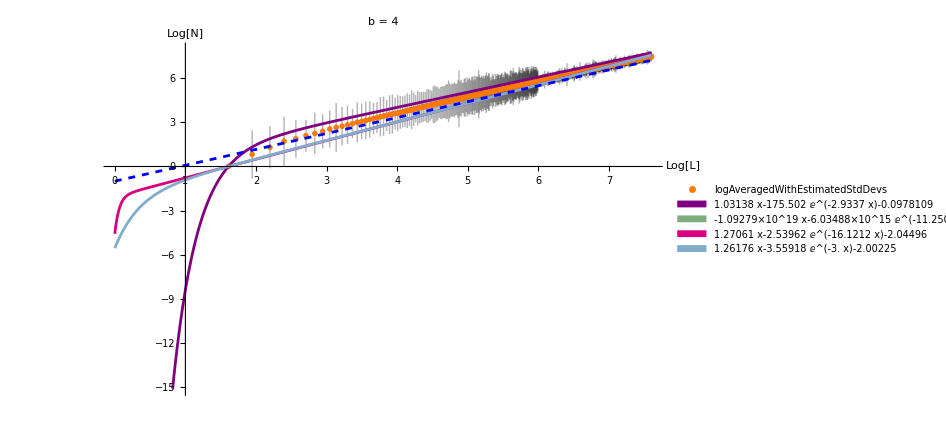

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-954.617] is too small to represent as a normalized machine number; precision may be lost.

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-2698.41] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-28738.3] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Averaged data fit with errors and a+c ⅇ^(-x ω)+df x RGBColor[0.5, 0, 0.5]: d_f=1.030.04, Parameters: | Estimate | Standard Error | t-Statistic | P-Value
a | -0.0978109 | 0.0954897 | -1.02431 | 0.305938
c | -175.502 | 727.409 | -0.24127 | 0.809396
ω | 2.9337 | 2.58251 | 1.13599 | 0.256236
df | 1.03138 | 0.0136191 | 75.7302 | 0.
Averaged data fit with errors and a+c ⅇ^(-x ω)+df x (unconstrained) RGBColor[0.5, 0.68, 0.5]: d_f=-1.090.0810^19, Parameters: | Estimate | Standard Error | t-Statistic | P-Value
a | 1.75878×10^19 | 3.72459×10^16 | 472.208 | 0.
c | -6.03488×10^15 | 54.9224 | -1.0988×10^14 | 0.
ω | 11.2502 | 3.45104×10^9 | 3.25995×10^-9 | 1
df | -1.09279×10^19 | 2.61985×10^17 | -41.712 | 1.09681×10^-220

Result from the litterature (exact with SLE) RGBColor[0, 0, 1]: 13/12 = 1.08333

```mathematica
maxx=Max[rawData[[All,1]]];
maxy=Max[rawData[[All,2]]];

thresholdBelow=0;
thresholdAbove=maxx-0;

Show[{ListPlot[logAveragedWithMaxDev,PlotStyle->{GrayLevel[0],Directive[Opacity[0.3]]},AxesLabel->{"Log[L]","Log[N]"}]
,ListPlot[logAveragedWithEstimatedStdDevs,PlotStyle->RGBColor[1, 0.47000000000000003, 0],PlotLegends->{"logAveragedWithEstimatedStdDevs"}]
,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 0, 0.5],Thickness->0.004},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],Right]]&@nlmAveragedWithEstimatedStdDevs[x]
,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 0.68, 0.5],Thickness->0.004},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],Right]]&@nlmAveragedWithEstimatedStdDevsUnconstrained[x]
,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.85, 0, 0.5],Thickness->0.004},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],Right]]&@nlmAveragedWithEstimatedStdDevsGlobal[x]
,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 0.68, 0.8],Thickness->0.004},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],Right]]&@nlmAveragedWithEstimatedStdDevsUnconstrainedGlobal[x]

,Plot[x (dfSLE/.bb->b)-1,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, 0, 1],Dashed}]
}
,PlotLabel->Row[{" b = ",b}]
,PlotRange->{All,{0,All}},AxesOrigin->{1,0},ImageSize->700]

Print[ "Averaged data fit with errors and " ,fitFunc," RGBColor[0.5, 0, 0.5]: d_f=",Around[Quiet@nlmAveragedWithEstimatedStdDevs["ParameterTable"][[1]][[1,-1,2]],π*nlmAveragedWithEstimatedStdDevs["ParameterTable"][[1]][[1,-1,3]]],", Parameters:",Quiet@nlmAveragedWithEstimatedStdDevs["ParameterTable"],"
Averaged data fit with errors and " ,fitFunc," (unconstrained) RGBColor[0.5, 0.68, 0.5]: d_f=",Around[Quiet@nlmAveragedWithEstimatedStdDevsUnconstrained["ParameterTable"][[1]][[1,-1,2]],π*nlmAveragedWithEstimatedStdDevsUnconstrained["ParameterTable"][[1]][[1,-1,3]]],", Parameters:",Quiet@nlmAveragedWithEstimatedStdDevsUnconstrained["ParameterTable"],"

Result from the litterature (exact with SLE) RGBColor[0, 0, 1]: ",(dfSLE/.bb->b)," = ",(dfSLE/.bb->b/1.)]
```

Errors obtained with MaxDev[]

```mathematica
fitFunc=a+c Exp[-ω x]+df x;
fitFunc=a+c Exp[- x]+df x;

nlmAveragedWithMaxStdDevs=NonlinearModelFit[logAveragedWithMaxDev,{fitFunc,{(*-2<a<2,*)a<0(*,0.5<ω<=3*),c<0(*,1<df<1.1*)}},{a,c,ω(*{a,-0.5},{c,-30.},{ω,2.}*),df(*,{df,1.083}*)},x,MaxIterations->10000];
nlmAveragedWithMaxStdDevsUnconstrained=NonlinearModelFit[logAveragedWithMaxDev,{fitFunc,{(*-2<a<2,*)(*,0.5<ω<=3*)(*,1<df<1.1*)}},{a,c,ω(*{a,-0.5},{c,-30.},{ω,2.}*),df(*,{df,1.083}*)},x,MaxIterations->10000];

Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@nlmAveragedWithMaxStdDevs
Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@nlmAveragedWithMaxStdDevsUnconstrained

nlmAveragedWithMaxStdDevsGlobal=NonlinearModelFit[logAveragedWithMaxDev,{fitFunc,{(*-2<a<2,*)a<0(*,0.5<ω<=3*),c<0(*,1<df<1.1*)}},{a,c,ω(*{a,-0.5},{c,-30.},{ω,2.}*),df(*,{df,1.083}*)},x,MaxIterations->1000,Method->"NMinimize"];
nlmAveragedWithMaxStdDevsUnconstrainedGlobal=NonlinearModelFit[logAveragedWithMaxDev,fitFunc,{a,c,ω(*{a,-0.5},{c,-30.},{ω,2.}*),df(*,{df,1.083}*)},x,MaxIterations->1000,Method->"NMinimize"];

Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@nlmAveragedWithMaxStdDevsGlobal
Function[var,Print[Row[{SymbolName[Unevaluated[var]]," with ",fitFunc,": ",var//Normal}]],{HoldFirst}]@nlmAveragedWithMaxStdDevsUnconstrainedGlobal
```

nlmAveragedWithMaxStdDevs with a+c ⅇ^-x+df x: -0.300107-6.74197 ⅇ^-x+1.02427 x

nlmAveragedWithMaxStdDevsUnconstrained with a+c ⅇ^-x+df x: -0.343439-6.57423 ⅇ^-x+1.03035 x

NonlinearModelFit::lmnl: The model a+c ⅇ^-x+df x is linear in the parameters {a,c,ω,df}, but a nonlinear method or non-Euclidean norm was specified, so nonlinear methods will be used.

nlmAveragedWithMaxStdDevsGlobal with a+c ⅇ^-x+df x: -0.343147-6.57537 ⅇ^-x+1.03031 x

nlmAveragedWithMaxStdDevsUnconstrainedGlobal with a+c ⅇ^-x+df x: -0.343408-6.57435 ⅇ^-x+1.03035 x

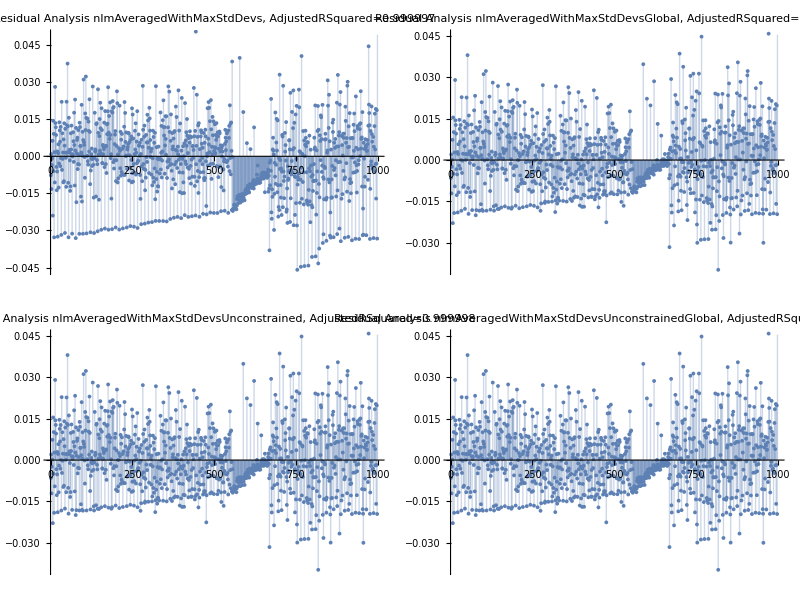

```mathematica
synchronizedPlots=Map[Show[#,ImageSize->500]&,{ListPlot[nlmAveragedWithMaxStdDevs["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis nlmAveragedWithMaxStdDevs,\nAdjustedRSquared=",nlmAveragedWithMaxStdDevs ["AdjustedRSquared"]}]]
,ListPlot[nlmAveragedWithMaxStdDevsUnconstrained["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis nlmAveragedWithMaxStdDevsUnconstrained,\nAdjustedRSquared=",nlmAveragedWithMaxStdDevsUnconstrained["AdjustedRSquared"]}]]
,ListPlot[nlmAveragedWithMaxStdDevsGlobal["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis nlmAveragedWithMaxStdDevsGlobal,\nAdjustedRSquared=",nlmAveragedWithMaxStdDevsGlobal["AdjustedRSquared"]}]]
,ListPlot[nlmAveragedWithMaxStdDevsUnconstrainedGlobal["FitResiduals"],Filling->Axis,PlotLabel->Row[{"Residual Analysis nlmAveragedWithMaxStdDevsUnconstrainedGlobal,\nAdjustedRSquared=",nlmAveragedWithMaxStdDevsUnconstrainedGlobal["AdjustedRSquared"]}]]}];

Multicolumn[synchronizedPlots,2,Appearance->"Framed"]
```

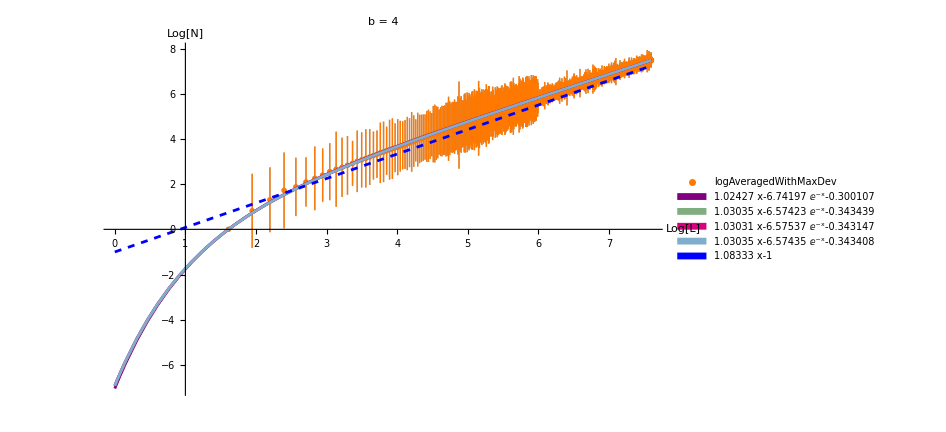

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-2223.99] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3644.45] is too small to represent as a normalized machine number; precision may be lost.

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-754.568] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Averaged data fit with errors and a+c ⅇ^-x+df x RGBColor[0.5, 0, 0.5]: d_f=1.02430.0026, Parameters: | Estimate | Standard Error | t-Statistic | P-Value
a | -0.300107 | 0.00595982 | -50.3549 | 6.85028×10^-276
c | -6.74197 | 0.0230822 | -292.086 | 0.
ω | 0. | 0. | ComplexInfinity | 0.
df | 1.02427 | 0.00083663 | 1224.28 | 0.
Averaged data fit with errors and a+c ⅇ^-x+df x (unconstrained) RGBColor[0.5, 0.68, 0.5]: d_f=1.03040.0026, Parameters: | Estimate | Standard Error | t-Statistic | P-Value
a | -0.343439 | 0.00579922 | -59.2216 | 0.
c | -6.57423 | 0.0224602 | -292.706 | 0.
ω | 0. | 0. | ComplexInfinity | 0.
df | 1.03035 | 0.000814086 | 1265.65 | 0.

Result from the litterature (exact with SLE) RGBColor[0, 0, 1]: 13/12 = 1.08333

```mathematica
maxx=Max[rawData[[All,1]]];
maxy=Max[rawData[[All,2]]];

thresholdBelow=0;
thresholdAbove=maxx-0;

Show[{ListPlot[logAveragedWithMaxDev,PlotStyle->{GrayLevel[0],Directive[Opacity[0.3]]},AxesLabel->{"Log[L]","Log[N]"}]
,ListPlot[logAveragedWithMaxDev,PlotStyle->RGBColor[1, 0.47000000000000003, 0],PlotLegends->{"logAveragedWithMaxDev"}]
,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 0, 0.5],Thickness->0.004},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],Right]]&@nlmAveragedWithMaxStdDevs[x]
,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 0.68, 0.5],Thickness->0.004},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],Right]]&@nlmAveragedWithMaxStdDevsUnconstrained[x]
,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.85, 0, 0.5],Thickness->0.004},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],Right]]&@nlmAveragedWithMaxStdDevsGlobal[x]
,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 0.68, 0.8],Thickness->0.004},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],Right]]&@nlmAveragedWithMaxStdDevsUnconstrainedGlobal[x]

,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, 0, 1],Dashed},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],Right]]&@(x (dfSLE/.bb->N[b])-1)
}
,PlotLabel->Row[{" b = ",b}]
,PlotRange->{All,{0,All}},AxesOrigin->{1,0},ImageSize->700]

Print[ "Averaged data fit with errors and " ,fitFunc," RGBColor[0.5, 0, 0.5]: d_f=",Around[Quiet@nlmAveragedWithMaxStdDevs["ParameterTable"][[1]][[1,-1,2]],π*nlmAveragedWithMaxStdDevs["ParameterTable"][[1]][[1,-1,3]]],", Parameters:",Quiet@nlmAveragedWithMaxStdDevs["ParameterTable"],"
Averaged data fit with errors and " ,fitFunc," (unconstrained) RGBColor[0.5, 0.68, 0.5]: d_f=",Around[Quiet@nlmAveragedWithMaxStdDevsUnconstrained["ParameterTable"][[1]][[1,-1,2]],π*nlmAveragedWithMaxStdDevsUnconstrained["ParameterTable"][[1]][[1,-1,3]]],", Parameters:",Quiet@nlmAveragedWithMaxStdDevsUnconstrained["ParameterTable"],"

Result from the litterature (exact with SLE) RGBColor[0, 0, 1]: ",(dfSLE/.bb->b)," = ",(dfSLE/.bb->b/1.)]
```

#### Forgot what this is

```mathematica
fitFuncs=Table[x^(-i),{i,-1,3}];
(*fitFuncs=Append[Table[x^(-i),{i,-1,0}],Exp[-x]];*)
(*fitFuncs={x,1,Exp[-x],Exp[-2 x]};(*Exp[-1.3 x]*)*)

fitFunc=a+c Exp[-ω x]+df x;

lmAveraged=LinearModelFit[logAveragedWithErrors,x,x(*,Weights->Automatic*)];
Print[Row[{"lmAveraged: ",#//Normal}]]&@%
lmMaxDev=LinearModelFit[logAveragedWithMaxDev,x,x(*,Weights->Automatic*)];
Print[Row[{"lmMaxDev: ",#//Normal}]]&@%


fitFuncs={x,1,Exp[-6x]};

lmpAveraged=LinearModelFit[logAveragedWithErrors,fitFuncs,x];
Print[Row[{"\nlmpAveraged: ",#//Normal}]]&@%
lmpMaxDev=LinearModelFit[logAveragedWithMaxDev,fitFuncs,x];
Print[Row[{"lmpMaxDev: ",#//Normal}]]&@%
lmpWithEstimatedStdDevs=LinearModelFit[logAveragedWithEstimatedStdDevs,fitFuncs,x];
Print[Row[{"lmpMaxDev: ",#//Normal}]]&@%

fitFuncs={x,1,Exp[-x]};

lmpAveraged=LinearModelFit[logAveragedWithErrors,fitFuncs,x];
Print[Row[{"\nlmpAveraged: ",#//Normal}]]&@%
lmpMaxDev=LinearModelFit[logAveragedWithMaxDev,fitFuncs,x];
Print[Row[{"lmpMaxDev: ",#//Normal}]]&@%
lmpWithEstimatedStdDevs=LinearModelFit[logAveragedWithEstimatedStdDevs,fitFuncs,x];
Print[Row[{"lmpMaxDev: ",#//Normal}]]&@%
```

lmAveraged: -2.04869+1.27293 x

lmMaxDev: -2.04482+1.27052 x

lmpAveraged: -0.538091-18172.1 ⅇ^(-6 x)+1.05696 x

lmpMaxDev: -0.44996-19234.5 ⅇ^(-6 x)+1.04445 x

lmpMaxDev: -0.534174-18219.3 ⅇ^(-6 x)+1.0564 x

lmpAveraged: -0.362869-6.49892 ⅇ^-x+1.03306 x

lmpMaxDev: -0.361257-6.50491 ⅇ^-x+1.03281 x

lmpMaxDev: -0.363257-6.49751 ⅇ^-x+1.03313 x

```mathematica
fitFunc=a+c Exp[-ω x]+c2 Exp[-ω2 x]+df x;

nlmAveraged=NonlinearModelFit[logAveragedWithErrors,{fitFunc,{-2<a<2,2.<=ω<=3.,0.1<=ω2<=1.}},{{a,-0.5},{c,-30.},ω,c2,ω2,df(*{df,1.083}*)},x,MaxIterations->1000];
Print[Row[{"nlmAveraged2 with " ,fitFunc ": ",#//Normal}]]&@%

NonlinearModelFit[logAveragedWithMaxDev,{fitFunc(*,{-2<a<2,2.<=ω<=3.,0.1<=ω2<=1.}*)},{a,c,ω,c2,ω2,df(*{df,1.083}*)},x,MaxIterations->1000];
Print[Row[{"nlmMaxDev without constraints: ",#//Normal}]]&@%


nlmMaxDev=NonlinearModelFit[logAveragedWithMaxDev,{fitFunc,{-2<a<2,2.<=ω<=3.,0.1<=ω2<=1.}},{{a,-0.5},{c,-30.},ω,c2,ω2,df(*{df,1.083}*)},x,MaxIterations->1000];
Print[Row[{"nlmMaxDev: ",#//Normal}]]&@%

Print["Result from the litterature (exact with SLE) : ",(dfSLE/.bb->b)," = ",Style[(dfSLE/.bb->b/1.),RGBColor[0, 0, 1]]]
```

nlmAveraged2 with :  (a+c ⅇ^(-x ω)+c2 ⅇ^(-x ω2)+df x)-0.66844-30.108 ⅇ^(-2.00071 x)+0.342589 ⅇ^(-0.546926 x)+1.07449 x

nlmMaxDev without constraints: -0.241064-2.40731 ⅇ^(-0.768548 x)-2.40731 ⅇ^(-0.768548 x)+1.01813 x

nlmMaxDev: -0.719338-30.0531 ⅇ^(-2.00371 x)+0.718269 ⅇ^(-0.887409 x)+1.08243 x

Result from the litterature (exact with SLE) : 13/12 = 1.08333

0.999988

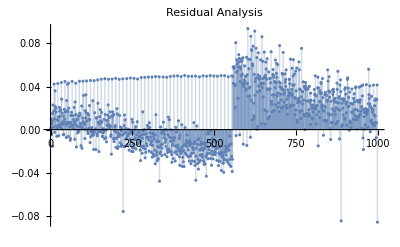

```mathematica
(*Extract and plot residuals*)

nlmMaxDev["AdjustedRSquared"]
ListPlot[nlmMaxDev["FitResiduals"],Filling->Axis,PlotLabel->"Residual Analysis"]
```

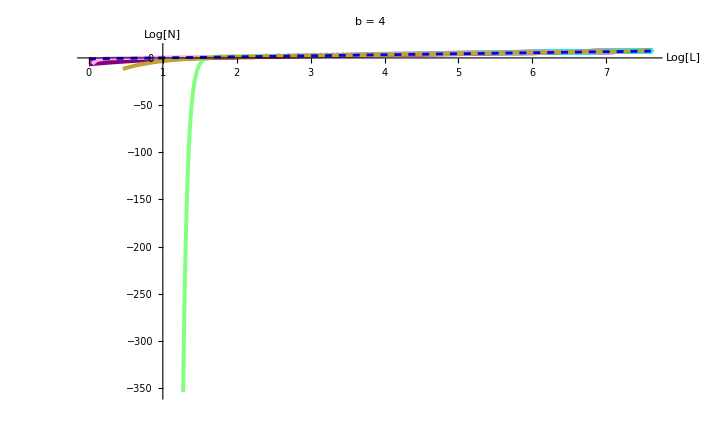

Averaged data fit with errors RGBColor[1, 0, 0]: d_f=1.27290.0030
Averaged data fit with errors and 1+ⅇ^-x+x RGBColor[0.5, 0, 0.5]: d_f=1.03310.0019

a+c ⅇ^(-x ω)+df x  fit  RGBColor[1, Rational[2, 3], 1]: d_f=1.07671Null, Parameters:{a→-0.668862,c→-15.1748,ω→18.8013,df→1.07671}
Averaged data fit with errors and a+c ⅇ^(-x ω)+df xnonlinearModel RGBColor[0.5, 1, 0.5]: d_f=1.03620.0035

Averaged data fit with MaxDevs and a+c ⅇ^(-x ω)+df xnonlinearModel RGBColor[0.76, 0.63, 0.19]: d_f=1.0820.013, Parameters: | Estimate | Standard Error | t-Statistic | P-Value
a | -0.719338 | 0.114184 | -6.29983 | 4.47067×10^-10
c | -30.0531 | 45.6826 | -0.657868 | 0.510775
ω | 2.00371 | 2.09366 | 0.957037 | 0.338782
c2 | 0.718269 | 15.1915 | 0.047281 | 0.962299
ω2 | 0.887409 | 5.07186 | 0.174967 | 0.861141
df | 1.08243 | 0.0132121 | 81.9276 | 0.

Result from the litterature (exact with SLE) RGBColor[0, 0, 1]: 13/12 = 1.08333

```mathematica
maxx=Max[rawData[[All,1]]];
maxy=Max[rawData[[All,2]]];

thresholdBelow=0;
thresholdAbove=maxx-0;

Show[{ListPlot[logAveragedWithMaxDev,PlotStyle->{GrayLevel[0],Directive[Opacity[0.3]]},AxesLabel->{"Log[L]","Log[N]"}]
,ListPlot[logAveragedWithEstimatedStdDevs,PlotStyle->RGBColor[1, 0.55, 1]]
,ListPlot[logAveragedWithErrors,PlotStyle->{RGBColor[0, 1, 1],Directive[Opacity[0.3]]}]
(*,Plot[lmp[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, Rational[2, 3], 0],Thickness->0.004}]*)
,Plot[lmAveraged[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[1, 0, 0],Thickness->0.004}]
,Plot[lmpAveraged[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 0, 0.5],Thickness->0.004}]
,Plot[fitFunc/. fitSol,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[1, Rational[2, 3], 1],Thickness->0.004}]
,Plot[nlmAveraged[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 1, 0.5],Thickness->0.004}]

,Plot[nlmMaxDev[x],{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.76, 0.63, 0.19],Thickness->0.004}]

,Plot[x (dfSLE/.bb->b)-1,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, 0, 1],Dashed}]}
,(*PlotRange->All,*)PlotLabel->Row[{" b = ",b}]
(*,Epilog->{Directive[Dashed,GrayLevel[0.5]],
Line[{{Log[thresholdBelow],0},{Log[thresholdBelow],Log[maxy]//N}}]
,Line[{{Log[thresholdAbove],0},{Log[thresholdAbove],Log[maxy]//N}}]}*)
,PlotRange->{{7,7.5},{6.5,All}},AxesOrigin->{1,0}]



Print[ (*"Full data - Linear fit : d_f=",Around[Quiet@lm["ParameterTable"][[1]][[1,3,2]],π*lm["ParameterErrors"][[2]]],*)"
Averaged data fit with errors RGBColor[1, 0, 0]: d_f=",Around[Quiet@lmAveraged["ParameterTable"][[1]][[1,3,2]],π*lmAveraged["ParameterErrors"][[2]]],"
Averaged data fit with errors and " ,Total@fitFuncs," RGBColor[0.5, 0, 0.5]: d_f=",Around[Quiet@lmpAveraged["ParameterTable"][[1]][[1,2,2]],π*lmpAveraged["ParameterErrors"][[1]]],"

",fitFunc,"  fit  RGBColor[1, Rational[2, 3], 1]: d_f=",Around[df/.fitSol,Null],", Parameters:",fitSol,"
Averaged data fit with errors and " ,fitFunc,"nonlinearModel RGBColor[0.5, 1, 0.5]: d_f=",Around[Quiet@nlmAveraged["ParameterTable"][[1,1,5,2]],π*Quiet@nlmAveraged["ParameterTable"][[1,1,5,3]]],"

Averaged data fit with MaxDevs and " ,fitFunc,"nonlinearModel RGBColor[0.76, 0.63, 0.19]: d_f=",Around[Quiet@nlmMaxDev["ParameterTable"][[1,1,-1,2]],(*π**)Quiet@nlmMaxDev["ParameterTable"][[1,1,-1,3]]],", Parameters:",Quiet@nlmMaxDev["ParameterTable"],(*,"

Full data - ",Total@fitFuncs," fit: d_f=",Around[Quiet@lmp["ParameterTable"][[1]][[1,2,2]],π*lmp["ParameterErrors"][[1]]]*)"

Result from the litterature (exact with SLE) RGBColor[0, 0, 1]: ",(dfSLE/.bb->b)," = ",(dfSLE/.bb->b/1.)]
```

```mathematica
Quiet@lmpAveraged["ParameterTable"][[1]]
Quiet@nlmAveraged["ParameterTable"][[1]]
```

| Estimate | Standard Error | t-Statistic | P-Value
x | 1.05291 | 0.000680.00007 | 1558.168. | BetaRegularized[0.000410.00009,498,1/2]
1 | -0.509589 | 0.00470.0005 | -109.12. | BetaRegularized[0.0780.016,498,1/2]
ⅇ^(-2 x) | -29.6251 | 0.0900.010 | -328.36. | BetaRegularized[0.00910.0020,498,1/2]

| Estimate | Standard Error | t-Statistic | P-Value
a | -0.653659 | 1.36687 | -0.478216 | 0.632601
c | -3.4484 | 95.7668 | -0.0360083 | 0.971283
ω | 1.32346 | 18.4345 | 0.0717928 | 0.942781
df | 0.660756 | 0.190947 | 3.46042 | 0.000562223

```mathematica
Quiet@nlmMaxDev["ParameterTable"][[1,All,1;;3]]//Normal
```

Part::take: Cannot take positions 1 through 3 in Alignment→{Left,Automatic}.

{{,Estimate,Standard Error},{a,-0.719338,0.114184},{c,-30.0531,45.6826},{ω,2.00371,2.09366},{c2,0.718269,15.1915},{ω2,0.887409,5.07186},{df,1.08243,0.0132121}}

ChannelObject::connfail: Could not connect to the server "mqtts://channelbroker-mqtt.wolframcloud.com:8883".

ResourceSubmit::rscloudc: You must connect to the Wolfram cloud to submit the resource. Please use CloudConnect to establish a connection with the Wolfram cloud.

ChannelObject::connfail: Could not connect to the server "mqtts://channelbroker-mqtt.wolframcloud.com:8883".

ResourceSubmit::rscloudc: You must connect to the Wolfram cloud to submit the resource. Please use CloudConnect to establish a connection with the Wolfram cloud.

### Drop both first and/or last few

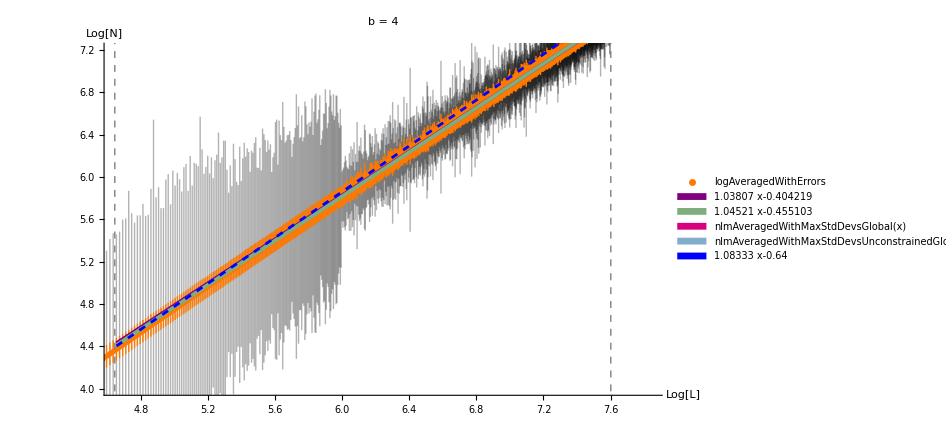

```mathematica
maxx=Max[rawData[[All,1]]];
maxy=Max[rawData[[All,2]]];

thresholdBelow=104;
thresholdAbove=maxx-0;

droppedWithMaxDev=Select[logAveragedWithMaxDev,Log[thresholdBelow]<#[[1]]<Log[thresholdAbove]&];
droppedWithErrors=Select[logAveragedWithErrors,Log[thresholdBelow]<#[[1]]<Log[thresholdAbove]&];


lmdroppedWithMaxDev=LinearModelFit[droppedWithMaxDev,x,x,Weights->Automatic];
lmdroppedWithErrors=LinearModelFit[droppedWithErrors,x,x,Weights->Automatic];
(*lmpdropped=LinearModelFit[dropped,fitFuncs,x];*)

Show[{ListPlot[logAveragedWithMaxDev,PlotStyle->{GrayLevel[0],Directive[Opacity[0.3]]},AxesLabel->{"Log[L]","Log[N]"}]
,ListPlot[logAveragedWithErrors,PlotStyle->RGBColor[1, 0.47000000000000003, 0],PlotLegends->{"logAveragedWithErrors"}]
,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 0, 0.5],Thickness->0.004},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],Right]]&@lmdroppedWithMaxDev[x]
,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 0.68, 0.5],Thickness->0.004},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],Right]]&@lmdroppedWithErrors[x]
,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.85, 0, 0.5],Thickness->0.004},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],Right]]&@nlmAveragedWithMaxStdDevsGlobal[x]
,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0.5, 0.68, 0.8],Thickness->0.004},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],Right]]&@nlmAveragedWithMaxStdDevsUnconstrainedGlobal[x]

,Plot[#,{x,Log[thresholdBelow+1],Log[thresholdAbove]},PlotStyle->{RGBColor[0, 0, 1],Dashed},PlotLegends->Placed[SwatchLegend[{TraditionalForm[#]}],Right]]&@(x (dfSLE/.bb->N[b])-0.64)
}
,Epilog->{Directive[Dashed,GrayLevel[0.5]],
Line[{{Log[thresholdBelow],0},{Log[thresholdBelow],Log[maxy]//N}}]
,Line[{{Log[thresholdAbove],0},{Log[thresholdAbove],Log[maxy]//N}}]}
,PlotLabel->Row[{" b = ",b}]
,PlotRange->{{Log[thresholdBelow],Log[maxy]},{4,7.2}},AxesOrigin->{Log[thresholdBelow],0},ImageSize->700]
```

### Extra analysis

#### Plot with different drops below

```mathematica
dfDropped=ParallelTable[With[{
lmdropped=LinearModelFit[Select[logAveragedWithErrors,#[[1]]>=Log[i]&],x,x]},
{i,Quiet@lmdropped["ParameterTable"][[1]][[1,3,2]]}],{i,5,100}];
```

```mathematica
dfDroppedMore=ParallelTable[With[{
lmdropped=LinearModelFit[Select[logAveragedWithErrors,#[[1]]>=Log[i]&],x,x]},
{i,Quiet@lmdropped["ParameterTable"][[1]][[1,3,2]]}],{i,101,200}];
```

```mathematica
dfDroppedMore2=ParallelTable[With[{
lmdropped=LinearModelFit[Select[logAveragedWithErrors,#[[1]]>=Log[i]&],x,x]},
{i,Quiet@lmdropped["ParameterTable"][[1]][[1,3,2]]}],{i,201,400}];
```

```mathematica
dfDroppedMore3=ParallelTable[With[{
lmdropped=LinearModelFit[Select[logAveragedWithErrors,#[[1]]>=Log[i]&],x,x]},
{i,Quiet@lmdropped["ParameterTable"][[1]][[1,3,2]]}],{i,401,800}];
```

```mathematica
dfDroppedMore4=ParallelTable[With[{
lmdropped=LinearModelFit[Select[logAveragedWithErrors,#[[1]]>=Log[i]&],x,x]},
{i,Quiet@lmdropped["ParameterTable"][[1]][[1,3,2]]}],{i,801,1000}];
```

FittedModel[…]

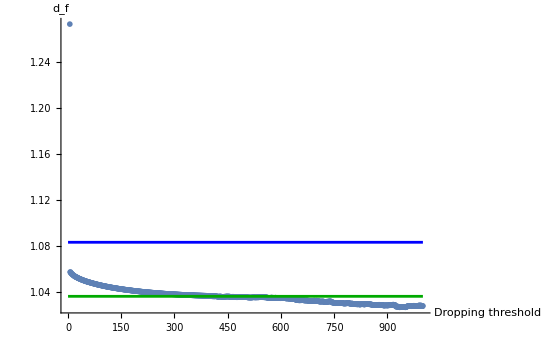

```mathematica
dfTogether=Join[dfDropped,dfDroppedMore,dfDroppedMore2,dfDroppedMore3,dfDroppedMore4];
(*fit=LinearModelFit[dfTogether,{1/Log[x],1},x];
Quiet@fit["ParameterTable"][[1]]*)

lmDrops=LinearModelFit[DeleteCases[dfTogether,{x_,_}/;(x<0)],{1},x]

Show[
{ListPlot[dfTogether,PlotRange->{All,All}]
(*,Plot[fit[x],{x,0,1000},PlotStyle->Red]*)
,Plot[dfSLE/.bb->b/1.,{x,0,1000},PlotStyle->RGBColor[0, 0, 1]]
,Plot[lmDrops[x],{x,0,1000},PlotStyle->RGBColor[0, Rational[2, 3], 0]]
}
,AxesLabel->{"Dropping threshold",Subscript[d, f]},PlotRange->All]
```

#### Plot with different drops Above BAD

```mathematica
thresholdBelow=200;(*Fix this*)

dfDroppedAbove=Table[With[{
lmdropped=LinearModelFit[Log[DeleteCases[rawData,{a_,_}/;(a<thresholdBelow ||  a>(maxx-i))]],x,x]},
{i,Quiet@lmdropped["ParameterTable"][[1]][[1,3,2]]}],{i,0,1500}];
```

```mathematica
fitFunc=a+d Exp[c x];
fit=FindFit[dfDroppedAbove,fitFunc,{a,c,d},x]

Show[
{ListPlot[dfDroppedAbove,PlotRange->{All,All}]
,Plot[fitFunc/.fit,{x,2,1500},PlotStyle->Red]
,Plot[dfSLE/.bb->b/1.,{x,0,1000},PlotStyle->Blue]
},PlotRange->{All,All}]
```

{a→8.0864733946827×10^618,c→1.,d→-1.98793×10^-28}

-Graphics-

```mathematica
ListPlot[dfDroppedAbove,PlotRange->{All,All}]
```

-Graphics-

#### Plot with different POSITIONS of the same WINDOW: (i)< a < (i + 500)

```mathematica
window=500;(*Set this*)

dfDroppedWindow=ParallelTable[With[{
lmdropped=LinearModelFit[Select[logAveragedWithErrors,Log[i]<#[[1]]<Log[window+i]&],x,x]},
{i,Quiet@lmdropped["ParameterTable"][[1]][[1,3,2]]}],{i,0,maxx-window}];
```

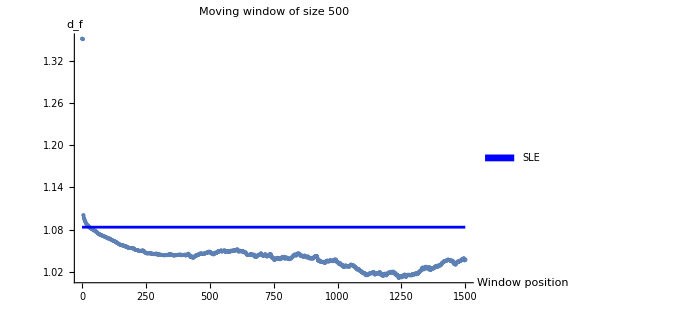

```mathematica
Show[
{ListPlot[dfDroppedWindow,PlotRange->{All,All}]
,Plot[dfSLE/.bb->b/1.,{x,0,1500},PlotStyle->RGBColor[0, 0, 1],PlotLegends->SwatchLegend[{"SLE"}]]
},PlotRange->{All,All},PlotLabel->Row[{"Moving window of size ",window}],AxesLabel->{"Window position",Subscript[d, f]},ImageSize->500]
```

#### Plot with different POSITIONS of the same WINDOW: Changing window

```mathematica
windowPlots=Table[
dfDroppedWindow={window,ParallelTable[With[{
lmdropped=LinearModelFit[Select[logAveragedWithErrors,Log[i]<#[[1]]<Log[window+i]&],x,x]},
{i,Around[Quiet@lmdropped["ParameterTable"][[1]][[1,3,2]],π*lmdropped["ParameterErrors"][[2]]]}],{i,0,maxx-window,20}]}
,{window,100,1000,50}];
```

```mathematica
windowPlots[[1]]
```

{100,{{0,1.510.04},{20,1.1230.006},{40,1.1100.005},{60,1.1030.005},{80,1.09270.0015},{100,1.08840.0016},{120,1.08480.0015},{140,1.08300.0023},{160,1.07950.0030},{180,1.0770.004},{200,1.0740.004},{220,1.0710.005},{240,1.0720.004},{260,1.0670.005},{280,1.0660.005},{300,1.0640.005},{320,1.040.04},{340,1.050.06},{360,1.050.08},{380,1.060.09},{400,1.090.09},{420,1.040.09},{440,1.070.10},{460,1.030.11},{480,1.020.12},{500,1.040.12},{520,1.000.13},{540,1.010.13},{560,1.000.12},{580,1.010.13},{600,1.100.13},{620,1.090.14},{640,1.120.15},{660,1.050.18},{680,1.030.16},{700,1.110.18},{720,1.050.18},{740,1.160.17},{760,1.030.16},{780,1.040.17},{800,1.050.14},{820,1.060.16},{840,1.010.16},{860,1.080.19},{880,1.100.20},{900,1.080.20},{920,1.070.19},{940,0.930.19},{960,1.030.17},{980,1.040.17},{1000,1.100.18},{1020,1.010.17},{1040,1.050.17},{1060,1.020.18},{1080,0.980.19},{1100,1.090.19},{1120,1.080.20},{1140,1.040.20},{1160,0.980.21},{1180,0.990.21},{1200,1.070.19},{1220,1.150.20},{1240,1.090.21},{1260,1.040.21},{1280,0.950.22},{1300,0.890.22},{1320,0.960.22},{1340,0.980.20},{1360,1.020.20},{1380,1.010.19},{1400,0.960.19},{1420,1.040.19},{1440,1.050.21},{1460,1.080.21},{1480,1.000.22},{1500,0.890.23},{1520,0.980.24},{1540,1.090.26},{1560,1.210.24},{1580,1.120.23},{1600,1.000.24},{1620,0.940.26},{1640,0.920.26},{1660,1.030.26},{1680,1.010.27},{1700,1.050.28},{1720,1.060.28},{1740,0.970.25},{1760,0.940.26},{1780,1.060.28},{1800,1.140.29},{1820,1.170.25},{1840,1.160.25},{1860,0.840.20},{1880,0.920.21},{1900,1.030.22}}}

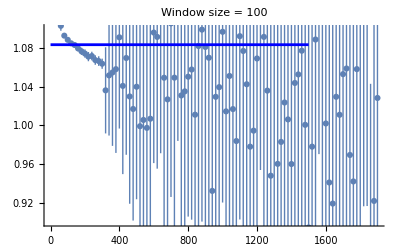
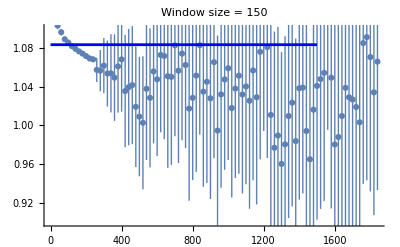
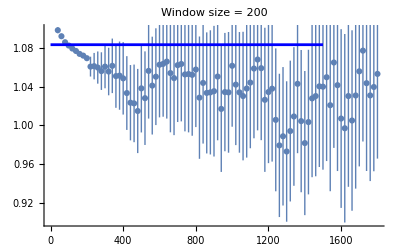
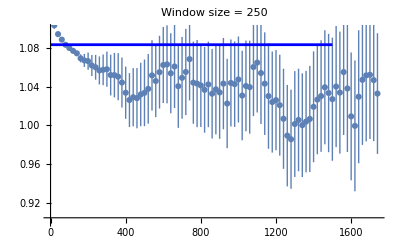
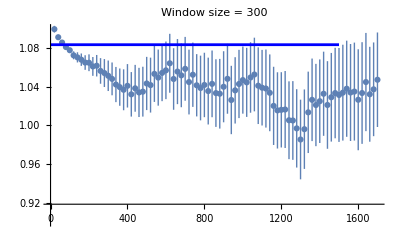
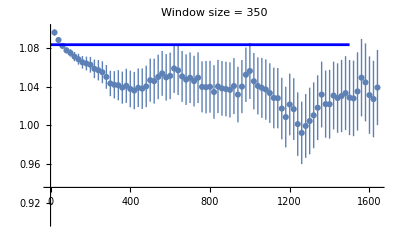
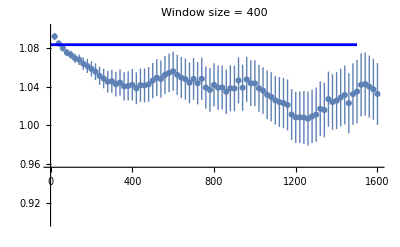
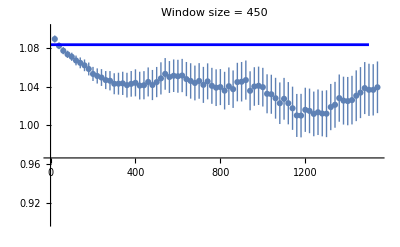

```mathematica
showWindowPlots=Show[
{ListPlot[#[[2]],PlotRange->{All,All}]
,Plot[dfSLE/.bb->b/1.,{x,0,2000-window},PlotStyle->RGBColor[0, 0, 1]]
},PlotRange->{All,{0.9,1.1}},PlotLabel->Row[{"Window size = ",#[[1]]}]]&/@windowPlots
```

```mathematica
synchronizedPlots=Map[Show[#,PlotRange->{All,{0.99,1.05}},ImageSize->220]&,showWindowPlots];

Multicolumn[synchronizedPlots,4,Appearance->"Framed"]
```

```mathematica
Map[Show[#,PlotRange->{All,{1,1.005}},ImageSize->280]&,showWindowPlots[[6;;8]]];
Multicolumn[%,3,Appearance->"Framed"]
```